Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210210_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->1];
datafullwithheading=Import["../data/ccm1_data_modified.csv"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
Print["Dataset Length: ",Dimensions@datafull[[All,9]]]
```

Dataset Length: {459203}

```mathematica
Magnify[TableView[datafullwithheading],0.6]
```

SEQUENCE_ID$Aborted$AbortedREFERENCE_DATEPIECE_IDMATERIAL_IDMOLD_WIDTHWIDTHTHICKNESSWEIGHTLENGTHHEAT_ID$AbortedEXIT_TEMPSLAB_TRANSITION1122115686CCM1$Aborted$Aborted148956$Aborted.124`*^787..274`*^10.335`*^101600018126002122115686CCM1$Aborted$Aborted148958$Aborted.124`*^787..274`*^10.335`*^101600018126003122115686CCM1$Aborted$Aborted148959$Aborted.124`*^787..274`*^10.335`*^101600018126004122115686CCM1$Aborted$Aborted148957$Aborted.124`*^787..274`*^10.335`*^101600018126005122115686CCM1$Aborted$Aborted$Aborted$Aborted.124`*^787..274`*^10.335`*^101600018126006122115686CCM1$Aborted$Aborted148954$Aborted.124`*^787..274`*^10.335`*^101600018126007122115686CCM1$Aborted$Aborted148955$Aborted.124`*^787..274`*^10.335`*^101600018126008173117744CCM1$Aborted$Aborted150353$Aborted.123`*^765..197`*^10.323`*^101700034130009173117744CCM1$Aborted$Aborted150351$Aborted.123`*^765..197`*^10.323`*^1017000341300010173117744CCM1$Aborted$Aborted150352$Aborted.123`*^765..197`*^10.323`*^1017000341300011173117744CCM1$Aborted$Aborted150354$Aborted.123`*^765..197`*^10.323`*^1017000341300012173117744CCM1$Aborted$Aborted150355$Aborted.123`*^765..197`*^10.323`*^1017000341300013173117744CCM1$Aborted$Aborted150356$Aborted.123`*^765..197`*^10.323`*^1017000341300014173117744CCM1$Aborted$Aborted150357$Aborted.123`*^765..197`*^10.323`*^1017000341300015169117701CCM1$Aborted$Aborted150467$Aborted.122`*^765..207`*^6.342`*^1017000281300416169117701CCM1$Aborted$Aborted150469$Aborted.122`*^765..207`*^6.342`*^1017000281300417169117701CCM1$Aborted$Aborted150470$Aborted.122`*^765..207`*^6.342`*^1017000281300418169117701CCM103.01.1717000281-05150471#NAME?1.22e665.207000.3.42e917000281300419169117701CCM103.01.1717000281-06150472#NAME?1.22e665.207000.3.42e917000281300420169117701CCM103.01.1717000281-02150468#NAME?1.22e665.207000.3.42e917000281300421169117701CCM103.01.1717000281-07150473#NAME?1.22e665.207000.3.42e917000281300422169117701CCM103.01.1717000281-08150474#NAME?1.22e665.207000.3.42e917000281300423181118183CCM104.01.1717000761-05150884#NAME?1.23e665.2.07e93.41e917000761260024181118183CCM104.01.1717000761-02150881#NAME?1.23e665.2.07e93.41e917000761260025181118183CCM104.01.1717000761-03150882#NAME?1.23e665.2.07e93.41e917000761260026181118183CCM104.01.1717000761-04150883#NAME?1.23e665.2.07e93.41e917000761260027181118183CCM104.01.1717000761-01150880#NAME?1.23e665.2.07e93.41e917000761260028181118183CCM104.01.1717000761-06150885#NAME?1.23e665.2.07e93.41e917000761260029181118183CCM104.01.1717000761-07150886#NAME?1.23e665.2.07e93.41e917000761260030202118637CCM106.01.1717001141-02151265#NAME?1.53e666.2.17e92.85e917001141260031202118637CCM106.01.1717001141-05151268#NAME?1.53e666.2.17e92.85e917001141260032202118637CCM106.01.1717001141-06151269#NAME?1.53e666.2.17e92.85e917001141260033202118637CCM106.01.1717001141-01151264#NAME?1.53e666.2.17e92.85e917001141260034202118637CCM106.01.1717001141-03151266#NAME?1.53e666.2.17e92.85e917001141260035202118637CCM106.01.1717001141-04151267#NAME?1.53e666.2.17e92.85e917001141260036202118637CCM106.01.1717001141-07151270#NAME?1.53e666.2.17e92.85e917001141260037202118702CCM106.01.1717001201-03151288#NAME?1520.66.2.07e9274000.17001201260038202118702CCM106.01.1717001201-04151289#NAME?1520.66.2.07e9274000.17001201260039202118702CCM106.01.1717001201-05151290#NAME?1520.66.2.07e9274000.17001201260040202118702CCM106.01.1717001201-06151291#NAME?1520.66.2.07e9274000.17001201260041202118702CCM106.01.1717001201-07151292#NAME?1520.66.2.07e9274000.17001201260042202118702CCM106.01.1717001201-08151293#NAME?1520.66.2.07e9274000.17001201260043202118702CCM106.01.1717001201-01151286#NAME?1520.66.2.07e9274000.17001201260044202118702CCM106.01.1717001201-02151287#NAME?1520.66.2.07e9274000.17001201260045202118720CCM106.01.1717001221-03151296#NAME?006.35e8017001221260NA46202118720CCM106.01.1717001221-04151297#NAME?006.35e8017001221260NA47202118720CCM106.01.1717001221-02151295#NAME?006.35e8017001221260NA48202118720CCM106.01.1717001221-01151294#NAME?006.35e8017001221260NA49141115798CCM119.12.1616000201-06149109#NAME?1240.67.2.92e94.65e916000201260050141115798CCM119.12.1616000201-05149107#NAME?1240.67.2.92e94.65e916000201260051141115798CCM119.12.1616000201-01149108#NAME?1240.67.2.92e94.65e916000201260052141115798CCM119.12.1616000201-02149104#NAME?1240.67.2.92e94.65e916000201260053141115798CCM119.12.1616000201-03149105#NAME?1240.67.2.92e94.65e916000201260054141115798CCM119.12.1616000201-04149106#NAME?1240.67.2.92e94.65e916000201260055169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e917000281300056169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e917000281300057169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e917000281300058169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e917000281300059169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e917000281300060169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e917000281300061169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e917000281300062169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e917000281300063173117846CCM103.01.1717000401-03150374#NAME?006.53e7017000401300NA64173117846CCM103.01.1717000401-04150375#NAME?006.53e7017000401300NA65173117846CCM103.01.1717000401-05150376#NAME?006.53e7017000401300NA66173117846CCM103.01.1717000401-06150377#NAME?006.53e7017000401300NA67173117846CCM103.01.1717000401-07150378#NAME?006.53e7017000401300NA68173117846CCM103.01.1717000401-01150372#NAME?006.53e7017000401300NA69173117846CCM103.01.1717000401-02150373#NAME?006.53e7017000401300NA70173117826CCM103.01.1717000381-02150366#NAME?1.22e665.2.07e93.42e917000381300071173117826CCM103.01.1717000381-04150368#NAME?1.22e665.2.07e93.42e917000381300072173117826CCM103.01.1717000381-05150369#NAME?1.22e665.2.07e93.42e917000381300073173117826CCM103.01.1717000381-07150371#NAME?1.22e665.2.07e93.42e917000381300074173117826CCM103.01.1717000381-03150367#NAME?1.22e665.2.07e93.42e917000381300075173117826CCM103.01.1717000381-01150365#NAME?1.22e665.2.07e93.42e917000381300076173117826CCM103.01.1717000381-06150370#NAME?1.22e665.2.07e93.42e917000381300077173117826CCM103.01.1717000381-02150366#NAME?1.22e665.2.07e93.42e917000381300078173117826CCM103.01.1717000381-04150368#NAME?1.22e665.2.07e93.42e917000381300079173117826CCM103.01.1717000381-05150369#NAME?1.22e665.2.07e93.42e917000381300080173117826CCM103.01.1717000381-07150371#NAME?1.22e665.2.07e93.42e917000381300081173117826CCM103.01.1717000381-03150367#NAME?1.22e665.2.07e93.42e917000381300082173117826CCM103.01.1717000381-01150365#NAME?1.22e665.2.07e93.42e917000381300083173117826CCM103.01.1717000381-06150370#NAME?1.22e665.2.07e93.42e917000381300084173117826CCM103.01.1717000381-02150366#NAME?1.22e665.2.07e93.42e917000381300085173117826CCM103.01.1717000381-04150368#NAME?1.22e665.2.07e93.42e917000381300086173117826CCM103.01.1717000381-05150369#NAME?1.22e665.2.07e93.42e917000381300087173117826CCM103.01.1717000381-07150371#NAME?1.22e665.2.07e93.42e917000381300088173117826CCM103.01.1717000381-03150367#NAME?1.22e665.2.07e93.42e917000381300089173117826CCM103.01.1717000381-01150365#NAME?1.22e665.2.07e93.42e917000381300090173117826CCM103.01.1717000381-06150370#NAME?1.22e665.2.07e93.42e917000381300091173117826CCM103.01.1717000381-02150366#NAME?1.22e665.2.07e93.42e917000381300092173117826CCM103.01.1717000381-04150368#NAME?1.22e665.2.07e93.42e917000381300093173117826CCM103.01.1717000381-05150369#NAME?1.22e665.2.07e93.42e917000381300094173117826CCM103.01.1717000381-07150371#NAME?1.22e665.2.07e93.42e917000381300095173117826CCM103.01.1717000381-03150367#NAME?1.22e665.2.07e93.42e917000381300096173117826CCM103.01.1717000381-01150365#NAME?1.22e665.2.07e93.42e917000381300097173117826CCM103.01.1717000381-06150370#NAME?1.22e665.2.07e93.42e917000381300098173117871CCM103.01.1717000421-01150379#NAME?0082.017000421300NA99173117871CCM103.01.1717000421-04150382#NAME?0082.017000421300NA100173117871CCM103.01.1717000421-06150496#NAME?0082.017000421300NA101173117871CCM103.01.1717000421-05150383#NAME?0082.017000421300NA102173117871CCM103.01.1717000421-02150380#NAME?0082.017000421300NA103173117871CCM103.01.1717000421-03150381#NAME?0082.017000421300NA104173117871CCM103.01.1717000421-07150497#NAME?0082.017000421300NA105173117871CCM103.01.1717000421-08150498#NAME?0082.017000421300NA106173117846CCM103.01.1717000401-03150374#NAME?1.22e665.1.97e93.26e9170004013000107173117846CCM103.01.1717000401-04150375#NAME?1.22e665.1.97e93.26e9170004013000108173117846CCM103.01.1717000401-05150376#NAME?1.22e665.1.97e93.26e9170004013000109173117846CCM103.01.1717000401-06150377#NAME?1.22e665.1.97e93.26e9170004013000110173117846CCM103.01.1717000401-07150378#NAME?1.22e665.1.97e93.26e9170004013000111173117846CCM103.01.1717000401-01150372#NAME?1.22e665.1.97e93.26e9170004013000112173117846CCM103.01.1717000401-02150373#NAME?1.22e665.1.97e93.26e9170004013000113173117846CCM103.01.1717000401-03150374#NAME?1.22e665.1.97e93.26e9170004013000114173117846CCM103.01.1717000401-04150375#NAME?1.22e665.1.97e93.26e9170004013000115173117846CCM103.01.1717000401-05150376#NAME?1.22e665.1.97e93.26e9170004013000116173117846CCM103.01.1717000401-06150377#NAME?1.22e665.1.97e93.26e9170004013000117173117846CCM103.01.1717000401-07150378#NAME?1.22e665.1.97e93.26e9170004013000118173117846CCM103.01.1717000401-01150372#NAME?1.22e665.1.97e93.26e9170004013000119173117846CCM103.01.1717000401-02150373#NAME?1.22e665.1.97e93.26e9170004013000120173117846CCM103.01.1717000401-03150374#NAME?1.22e665.1.97e93.26e9170004013000121173117846CCM103.01.1717000401-04150375#NAME?1.22e665.1.97e93.26e9170004013000122173117846CCM103.01.1717000401-05150376#NAME?1.22e665.1.97e93.26e9170004013000123173117846CCM103.01.1717000401-06150377#NAME?1.22e665.1.97e93.26e9170004013000124173117846CCM103.01.1717000401-07150378#NAME?1.22e665.1.97e93.26e9170004013000125173117846CCM103.01.1717000401-01150372#NAME?1.22e665.1.97e93.26e9170004013000126173117846CCM103.01.1717000401-02150373#NAME?1.22e665.1.97e93.26e9170004013000127173117846CCM103.01.1717000401-03150374#NAME?1.22e665.1.97e93.26e9170004013000128173117846CCM103.01.1717000401-04150375#NAME?1.22e665.1.97e93.26e9170004013000129173117846CCM103.01.1717000401-05150376#NAME?1.22e665.1.97e93.26e9170004013000130173117846CCM103.01.1717000401-06150377#NAME?1.22e665.1.97e93.26e9170004013000131173117846CCM103.01.1717000401-07150378#NAME?1.22e665.1.97e93.26e9170004013000132173117846CCM103.01.1717000401-01150372#NAME?1.22e665.1.97e93.26e9170004013000133173117846CCM103.01.1717000401-02150373#NAME?1.22e665.1.97e93.26e9170004013000134173117846CCM103.01.1717000401-03150374#NAME?1.22e665.1.97e93.26e9170004013000135173117846CCM103.01.1717000401-04150375#NAME?1.22e665.1.97e93.26e9170004013000136173117846CCM103.01.1717000401-05150376#NAME?1.22e665.1.97e93.26e9170004013000137173117846CCM103.01.1717000401-06150377#NAME?1.22e665.1.97e93.26e9170004013000138173117846CCM103.01.1717000401-07150378#NAME?1.22e665.1.97e93.26e9170004013000139173117846CCM103.01.1717000401-01150372#NAME?1.22e665.1.97e93.26e9170004013000140173117846CCM103.01.1717000401-02150373#NAME?1.22e665.1.97e93.26e9170004013000141173117871CCM103.01.1717000421-01150379#NAME?1.22e665.1.98e93.27e9170004213000142173117871CCM103.01.1717000421-04150382#NAME?1.22e665.1.98e93.27e9170004213000143173117871CCM103.01.1717000421-06150496#NAME?1.22e665.1.98e93.27e9170004213000144173117871CCM103.01.1717000421-05150383#NAME?1.22e665.1.98e93.27e9170004213000145173117871CCM103.01.1717000421-02150380#NAME?1.22e665.1.98e93.27e9170004213000146173117871CCM103.01.1717000421-03150381#NAME?1.22e665.1.98e93.27e9170004213000147173117871CCM103.01.1717000421-07150497#NAME?1.22e665.1.98e93.27e9170004213000148173117871CCM103.01.1717000421-08150498#NAME?1.22e665.1.98e93.27e9170004213000149173117890CCM103.01.1717000441-03150501#NAME?008.19e9017000441300NA150173117890CCM103.01.1717000441-01150499#NAME?008.19e9017000441300NA151173117890CCM103.01.1717000441-02150500#NAME?008.19e9017000441300NA152173117890CCM103.01.1717000441-04150502#NAME?008.19e9017000441300NA153173117890CCM103.01.1717000441-05150503#NAME?008.19e9017000441300NA154173117890CCM103.01.1717000441-06150504#NAME?008.19e9017000441300NA155173117871CCM103.01.1717000421-01150379#NAME?1.22e665.2.16e93.57e9170004213000156173117871CCM103.01.1717000421-04150382#NAME?1.22e665.2.16e93.57e9170004213000157173117871CCM103.01.1717000421-06150496#NAME?1.22e665.2.16e93.57e9170004213000158173117871CCM103.01.1717000421-05150383#NAME?1.22e665.2.16e93.57e9170004213000159173117871CCM103.01.1717000421-02150380#NAME?1.22e665.2.16e93.57e9170004213000160173117871CCM103.01.1717000421-03150381#NAME?1.22e665.2.16e93.57e9170004213000161173117871CCM103.01.1717000421-07150497#NAME?1.22e665.2.16e93.57e9170004213000162173117871CCM103.01.1717000421-08150498#NAME?1.22e665.2.16e93.57e9170004213000163173117871CCM103.01.1717000421-01150379#NAME?1.22e665.2.12e935.170004213000164173117871CCM103.01.1717000421-04150382#NAME?1.22e665.2.12e935.170004213000165173117871CCM103.01.1717000421-06150496#NAME?1.22e665.2.12e935.170004213000166173117871CCM103.01.1717000421-05150383#NAME?1.22e665.2.12e935.170004213000167173117871CCM103.01.1717000421-02150380#NAME?1.22e665.2.12e935.170004213000168173117871CCM103.01.1717000421-03150381#NAME?1.22e665.2.12e935.170004213000169173117871CCM103.01.1717000421-07150497#NAME?1.22e665.2.12e935.170004213000170173117871CCM103.01.1717000421-08150498#NAME?1.22e665.2.12e935.170004213000171169117473CCM102.01.1717000021-05150157#NAME?1.24e665.204000.3.32e9170000212600172169117473CCM102.01.1717000021-06150158#NAME?1.24e665.204000.3.32e9170000212600173169117473CCM102.01.1717000021-07150159#NAME?1.24e665.204000.3.32e9170000212600174169117473CCM102.01.1717000021-04150156#NAME?1.24e665.204000.3.32e9170000212600175169117473CCM102.01.1717000021-01150153#NAME?1.24e665.204000.3.32e9170000212600176169117473CCM102.01.1717000021-02150154#NAME?1.24e665.204000.3.32e9170000212600177169117473CCM102.01.1717000021-03150155#NAME?1.24e665.204000.3.32e9170000212600178169117473CCM102.01.1717000021-05150157#NAME?1.24e665.2.04e93.32e9170000212600179169117473CCM102.01.1717000021-06150158#NAME?1.24e665.2.04e93.32e9170000212600180169117473CCM102.01.1717000021-07150159#NAME?1.24e665.2.04e93.32e9170000212600181169117473CCM102.01.1717000021-04150156#NAME?1.24e665.2.04e93.32e9170000212600182169117473CCM102.01.1717000021-01150153#NAME?1.24e665.2.04e93.32e9170000212600183169117473CCM102.01.1717000021-02150154#NAME?1.24e665.2.04e93.32e9170000212600184169117473CCM102.01.1717000021-03150155#NAME?1.24e665.2.04e93.32e9170000212600185169117473CCM102.01.1717000021-05150157#NAME?1.24e665.2.05e93.34e9170000212605186169117473CCM102.01.1717000021-06150158#NAME?1.24e665.2.05e93.34e9170000212605187169117473CCM102.01.1717000021-07150159#NAME?1.24e665.2.05e93.34e9170000212605188169117473CCM102.01.1717000021-04150156#NAME?1.24e665.2.05e93.34e9170000212605189169117473CCM102.01.1717000021-01150153#NAME?1.24e665.2.05e93.34e9170000212605190169117473CCM102.01.1717000021-02150154#NAME?1.24e665.2.05e93.34e9170000212605191169117473CCM102.01.1717000021-03150155#NAME?1.24e665.2.05e93.34e9170000212605192169117671CCM103.01.1717000261-07150466#NAME?1.22e665.206000.3.4e9170002613000193169117671CCM103.01.1717000261-02150461#NAME?1.22e665.206000.3.4e9170002613000194169117671CCM103.01.1717000261-01150460#NAME?1.22e665.206000.3.4e9170002613000195169117671CCM103.01.1717000261-03150462#NAME?1.22e665.206000.3.4e9170002613000196169117671CCM103.01.1717000261-04150463#NAME?1.22e665.206000.3.4e9170002613000197169117671CCM103.01.1717000261-06150465#NAME?1.22e665.206000.3.4e9170002613000198169117671CCM103.01.1717000261-05150464#NAME?1.22e665.206000.3.4e9170002613000199163116882CCM129.12.1616001121-01150011#NAME?008.44e9016001121260NA200163116882CCM129.12.1616001121-04150014#NAME?008.44e9016001121260NA201163116882CCM129.12.1616001121-06150016#NAME?008.44e9016001121260NA202163116882CCM129.12.1616001121-03150013#NAME?008.44e9016001121260NA203163116882CCM129.12.1616001121-05150015#NAME?008.44e9016001121260NA204163116882CCM129.12.1616001121-07150017#NAME?008.44e9016001121260NA205163116882CCM129.12.1616001121-02150012#NAME?008.44e9016001121260NA206163116886CCM129.12.1616001141-05150022#NAME?005.95e8016001141260NA207163116886CCM129.12.1616001141-03150020#NAME?005.95e8016001141260NA208163116886CCM129.12.1616001141-04150021#NAME?005.95e8016001141260NA209163116886CCM129.12.1616001141-01150018#NAME?005.95e8016001141260NA210163116886CCM129.12.1616001141-02150019#NAME?005.95e8016001141260NA211163116882CCM129.12.1616001121-01150011#NAME?1.29e687.2.11e9247000.160011212600212163116882CCM129.12.1616001121-04150014#NAME?1.29e687.2.11e9247000.160011212600213163116882CCM129.12.1616001121-06150016#NAME?1.29e687.2.11e9247000.160011212600214163116882CCM129.12.1616001121-03150013#NAME?1.29e687.2.11e9247000.160011212600215163116882CCM129.12.1616001121-05150015#NAME?1.29e687.2.11e9247000.160011212600216163116882CCM129.12.1616001121-07150017#NAME?1.29e687.2.11e9247000.160011212600217163116882CCM129.12.1616001121-02150012#NAME?1.29e687.2.11e9247000.160011212600218163116886CCM129.12.1616001141-05150022#NAME?1.27e665.2.14e93.41e9160011412600219163116886CCM129.12.1616001141-03150020#NAME?1.27e665.2.14e93.41e9160011412600220163116886CCM129.12.1616001141-04150021#NAME?1.27e665.2.14e93.41e9160011412600221163116886CCM129.12.1616001141-01150018#NAME?1.27e665.2.14e93.41e9160011412600222163116886CCM129.12.1616001141-02150019#NAME?1.27e665.2.14e93.41e91600114126002236X0023116934CCM129.12.1616001201-05150036#NAME?1.23e665.2.11e93.48e91600120126002246X0023116934CCM129.12.1616001201-06150037#NAME?1.23e665.2.11e93.48e91600120126002256X0023116934CCM129.12.1616001201-07150038#NAME?1.23e665.2.11e93.48e91600120126002266X0023116934CCM129.12.1616001201-01150032#NAME?1.23e665.2.11e93.48e91600120126002276X0023116934CCM129.12.1616001201-02150033#NAME?1.23e665.2.11e93.48e91600120126002286X0023116934CCM129.12.1616001201-03150034#NAME?1.23e665.2.11e93.48e91600120126002296X0023116934CCM129.12.1616001201-04150035#NAME?1.23e665.2.11e93.48e91600120126002306X0023116934CCM129.12.1616001201-05150036#NAME?1.23e665.189000.312000.1600120126002316X0023116934CCM129.12.1616001201-06150037#NAME?1.23e665.189000.312000.1600120126002326X0023116934CCM129.12.1616001201-07150038#NAME?1.23e665.189000.312000.1600120126002336X0023116934CCM129.12.1616001201-01150032#NAME?1.23e665.189000.312000.1600120126002346X0023116934CCM129.12.1616001201-02150033#NAME?1.23e665.189000.312000.1600120126002356X0023116934CCM129.12.1616001201-03150034#NAME?1.23e665.189000.312000.1600120126002366X0023116934CCM129.12.1616001201-04150035#NAME?1.23e665.189000.312000.1600120126002376X0023116934CCM129.12.1616001201-05150036#NAME?1.23e665.2.12e93.49e91600120126002386X0023116934CCM129.12.1616001201-06150037#NAME?1.23e665.2.12e93.49e91600120126002396X0023116934CCM129.12.1616001201-07150038#NAME?1.23e665.2.12e93.49e91600120126002406X0023116934CCM129.12.1616001201-01150032#NAME?1.23e665.2.12e93.49e91600120126002416X0023116934CCM129.12.1616001201-02150033#NAME?1.23e665.2.12e93.49e91600120126002426X0023116934CCM129.12.1616001201-03150034#NAME?1.23e665.2.12e93.49e91600120126002436X0023116934CCM129.12.1616001201-04150035#NAME?1.23e665.2.12e93.49e91600120126002446X0023116935CCM129.12.1616001181-04150042#NAME?1.23e665.2.17e93.58e91600118126002456X0023116935CCM129.12.1616001181-01150039#NAME?1.23e665.2.17e93.58e91600118126002466X0023116935CCM129.12.1616001181-02150040#NAME?1.23e665.2.17e93.58e91600118126002476X0023116935CCM129.12.1616001181-03150041#NAME?1.23e665.2.17e93.58e91600118126002486X0023116935CCM129.12.1616001181-05150043#NAME?1.23e665.2.17e93.58e91600118126002496X0023116935CCM129.12.1616001181-06150044#NAME?1.23e665.2.17e93.58e91600118126002506X0023116935CCM129.12.1616001181-04150042#NAME?1.23e665.2.08e93.43e91600118126002516X0023116935CCM129.12.1616001181-01150039#NAME?1.23e665.2.08e93.43e91600118126002526X0023116935CCM129.12.1616001181-02150040#NAME?1.23e665.2.08e93.43e91600118126002536X0023116935CCM129.12.1616001181-03150041#NAME?1.23e665.2.08e93.43e91600118126002546X0023116935CCM129.12.1616001181-05150043#NAME?1.23e665.2.08e93.43e91600118126002556X0023116935CCM129.12.1616001181-06150044#NAME?1.23e665.2.08e93.43e91600118126002566X0023116935CCM129.12.1616001181-04150042#NAME?1.23e665.2.08e93.43e91600118126002576X0023116935CCM129.12.1616001181-01150039#NAME?1.23e665.2.08e93.43e91600118126002586X0023116935CCM129.12.1616001181-02150040#NAME?1.23e665.2.08e93.43e91600118126002596X0023116935CCM129.12.1616001181-03150041#NAME?1.23e665.2.08e93.43e91600118126002606X0023116935CCM129.12.1616001181-05150043#NAME?1.23e665.2.08e93.43e91600118126002616X0023116935CCM129.12.1616001181-06150044#NAME?1.23e665.2.08e93.43e9160011812600262156116567CCM126.12.1616000761-03149627#NAME?008.66e9016000761260NA263156116567CCM126.12.1616000761-05149629#NAME?008.66e9016000761260NA264156116567CCM126.12.1616000761-07149631#NAME?008.66e9016000761260NA265156116567CCM126.12.1616000761-04149628#NAME?008.66e9016000761260NA266156116567CCM126.12.1616000761-06149630#NAME?008.66e9016000761260NA267156116567CCM126.12.1616000761-01149625#NAME?008.66e9016000761260NA268156116567CCM126.12.1616000761-02149626#NAME?008.66e9016000761260NA269156116588CCM126.12.1616000781-01149632#NAME?1.22e665.1.99e93.29e9160007812600270156116588CCM126.12.1616000781-02149633#NAME?1.22e665.1.99e93.29e9160007812600271156116588CCM126.12.1616000781-04149635#NAME?1.22e665.1.99e93.29e9160007812600272156116588CCM126.12.1616000781-05149636#NAME?1.22e665.1.99e93.29e9160007812600273156116588CCM126.12.1616000781-06149637#NAME?1.22e665.1.99e93.29e9160007812600274156116588CCM126.12.1616000781-07149638#NAME?1.22e665.1.99e93.29e9160007812600275156116588CCM126.12.1616000781-03149634#NAME?1.22e665.1.99e93.29e9160007812600276156116608CCM126.12.1616000821-01149646#NAME?008.29e9016000821260NA277156116608CCM126.12.1616000821-02149647#NAME?008.29e9016000821260NA278156116608CCM126.12.1616000821-03149648#NAME?008.29e9016000821260NA279156116608CCM126.12.1616000821-04149649#NAME?008.29e9016000821260NA280156116608CCM126.12.1616000821-05149650#NAME?008.29e9016000821260NA281156116608CCM126.12.1616000821-06149651#NAME?008.29e9016000821260NA282156116608CCM126.12.1616000821-07149652#NAME?008.29e9016000821260NA283156116588CCM126.12.1616000781-01149632#NAME?1.22e665.1.99e93.29e9160007812605284156116588CCM126.12.1616000781-02149633#NAME?1.22e665.1.99e93.29e9160007812605285156116588CCM126.12.1616000781-04149635#NAME?1.22e665.1.99e93.29e9160007812605286156116588CCM126.12.1616000781-05149636#NAME?1.22e665.1.99e93.29e9160007812605287156116588CCM126.12.1616000781-06149637#NAME?1.22e665.1.99e93.29e9160007812605288156116588CCM126.12.1616000781-07149638#NAME?1.22e665.1.99e93.29e9160007812605289156116588CCM126.12.1616000781-03149634#NAME?1.22e665.1.99e93.29e9160007812605290156116600CCM126.12.1616000801-01149642#NAME?1.22e665.1.98e93.29e9160008012605291156116600CCM126.12.1616000801-02149643#NAME?1.22e665.1.98e93.29e9160008012605292156116600CCM126.12.1616000801-03149644#NAME?1.22e665.1.98e93.29e9160008012605293156116600CCM126.12.1616000801-04149645#NAME?1.22e665.1.98e93.29e9160008012605294156116600CCM126.12.1616000801-05149639#NAME?1.22e665.1.98e93.29e9160008012605295156116600CCM126.12.1616000801-06149640#NAME?1.22e665.1.98e93.29e9160008012605296156116600CCM126.12.1616000801-07149641#NAME?1.22e665.1.98e93.29e9160008012605297156116600CCM126.12.1616000801-01149642#NAME?1.22e665.1.98e93.29e9160008012600298156116600CCM126.12.1616000801-02149643#NAME?1.22e665.1.98e93.29e9160008012600299156116600CCM126.12.1616000801-03149644#NAME?1.22e665.1.98e93.29e9160008012600300156116600CCM126.12.1616000801-04149645#NAME?1.22e665.1.98e93.29e9160008012600301156116600CCM126.12.1616000801-05149639#NAME?1.22e665.1.98e93.29e9160008012600302156116600CCM126.12.1616000801-06149640#NAME?1.22e665.1.98e93.29e9160008012600303156116600CCM126.12.1616000801-07149641#NAME?1.22e665.1.98e93.29e9160008012600304156116600CCM126.12.1616000801-01149642#NAME?1.22e665.1.98e93.29e9160008012600305156116600CCM126.12.1616000801-02149643#NAME?1.22e665.1.98e93.29e9160008012600306156116600CCM126.12.1616000801-03149644#NAME?1.22e665.1.98e93.29e9160008012600307156116600CCM126.12.1616000801-04149645#NAME?1.22e665.1.98e93.29e9160008012600308156116600CCM126.12.1616000801-05149639#NAME?1.22e665.1.98e93.29e9160008012600309156116600CCM126.12.1616000801-06149640#NAME?1.22e665.1.98e93.29e9160008012600310156116600CCM126.12.1616000801-07149641#NAME?1.22e665.1.98e93.29e9160008012600311156116600CCM126.12.1616000801-01149642#NAME?1.22e665.1.87e93.11e9160008012600312156116600CCM126.12.1616000801-02149643#NAME?1.22e665.1.87e93.11e9160008012600313156116600CCM126.12.1616000801-03149644#NAME?1.22e665.1.87e93.11e9160008012600314156116600CCM126.12.1616000801-04149645#NAME?1.22e665.1.87e93.11e9160008012600315156116600CCM126.12.1616000801-05149639#NAME?1.22e665.1.87e93.11e9160008012600316156116600CCM126.12.1616000801-06149640#NAME?1.22e665.1.87e93.11e9160008012600317156116600CCM126.12.1616000801-07149641#NAME?1.22e665.1.87e93.11e9160008012600318156116600CCM126.12.1616000801-01149642#NAME?1.22e665.2.e93.32e8160008012600319156116600CCM126.12.1616000801-02149643#NAME?1.22e665.2.e93.32e8160008012600320156116600CCM126.12.1616000801-03149644#NAME?1.22e665.2.e93.32e8160008012600321156116600CCM126.12.1616000801-04149645#NAME?1.22e665.2.e93.32e8160008012600322156116600CCM126.12.1616000801-05149639#NAME?1.22e665.2.e93.32e8160008012600323156116600CCM126.12.1616000801-06149640#NAME?1.22e665.2.e93.32e8160008012600324156116600CCM126.12.1616000801-07149641#NAME?1.22e665.2.e93.32e8160008012600325156116608CCM126.12.1616000821-01149646#NAME?1.22e665.2.e93.32e9160008212600326156116608CCM126.12.1616000821-02149647#NAME?1.22e665.2.e93.32e9160008212600327156116608CCM126.12.1616000821-03149648#NAME?1.22e665.2.e93.32e9160008212600328156116608CCM126.12.1616000821-04149649#NAME?1.22e665.2.e93.32e9160008212600329156116608CCM126.12.1616000821-05149650#NAME?1.22e665.2.e93.32e9160008212600330156116608CCM126.12.1616000821-06149651#NAME?1.22e665.2.e93.32e9160008212600331156116608CCM126.12.1616000821-07149652#NAME?1.22e665.2.e93.32e9160008212600332158116667CCM126.12.1616000901-01149725#NAME?1.54e666.2.01e92.65e9160009013005333158116667CCM126.12.1616000901-02149726#NAME?1.54e666.2.01e92.65e9160009013005334158116667CCM126.12.1616000901-03149727#NAME?1.54e666.2.01e92.65e9160009013005335158116667CCM126.12.1616000901-04149728#NAME?1.54e666.2.01e92.65e9160009013005336158116667CCM126.12.1616000901-05149729#NAME?1.54e666.2.01e92.65e9160009013005337158116667CCM126.12.1616000901-06149730#NAME?1.54e666.2.01e92.65e9160009013005338158116667CCM126.12.1616000901-07149731#NAME?1.54e666.2.01e92.65e91600090130053396X0020116829CCM127.12.1616001081-02149585#NAME?008.44e9016001081260NA3406X0020116829CCM127.12.1616001081-04149587#NAME?008.44e9016001081260NA3416X0020116829CCM127.12.1616001081-05149588#NAME?008.44e9016001081260NA3426X0020116829CCM127.12.1616001081-06149589#NAME?008.44e9016001081260NA3436X0020116829CCM127.12.1616001081-07149590#NAME?008.44e9016001081260NA3446X0020116829CCM127.12.1616001081-01149584#NAME?008.44e9016001081260NA3456X0020116829CCM127.12.1616001081-03149586#NAME?008.44e9016001081260NA3466X0020116829CCM127.12.1616001081-02149585#NAME?1.54e687.2.07e92.04e91600108126003476X0020116829CCM127.12.1616001081-04149587#NAME?1.54e687.2.07e92.04e91600108126003486X0020116829CCM127.12.1616001081-05149588#NAME?1.54e687.2.07e92.04e91600108126003496X0020116829CCM127.12.1616001081-06149589#NAME?1.54e687.2.07e92.04e91600108126003506X0020116829CCM127.12.1616001081-07149590#NAME?1.54e687.2.07e92.04e91600108126003516X0020116829CCM127.12.1616001081-01149584#NAME?1.54e687.2.07e92.04e91600108126003526X0020116829CCM127.12.1616001081-03149586#NAME?1.54e687.2.07e92.04e9160010812600353169117579CCM102.01.1717000161-02150204#NAME?1.22e665.2.07e93.4e9170001612600354169117579CCM102.01.1717000161-04150206#NAME?1.22e665.2.07e93.4e9170001612600355169117579CCM102.01.1717000161-06150208#NAME?1.22e665.2.07e93.4e9170001612600356169117579CCM102.01.1717000161-07150209#NAME?1.22e665.2.07e93.4e9170001612600357169117579CCM102.01.1717000161-01150203#NAME?1.22e665.2.07e93.4e9170001612600358169117579CCM102.01.1717000161-03150205#NAME?1.22e665.2.07e93.4e9170001612600359169117579CCM102.01.1717000161-05150207#NAME?1.22e665.2.07e93.4e9170001612600360173117744CCM103.01.1717000341-03150353#NAME?008.21e9017000341300NA361173117744CCM103.01.1717000341-01150351#NAME?008.21e9017000341300NA362173117744CCM103.01.1717000341-02150352#NAME?008.21e9017000341300NA363173117744CCM103.01.1717000341-04150354#NAME?008.21e9017000341300NA364173117744CCM103.01.1717000341-05150355#NAME?008.21e9017000341300NA365173117744CCM103.01.1717000341-06150356#NAME?008.21e9017000341300NA366173117744CCM103.01.1717000341-07150357#NAME?008.21e9017000341300NA367182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e9170009613000368182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e9170009613000369182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e9170009613000370182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e9170009613000371182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e9170009613000372182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e9170009613000373182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e9170009613000374223119820CCM109.01.1717001601-01151650#NAME?003.45e8017001601260NA375223119820CCM109.01.1717001601-02151651#NAME?003.45e8017001601260NA376223119820CCM109.01.1717001601-03151652#NAME?003.45e8017001601260NA377223119820CCM109.01.1717001601-04151653#NAME?003.45e8017001601260NA378223119820CCM109.01.1717001601-05151654#NAME?003.45e8017001601260NA379223119820CCM109.01.1717001601-06151655#NAME?003.45e8017001601260NA380223119820CCM109.01.1717001601-07151656#NAME?003.45e8017001601260NA381169117543CCM102.01.1717000121-01150188#NAME?1.22e665.2.07e93.41e8170001212600382169117543CCM102.01.1717000121-02150189#NAME?1.22e665.2.07e93.41e8170001212600383169117543CCM102.01.1717000121-04150191#NAME?1.22e665.2.07e93.41e8170001212600384169117543CCM102.01.1717000121-05150192#NAME?1.22e665.2.07e93.41e8170001212600385169117543CCM102.01.1717000121-06150193#NAME?1.22e665.2.07e93.41e8170001212600386169117543CCM102.01.1717000121-07150194#NAME?1.22e665.2.07e93.41e8170001212600387169117543CCM102.01.1717000121-03150190#NAME?1.22e665.2.07e93.41e8170001212600388169117579CCM102.01.1717000161-02150204#NAME?1.22e665.2.06e93.4e9170001612600389169117579CCM102.01.1717000161-04150206#NAME?1.22e665.2.06e93.4e9170001612600390169117579CCM102.01.1717000161-06150208#NAME?1.22e665.2.06e93.4e9170001612600391169117579CCM102.01.1717000161-07150209#NAME?1.22e665.2.06e93.4e9170001612600392169117579CCM102.01.1717000161-01150203#NAME?1.22e665.2.06e93.4e9170001612600393169117579CCM102.01.1717000161-03150205#NAME?1.22e665.2.06e93.4e9170001612600394169117579CCM102.01.1717000161-05150207#NAME?1.22e665.2.06e93.4e9170001612600395169117600CCM103.01.1717000181-06150214#NAME?008.26e9017000181260NA396169117600CCM103.01.1717000181-01150210#NAME?008.26e9017000181260NA397169117600CCM103.01.1717000181-02150211#NAME?008.26e9017000181260NA398169117600CCM103.01.1717000181-05150213#NAME?008.26e9017000181260NA399169117600CCM103.01.1717000181-07150215#NAME?008.26e9017000181260NA400169117600CCM103.01.1717000181-03000000-1#NAME?008.26e9017000181260NA401169117600CCM103.01.1717000181-04150212#NAME?008.26e9017000181260NA402182118454CCM105.01.1717000961-05150964#NAME?001.85e8017000961300NA403182118454CCM105.01.1717000961-07150966#NAME?001.85e8017000961300NA404182118454CCM105.01.1717000961-01150960#NAME?001.85e8017000961300NA405182118454CCM105.01.1717000961-02150961#NAME?001.85e8017000961300NA406182118454CCM105.01.1717000961-03150962#NAME?001.85e8017000961300NA407182118454CCM105.01.1717000961-04150963#NAME?001.85e8017000961300NA408182118454CCM105.01.1717000961-06150965#NAME?001.85e8017000961300NA409224120131CCM109.01.1717001641-05151679#NAME?004.95e8017001641300NA410224120131CCM109.01.1717001641-06151680#NAME?004.95e8017001641300NA411224120131CCM109.01.1717001641-07151681#NAME?004.95e8017001641300NA412224120131CCM109.01.1717001641-02151676#NAME?004.95e8017001641300NA413224120131CCM109.01.1717001641-01151675#NAME?004.95e8017001641300NA414224120131CCM109.01.1717001641-03151677#NAME?004.95e8017001641300NA415224120131CCM109.01.1717001641-04151678#NAME?004.95e8017001641300NA416122115646CCM114.12.1616000101-07148926#NAME?1.29e665.2.03e93.2e9160001012600417122115646CCM114.12.1616000101-01148920#NAME?1.29e665.2.03e93.2e9160001012600418122115646CCM114.12.1616000101-02148927#NAME?1.29e665.2.03e93.2e9160001012600419122115646CCM114.12.1616000101-03148921#NAME?1.29e665.2.03e93.2e9160001012600420122115646CCM114.12.1616000101-04148922#NAME?1.29e665.2.03e93.2e9160001012600421122115646CCM114.12.1616000101-05148923#NAME?1.29e665.2.03e93.2e9160001012600422122115646CCM114.12.1616000101-06148924#NAME?1.29e665.2.03e93.2e9160001012600423122115646CCM114.12.1616000101-07148926#NAME?1.29e665.2.03e93.2e9160001012600424122115646CCM114.12.1616000101-01148920#NAME?1.29e665.2.03e93.2e9160001012600425122115646CCM114.12.1616000101-02148927#NAME?1.29e665.2.03e93.2e9160001012600426122115646CCM114.12.1616000101-03148921#NAME?1.29e665.2.03e93.2e9160001012600427122115646CCM114.12.1616000101-04148922#NAME?1.29e665.2.03e93.2e9160001012600428122115646CCM114.12.1616000101-05148923#NAME?1.29e665.2.03e93.2e9160001012600429122115646CCM114.12.1616000101-06148924#NAME?1.29e665.2.03e93.2e9160001012600430122115646CCM114.12.1616000101-07148926#NAME?1.29e665.2.03e93.2e9160001012600431122115646CCM114.12.1616000101-01148920#NAME?1.29e665.2.03e93.2e9160001012600432122115646CCM114.12.1616000101-02148927#NAME?1.29e665.2.03e93.2e9160001012600433122115646CCM114.12.1616000101-03148921#NAME?1.29e665.2.03e93.2e9160001012600434122115646CCM114.12.1616000101-04148922#NAME?1.29e665.2.03e93.2e9160001012600435122115646CCM114.12.1616000101-05148923#NAME?1.29e665.2.03e93.2e9160001012600436122115646CCM114.12.1616000101-06148924#NAME?1.29e665.2.03e93.2e9160001012600437122115648CCM114.12.1616000121-01148925#NAME?1.29e687.2.72e93.2e9160001212600438122115648CCM114.12.1616000121-04148931#NAME?1.29e687.2.72e93.2e9160001212600439122115648CCM114.12.1616000121-06148932#NAME?1.29e687.2.72e93.2e9160001212600440122115648CCM114.12.1616000121-03148929#NAME?1.29e687.2.72e93.2e9160001212600441122115648CCM114.12.1616000121-02148928#NAME?1.29e687.2.72e93.2e9160001212600442122115648CCM114.12.1616000121-05148930#NAME?1.29e687.2.72e93.2e9160001212600443224120155CCM109.01.1717001661-01151683#NAME?003.65e8017001661300NA444224120155CCM109.01.1717001661-02151682#NAME?003.65e8017001661300NA445224120155CCM109.01.1717001661-03151684#NAME?003.65e8017001661300NA446224120155CCM109.01.1717001661-04151685#NAME?003.65e8017001661300NA447224120155CCM109.01.1717001661-05151686#NAME?003.65e8017001661300NA448224120155CCM109.01.1717001661-07151688#NAME?003.65e8017001661300NA449224120155CCM109.01.1717001661-06151687#NAME?003.65e8017001661300NA450224120155CCM109.01.1717001661-01151683#NAME?1.85e667.2.19e92.36e9170016613005451224120155CCM109.01.1717001661-02151682#NAME?1.85e667.2.19e92.36e9170016613005452224120155CCM109.01.1717001661-03151684#NAME?1.85e667.2.19e92.36e9170016613005453224120155CCM109.01.1717001661-04151685#NAME?1.85e667.2.19e92.36e9170016613005454224120155CCM109.01.1717001661-05151686#NAME?1.85e667.2.19e92.36e9170016613005455224120155CCM109.01.1717001661-07151688#NAME?1.85e667.2.19e92.36e9170016613005456224120155CCM109.01.1717001661-06151687#NAME?1.85e667.2.19e92.36e9170016613005457224120155CCM109.01.1717001661-01151683#NAME?1.85e667.2.08e92.24e9170016613000458224120155CCM109.01.1717001661-02151682#NAME?1.85e667.2.08e92.24e9170016613000459224120155CCM109.01.1717001661-03151684#NAME?1.85e667.2.08e92.24e9170016613000460224120155CCM109.01.1717001661-04151685#NAME?1.85e667.2.08e92.24e9170016613000461224120155CCM109.01.1717001661-05151686#NAME?1.85e667.2.08e92.24e9170016613000462224120155CCM109.01.1717001661-07151688#NAME?1.85e667.2.08e92.24e9170016613000463224120155CCM109.01.1717001661-06151687#NAME?1.85e667.2.08e92.24e9170016613000464224120155CCM109.01.1717001661-01151683#NAME?1.85e667.2.19e92.36e9170016613000465224120155CCM109.01.1717001661-02151682#NAME?1.85e667.2.19e92.36e9170016613000466224120155CCM109.01.1717001661-03151684#NAME?1.85e667.2.19e92.36e9170016613000467224120155CCM109.01.1717001661-04151685#NAME?1.85e667.2.19e92.36e9170016613000468224120155CCM109.01.1717001661-05151686#NAME?1.85e667.2.19e92.36e9170016613000469224120155CCM109.01.1717001661-07151688#NAME?1.85e667.2.19e92.36e9170016613000470224120155CCM109.01.1717001661-06151687#NAME?1.85e667.2.19e92.36e9170016613000471223119715CCM109.01.1717001581-05151648#NAME?1.84e659.2.24e92.69e9170015812600472223119715CCM109.01.1717001581-02151645#NAME?1.84e659.2.24e92.69e9170015812600473223119715CCM109.01.1717001581-04151647#NAME?1.84e659.2.24e92.69e9170015812600474223119715CCM109.01.1717001581-03151646#NAME?1.84e659.2.24e92.69e9170015812600475223119715CCM109.01.1717001581-06151649#NAME?1.84e659.2.24e92.69e9170015812600476223119715CCM109.01.1717001581-01151644#NAME?1.84e659.2.24e92.69e9170015812600477151116247CCM122.12.1616000541-05149371#NAME?1.23e687.2.69e93.32e9160005412605478151116247CCM122.12.1616000541-07149373#NAME?1.23e687.2.69e93.32e9160005412605479151116247CCM122.12.1616000541-08149374#NAME?1.23e687.2.69e93.32e9160005412605480151116247CCM122.12.1616000541-03149369#NAME?1.23e687.2.69e93.32e9160005412605481151116247CCM122.12.1616000541-02149368#NAME?1.23e687.2.69e93.32e9160005412605482151116247CCM122.12.1616000541-06149372#NAME?1.23e687.2.69e93.32e9160005412605483151116247CCM122.12.1616000541-01149367#NAME?1.23e687.2.69e93.32e9160005412605484151116247CCM122.12.1616000541-04149370#NAME?1.23e687.2.69e93.32e9160005412605485151116310CCM122.12.1616000581-06149422#NAME?1.22e687.2.63e9326000.160005812600486151116310CCM122.12.1616000581-01149412#NAME?1.22e687.2.63e9326000.160005812600487151116310CCM122.12.1616000581-04149421#NAME?1.22e687.2.63e9326000.160005812600488151116310CCM122.12.1616000581-03149420#NAME?1.22e687.2.63e9326000.160005812600489151116310CCM122.12.1616000581-02149419#NAME?1.22e687.2.63e9326000.160005812600490151116310CCM122.12.1616000581-05149422#NAME?1.22e687.2.63e9326000.160005812600491156116600CCM126.12.1616000801-01149642#NAME?008.56e9016000801260NA492156116600CCM126.12.1616000801-02149643#NAME?008.56e9016000801260NA493156116600CCM126.12.1616000801-03149644#NAME?008.56e9016000801260NA494156116600CCM126.12.1616000801-04149645#NAME?008.56e9016000801260NA495156116600CCM126.12.1616000801-05149639#NAME?008.56e9016000801260NA496156116600CCM126.12.1616000801-06149640#NAME?008.56e9016000801260NA497156116600CCM126.12.1616000801-07149641#NAME?008.56e9016000801260NA498173117744CCM103.01.1717000341-03150353#NAME?1.23e665.1.97e93.23e9170003413000499173117744CCM103.01.1717000341-01150351#NAME?1.23e665.1.97e93.23e9170003413000500173117744CCM103.01.1717000341-02150352#NAME?1.23e665.1.97e93.23e9170003413000501173117744CCM103.01.1717000341-04150354#NAME?1.23e665.1.97e93.23e9170003413000502173117744CCM103.01.1717000341-05150355#NAME?1.23e665.1.97e93.23e9170003413000503173117744CCM103.01.1717000341-06150356#NAME?1.23e665.1.97e93.23e9170003413000504173117744CCM103.01.1717000341-07150357#NAME?1.23e665.1.97e93.23e9170003413000505173117744CCM103.01.1717000341-03150353#NAME?1.23e665.2.38e93.91e9170003413000506173117744CCM103.01.1717000341-01150351#NAME?1.23e665.2.38e93.91e9170003413000507173117744CCM103.01.1717000341-02150352#NAME?1.23e665.2.38e93.91e9170003413000508173117744CCM103.01.1717000341-04150354#NAME?1.23e665.2.38e93.91e9170003413000509173117744CCM103.01.1717000341-05150355#NAME?1.23e665.2.38e93.91e9170003413000510173117744CCM103.01.1717000341-06150356#NAME?1.23e665.2.38e93.91e9170003413000511173117744CCM103.01.1717000341-07150357#NAME?1.23e665.2.38e93.91e9170003413000512173117846CCM103.01.1717000401-03150374#NAME?1.22e665.2.06e93.41e9170004013000513173117846CCM103.01.1717000401-04150375#NAME?1.22e665.2.06e93.41e9170004013000514173117846CCM103.01.1717000401-05150376#NAME?1.22e665.2.06e93.41e9170004013000515173117846CCM103.01.1717000401-06150377#NAME?1.22e665.2.06e93.41e9170004013000516173117846CCM103.01.1717000401-07150378#NAME?1.22e665.2.06e93.41e9170004013000517173117846CCM103.01.1717000401-01150372#NAME?1.22e665.2.06e93.41e9170004013000518173117846CCM103.01.1717000401-02150373#NAME?1.22e665.2.06e93.41e9170004013000519182118386CCM104.01.1717000901-05150944#NAME?1.23e665.2.01e93.34e9170009013000520182118386CCM104.01.1717000901-06150945#NAME?1.23e665.2.01e93.34e9170009013000521182118386CCM104.01.1717000901-07150946#NAME?1.23e665.2.01e93.34e9170009013000522182118386CCM104.01.1717000901-01150940#NAME?1.23e665.2.01e93.34e9170009013000523182118386CCM104.01.1717000901-02150941#NAME?1.23e665.2.01e93.34e9170009013000524182118386CCM104.01.1717000901-03150942#NAME?1.23e665.2.01e93.34e9170009013000525182118386CCM104.01.1717000901-04150943#NAME?1.23e665.2.01e93.34e9170009013000526182118413CCM104.01.1717000921-01150947#NAME?1.23e665.2.36e93.91e9170009213000527182118413CCM104.01.1717000921-02150948#NAME?1.23e665.2.36e93.91e9170009213000528182118413CCM104.01.1717000921-03150949#NAME?1.23e665.2.36e93.91e9170009213000529182118413CCM104.01.1717000921-04150950#NAME?1.23e665.2.36e93.91e9170009213000530182118413CCM104.01.1717000921-05150951#NAME?1.23e665.2.36e93.91e9170009213000531182118413CCM104.01.1717000921-06150952#NAME?1.23e665.2.36e93.91e9170009213000532182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e8170009613005533182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e8170009613005534182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e8170009613005535182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e8170009613005536182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e8170009613005537182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e8170009613005538182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e8170009613005539223119715CCM109.01.1717001581-05151648#NAME?1.84e659.2.23e92.68e9170015812600540223119715CCM109.01.1717001581-02151645#NAME?1.84e659.2.23e92.68e9170015812600541223119715CCM109.01.1717001581-04151647#NAME?1.84e659.2.23e92.68e9170015812600542223119715CCM109.01.1717001581-03151646#NAME?1.84e659.2.23e92.68e9170015812600543223119715CCM109.01.1717001581-06151649#NAME?1.84e659.2.23e92.68e9170015812600544223119715CCM109.01.1717001581-01151644#NAME?1.84e659.2.23e92.68e9170015812600545151116247CCM122.12.1616000541-05149371#NAME?1.23e687.263000.3.26e9160005412605546151116247CCM122.12.1616000541-07149373#NAME?1.23e687.263000.3.26e9160005412605547151116247CCM122.12.1616000541-08149374#NAME?1.23e687.263000.3.26e9160005412605548151116247CCM122.12.1616000541-03149369#NAME?1.23e687.263000.3.26e9160005412605549151116247CCM122.12.1616000541-02149368#NAME?1.23e687.263000.3.26e9160005412605550151116247CCM122.12.1616000541-06149372#NAME?1.23e687.263000.3.26e9160005412605551151116247CCM122.12.1616000541-01149367#NAME?1.23e687.263000.3.26e9160005412605552151116247CCM122.12.1616000541-04149370#NAME?1.23e687.263000.3.26e9160005412605553169117473CCM102.01.1717000021-05150157#NAME?1.24e665.2.1e93.43e9170000212605554169117473CCM102.01.1717000021-06150158#NAME?1.24e665.2.1e93.43e9170000212605555169117473CCM102.01.1717000021-07150159#NAME?1.24e665.2.1e93.43e9170000212605556169117473CCM102.01.1717000021-04150156#NAME?1.24e665.2.1e93.43e9170000212605557169117473CCM102.01.1717000021-01150153#NAME?1.24e665.2.1e93.43e9170000212605558169117473CCM102.01.1717000021-02150154#NAME?1.24e665.2.1e93.43e9170000212605559169117473CCM102.01.1717000021-03150155#NAME?1.24e665.2.1e93.43e9170000212605560169117476CCM102.01.1717000041-01150160#NAME?1.24e665.2.18e93.56e9170000412605561169117476CCM102.01.1717000041-02150161#NAME?1.24e665.2.18e93.56e9170000412605562169117476CCM102.01.1717000041-03150162#NAME?1.24e665.2.18e93.56e9170000412605563169117476CCM102.01.1717000041-05150164#NAME?1.24e665.2.18e93.56e9170000412605564169117476CCM102.01.1717000041-06150165#NAME?1.24e665.2.18e93.56e9170000412605565169117476CCM102.01.1717000041-07150166#NAME?1.24e665.2.18e93.56e9170000412605566169117476CCM102.01.1717000041-04150163#NAME?1.24e665.2.18e93.56e9170000412605567169117476CCM102.01.1717000041-01150160#NAME?1.23e665.2.09e93.42e9170000412600568169117476CCM102.01.1717000041-02150161#NAME?1.23e665.2.09e93.42e9170000412600569169117476CCM102.01.1717000041-03150162#NAME?1.23e665.2.09e93.42e9170000412600570169117476CCM102.01.1717000041-05150164#NAME?1.23e665.2.09e93.42e9170000412600571169117476CCM102.01.1717000041-06150165#NAME?1.23e665.2.09e93.42e9170000412600572169117476CCM102.01.1717000041-07150166#NAME?1.23e665.2.09e93.42e9170000412600573169117476CCM102.01.1717000041-04150163#NAME?1.23e665.2.09e93.42e9170000412600574169117633CCM103.01.1717000221-02150447#NAME?001.75e8017000221260NA575169117633CCM103.01.1717000221-01150446#NAME?001.75e8017000221260NA576169117633CCM103.01.1717000221-03150448#NAME?001.75e8017000221260NA577169117633CCM103.01.1717000221-04150449#NAME?001.75e8017000221260NA578169117633CCM103.01.1717000221-05150450#NAME?001.75e8017000221260NA579169117633CCM103.01.1717000221-06150451#NAME?001.75e8017000221260NA580169117633CCM103.01.1717000221-07150452#NAME?001.75e8017000221260NA581181118157CCM104.01.1717000741-02150874#NAME?1.26e665.1.99e93.25e9170007412605582181118157CCM104.01.1717000741-07150879#NAME?1.26e665.1.99e93.25e9170007412605583181118157CCM104.01.1717000741-01150873#NAME?1.26e665.1.99e93.25e9170007412605584181118157CCM104.01.1717000741-03150875#NAME?1.26e665.1.99e93.25e9170007412605585181118157CCM104.01.1717000741-04150876#NAME?1.26e665.1.99e93.25e9170007412605586181118157CCM104.01.1717000741-05150877#NAME?1.26e665.1.99e93.25e9170007412605587181118157CCM104.01.1717000741-06150878#NAME?1.26e665.1.99e93.25e9170007412605588223119715CCM109.01.1717001581-05151648#NAME?1.84e659.2.24e92.69e9170015812600589223119715CCM109.01.1717001581-02151645#NAME?1.84e659.2.24e92.69e9170015812600590223119715CCM109.01.1717001581-04151647#NAME?1.84e659.2.24e92.69e9170015812600591223119715CCM109.01.1717001581-03151646#NAME?1.84e659.2.24e92.69e9170015812600592223119715CCM109.01.1717001581-06151649#NAME?1.84e659.2.24e92.69e9170015812600593223119715CCM109.01.1717001581-01151644#NAME?1.84e659.2.24e92.69e9170015812600594122115667CCM114.12.1616000161-01148947#NAME?1.24e687.2.74e93.35e9160001612600595122115667CCM114.12.1616000161-02148948#NAME?1.24e687.2.74e93.35e9160001612600596122115667CCM114.12.1616000161-03148949#NAME?1.24e687.2.74e93.35e9160001612600597122115667CCM114.12.1616000161-05148951#NAME?1.24e687.2.74e93.35e9160001612600598122115667CCM114.12.1616000161-06148952#NAME?1.24e687.2.74e93.35e9160001612600599122115667CCM114.12.1616000161-04148950#NAME?1.24e687.2.74e93.35e9160001612600600122115667CCM114.12.1616000161-07148953#NAME?1.24e687.2.74e93.35e9160001612600601122115667CCM114.12.1616000161-0827075301.24e687.2.74e93.35e91600016126NA0602122115667CCM114.12.1616000161-01148947#NAME?1.24e687.2.74e93.35e9160001612600603122115667CCM114.12.1616000161-02148948#NAME?1.24e687.2.74e93.35e9160001612600604122115667CCM114.12.1616000161-03148949#NAME?1.24e687.2.74e93.35e9160001612600605122115667CCM114.12.1616000161-05148951#NAME?1.24e687.2.74e93.35e9160001612600606122115667CCM114.12.1616000161-06148952#NAME?1.24e687.2.74e93.35e9160001612600607122115667CCM114.12.1616000161-04148950#NAME?1.24e687.2.74e93.35e9160001612600608122115667CCM114.12.1616000161-07148953#NAME?1.24e687.2.74e93.35e9160001612600609122115667CCM114.12.1616000161-0827075301.24e687.2.74e93.35e91600016126NA0610122115686CCM114.12.1616000181-04148956#NAME?1.24e687.2.74e93.35e9160001812600611122115686CCM114.12.1616000181-06148958#NAME?1.24e687.2.74e93.35e9160001812600612122115686CCM114.12.1616000181-07148959#NAME?1.24e687.2.74e93.35e9160001812600613122115686CCM114.12.1616000181-05148957#NAME?1.24e687.2.74e93.35e9160001812600614122115686CCM114.12.1616000181-01000000-1#NAME?1.24e687.2.74e93.35e9160001812600615122115686CCM114.12.1616000181-02148954#NAME?1.24e687.2.74e93.35e9160001812600616122115686CCM114.12.1616000181-03148955#NAME?1.24e687.2.74e93.35e9160001812600617122115686CCM114.12.1616000181-04148956#NAME?1.24e687.261000.319000.160001812600618122115686CCM114.12.1616000181-06148958#NAME?1.24e687.261000.319000.160001812600619122115686CCM114.12.1616000181-07148959#NAME?1.24e687.261000.319000.160001812600620122115686CCM114.12.1616000181-05148957#NAME?1.24e687.261000.319000.160001812600621122115686CCM114.12.1616000181-01000000-1#NAME?1.24e687.261000.319000.160001812600622122115686CCM114.12.1616000181-02148954#NAME?1.24e687.261000.319000.160001812600623122115686CCM114.12.1616000181-03148955#NAME?1.24e687.261000.319000.160001812600624154116743CCM127.12.1616001001-01149562#NAME?1.53e664.2.13e92.84e9160010012600625154116743CCM127.12.1616001001-02149563#NAME?1.53e664.2.13e92.84e9160010012600626154116743CCM127.12.1616001001-06149567#NAME?1.53e664.2.13e92.84e9160010012600627154116743CCM127.12.1616001001-03149564#NAME?1.53e664.2.13e92.84e9160010012600628154116743CCM127.12.1616001001-04149565#NAME?1.53e664.2.13e92.84e9160010012600629154116743CCM127.12.1616001001-05149566#NAME?1.53e664.2.13e92.84e9160010012600630154116743CCM127.12.1616001001-07149568#NAME?1.53e664.2.13e92.84e9160010012600631182118480CCM105.01.1717000981-01150967#NAME?1.23e665.2.05e93.4e9170009813000632182118480CCM105.01.1717000981-02150968#NAME?1.23e665.2.05e93.4e9170009813000633182118480CCM105.01.1717000981-03150969#NAME?1.23e665.2.05e93.4e9170009813000634182118480CCM105.01.1717000981-04150970#NAME?1.23e665.2.05e93.4e9170009813000635182118480CCM105.01.1717000981-05150971#NAME?1.23e665.2.05e93.4e9170009813000636202118589CCM105.01.1717001081-01151243#NAME?1.53e666.2.17e92.85e9170010812600637202118589CCM105.01.1717001081-02151244#NAME?1.53e666.2.17e92.85e9170010812600638202118589CCM105.01.1717001081-03151245#NAME?1.53e666.2.17e92.85e9170010812600639202118589CCM105.01.1717001081-04151246#NAME?1.53e666.2.17e92.85e9170010812600640202118589CCM105.01.1717001081-05151247#NAME?1.53e666.2.17e92.85e9170010812600641202118589CCM105.01.1717001081-06151248#NAME?1.53e666.2.17e92.85e9170010812600642202118589CCM105.01.1717001081-07151249#NAME?1.53e666.2.17e92.85e9170010812600643202118589CCM105.01.1717001081-01151243#NAME?1.53e666.2.17e92.85e9170010812600644202118589CCM105.01.1717001081-02151244#NAME?1.53e666.2.17e92.85e9170010812600645202118589CCM105.01.1717001081-03151245#NAME?1.53e666.2.17e92.85e9170010812600646202118589CCM105.01.1717001081-04151246#NAME?1.53e666.2.17e92.85e9170010812600647202118589CCM105.01.1717001081-05151247#NAME?1.53e666.2.17e92.85e9170010812600648202118589CCM105.01.1717001081-06151248#NAME?1.53e666.2.17e92.85e9170010812600649202118589CCM105.01.1717001081-07151249#NAME?1.53e666.2.17e92.85e9170010812600650202118589CCM105.01.1717001081-01151243#NAME?1.53e666.2.17e92.84e9170010812600651202118589CCM105.01.1717001081-02151244#NAME?1.53e666.2.17e92.84e9170010812600652202118589CCM105.01.1717001081-03151245#NAME?1.53e666.2.17e92.84e9170010812600653202118589CCM105.01.1717001081-04151246#NAME?1.53e666.2.17e92.84e9170010812600654202118589CCM105.01.1717001081-05151247#NAME?1.53e666.2.17e92.84e9170010812600655202118589CCM105.01.1717001081-06151248#NAME?1.53e666.2.17e92.84e9170010812600656202118589CCM105.01.1717001081-07151249#NAME?1.53e666.2.17e92.84e9170010812600657202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.16e92.84e9170011012600658202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.16e92.84e9170011012600659202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.16e92.84e9170011012600660202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.16e92.84e9170011012600661202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.16e92.84e9170011012600662202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.16e92.84e9170011012600663202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.16e92.84e9170011012600664202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.16e92.84e9170011012600665202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.16e92.84e9170011012600666202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.16e92.84e9170011012600667202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.16e92.84e9170011012600668202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.16e92.84e9170011012600669202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.16e92.84e9170011012600670202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.16e92.84e9170011012600671202118625CCM105.01.1717001121-06151262#NAME?001.45e8017001121260NA672202118625CCM105.01.1717001121-07151263#NAME?001.45e8017001121260NA673202118625CCM105.01.1717001121-01151257#NAME?001.45e8017001121260NA674202118625CCM105.01.1717001121-02151258#NAME?001.45e8017001121260NA675202118625CCM105.01.1717001121-03151259#NAME?001.45e8017001121260NA676202118625CCM105.01.1717001121-04151260#NAME?001.45e8017001121260NA677202118625CCM105.01.1717001121-05151261#NAME?001.45e8017001121260NA678202118605CCM105.01.1717001101-01151250#NAME?1.53e666.216000.2.84e9170011012600679202118605CCM105.01.1717001101-02151251#NAME?1.53e666.216000.2.84e9170011012600680202118605CCM105.01.1717001101-03151252#NAME?1.53e666.216000.2.84e9170011012600681202118605CCM105.01.1717001101-04151253#NAME?1.53e666.216000.2.84e9170011012600682202118605CCM105.01.1717001101-05151254#NAME?1.53e666.216000.2.84e9170011012600683202118605CCM105.01.1717001101-06151255#NAME?1.53e666.216000.2.84e9170011012600684202118605CCM105.01.1717001101-07151256#NAME?1.53e666.216000.2.84e9170011012600685202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.16e92.84e9170011012600686202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.16e92.84e9170011012600687202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.16e92.84e9170011012600688202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.16e92.84e9170011012600689202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.16e92.84e9170011012600690202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.16e92.84e9170011012600691202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.16e92.84e9170011012600692202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.07e92.72e9170011012600693202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.07e92.72e9170011012600694202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.07e92.72e9170011012600695202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.07e92.72e9170011012600696202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.07e92.72e9170011012600697202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.07e92.72e9170011012600698202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.07e92.72e9170011012600699202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.07e92.72e9170011012600700202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.07e92.72e9170011012600701202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.07e92.72e9170011012600702202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.07e92.72e9170011012600703202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.07e92.72e9170011012600704202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.07e92.72e9170011012600705202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.07e92.72e9170011012600706169117476CCM102.01.1717000041-01150160#NAME?1.23e665.1.95e93.19e9170000412600707169117476CCM102.01.1717000041-02150161#NAME?1.23e665.1.95e93.19e9170000412600708169117476CCM102.01.1717000041-03150162#NAME?1.23e665.1.95e93.19e9170000412600709169117476CCM102.01.1717000041-05150164#NAME?1.23e665.1.95e93.19e9170000412600710169117476CCM102.01.1717000041-06150165#NAME?1.23e665.1.95e93.19e9170000412600711169117476CCM102.01.1717000041-07150166#NAME?1.23e665.1.95e93.19e9170000412600712169117476CCM102.01.1717000041-04150163#NAME?1.23e665.1.95e93.19e9170000412600713169117495CCM102.01.1717000061-05150171#NAME?1.23e665.2.05e93.36e9170000612600714169117495CCM102.01.1717000061-06150172#NAME?1.23e665.2.05e93.36e9170000612600715169117495CCM102.01.1717000061-07150173#NAME?1.23e665.2.05e93.36e9170000612600716169117495CCM102.01.1717000061-01150167#NAME?1.23e665.2.05e93.36e9170000612600717169117495CCM102.01.1717000061-02150168#NAME?1.23e665.2.05e93.36e9170000612600718169117495CCM102.01.1717000061-03150169#NAME?1.23e665.2.05e93.36e9170000612600719169117495CCM102.01.1717000061-04150170#NAME?1.23e665.2.05e93.36e9170000612600720173117738CCM103.01.1717000321-06150349#NAME?1.23e687.2.38e92.93e9170003213000721173117738CCM103.01.1717000321-07150350#NAME?1.23e687.2.38e92.93e9170003213000722173117738CCM103.01.1717000321-04150347#NAME?1.23e687.2.38e92.93e9170003213000723173117738CCM103.01.1717000321-01150344#NAME?1.23e687.2.38e92.93e9170003213000724173117738CCM103.01.1717000321-03150346#NAME?1.23e687.2.38e92.93e9170003213000725173117738CCM103.01.1717000321-02150345#NAME?1.23e687.2.38e92.93e9170003213000726173117738CCM103.01.1717000321-05150348#NAME?1.23e687.2.38e92.93e9170003213000727173117738CCM103.01.1717000321-06150349#NAME?1.23e665.2.34e93.83e9170003213000728173117738CCM103.01.1717000321-07150350#NAME?1.23e665.2.34e93.83e9170003213000729173117738CCM103.01.1717000321-04150347#NAME?1.23e665.2.34e93.83e9170003213000730173117738CCM103.01.1717000321-01150344#NAME?1.23e665.2.34e93.83e9170003213000731173117738CCM103.01.1717000321-03150346#NAME?1.23e665.2.34e93.83e9170003213000732173117738CCM103.01.1717000321-02150345#NAME?1.23e665.2.34e93.83e9170003213000733173117738CCM103.01.1717000321-05150348#NAME?1.23e665.2.34e93.83e9170003213000734150116148CCM122.12.1616000481-03149347#NAME?1.24e665.2.05e93.35e9160004812600735150116148CCM122.12.1616000481-01149345#NAME?1.24e665.2.05e93.35e9160004812600736150116148CCM122.12.1616000481-04149348#NAME?1.24e665.2.05e93.35e9160004812600737150116148CCM122.12.1616000481-06149351#NAME?1.24e665.2.05e93.35e9160004812600738150116148CCM122.12.1616000481-02149346#NAME?1.24e665.2.05e93.35e9160004812600739150116148CCM122.12.1616000481-05149349#NAME?1.24e665.2.05e93.35e9160004812600740202118605CCM105.01.1717001101-01151250#NAME?1.53e666.2.07e92.72e9170011012600741202118605CCM105.01.1717001101-02151251#NAME?1.53e666.2.07e92.72e9170011012600742202118605CCM105.01.1717001101-03151252#NAME?1.53e666.2.07e92.72e9170011012600743202118605CCM105.01.1717001101-04151253#NAME?1.53e666.2.07e92.72e9170011012600744202118605CCM105.01.1717001101-05151254#NAME?1.53e666.2.07e92.72e9170011012600745202118605CCM105.01.1717001101-06151255#NAME?1.53e666.2.07e92.72e9170011012600746202118605CCM105.01.1717001101-07151256#NAME?1.53e666.2.07e92.72e9170011012600747202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.17e92.84e9170011212600748202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.17e92.84e9170011212600749202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.17e92.84e9170011212600750202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.17e92.84e9170011212600751202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.17e92.84e9170011212600752202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.17e92.84e9170011212600753202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.17e92.84e9170011212600754202118637CCM106.01.1717001141-02151265#NAME?002.75e8017001141260NA755202118637CCM106.01.1717001141-05151268#NAME?002.75e8017001141260NA756202118637CCM106.01.1717001141-06151269#NAME?002.75e8017001141260NA757202118637CCM106.01.1717001141-01151264#NAME?002.75e8017001141260NA758202118637CCM106.01.1717001141-03151266#NAME?002.75e8017001141260NA759202118637CCM106.01.1717001141-04151267#NAME?002.75e8017001141260NA760202118637CCM106.01.1717001141-07151270#NAME?002.75e8017001141260NA761202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.17e92.84e9170011212600762202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.17e92.84e9170011212600763202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.17e92.84e9170011212600764202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.17e92.84e9170011212600765202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.17e92.84e9170011212600766202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.17e92.84e9170011212600767202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.17e92.84e9170011212600768202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.17e92.84e9170011212600769202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.17e92.84e9170011212600770202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.17e92.84e9170011212600771202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.17e92.84e9170011212600772202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.17e92.84e9170011212600773202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.17e92.84e9170011212600774202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.17e92.84e9170011212600775202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.08e92.72e9170011212600776202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.08e92.72e9170011212600777202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.08e92.72e9170011212600778202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.08e92.72e9170011212600779202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.08e92.72e9170011212600780202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.08e92.72e9170011212600781202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.08e92.72e9170011212600782182118386CCM104.01.1717000901-05150944#NAME?1.23e665.2.06e93.42e9170009013000783182118386CCM104.01.1717000901-06150945#NAME?1.23e665.2.06e93.42e9170009013000784182118386CCM104.01.1717000901-07150946#NAME?1.23e665.2.06e93.42e9170009013000785182118386CCM104.01.1717000901-01150940#NAME?1.23e665.2.06e93.42e9170009013000786182118386CCM104.01.1717000901-02150941#NAME?1.23e665.2.06e93.42e9170009013000787182118386CCM104.01.1717000901-03150942#NAME?1.23e665.2.06e93.42e9170009013000788182118386CCM104.01.1717000901-04150943#NAME?1.23e665.2.06e93.42e9170009013000789182118413CCM104.01.1717000921-01150947#NAME?002.53e7017000921300NA790182118413CCM104.01.1717000921-02150948#NAME?002.53e7017000921300NA791182118413CCM104.01.1717000921-03150949#NAME?002.53e7017000921300NA792182118413CCM104.01.1717000921-04150950#NAME?002.53e7017000921300NA793182118413CCM104.01.1717000921-05150951#NAME?002.53e7017000921300NA794182118413CCM104.01.1717000921-06150952#NAME?002.53e7017000921300NA795182118386CCM104.01.1717000901-05150944#NAME?1.23e665.2.06e93.42e9170009013000796182118386CCM104.01.1717000901-06150945#NAME?1.23e665.2.06e93.42e9170009013000797182118386CCM104.01.1717000901-07150946#NAME?1.23e665.2.06e93.42e9170009013000798182118386CCM104.01.1717000901-01150940#NAME?1.23e665.2.06e93.42e9170009013000799182118386CCM104.01.1717000901-02150941#NAME?1.23e665.2.06e93.42e9170009013000800182118386CCM104.01.1717000901-03150942#NAME?1.23e665.2.06e93.42e9170009013000801182118386CCM104.01.1717000901-04150943#NAME?1.23e665.2.06e93.42e9170009013000802182118437CCM105.01.1717000941-01150953#NAME?1.23e665.1.96e93.26e8170009413005803182118437CCM105.01.1717000941-02150954#NAME?1.23e665.1.96e93.26e8170009413005804182118437CCM105.01.1717000941-03150955#NAME?1.23e665.1.96e93.26e8170009413005805182118437CCM105.01.1717000941-04150956#NAME?1.23e665.1.96e93.26e8170009413005806182118437CCM105.01.1717000941-05150957#NAME?1.23e665.1.96e93.26e8170009413005807182118437CCM105.01.1717000941-06150958#NAME?1.23e665.1.96e93.26e8170009413005808182118437CCM105.01.1717000941-07150959#NAME?1.23e665.1.96e93.26e8170009413005809182118480CCM105.01.1717000981-01150967#NAME?00-6.47e7017000981300NA810182118480CCM105.01.1717000981-02150968#NAME?00-6.47e7017000981300NA811182118480CCM105.01.1717000981-03150969#NAME?00-6.47e7017000981300NA812182118480CCM105.01.1717000981-04150970#NAME?00-6.47e7017000981300NA813182118480CCM105.01.1717000981-05150971#NAME?00-6.47e7017000981300NA814182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e8170009613000815182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e8170009613000816182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e8170009613000817182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e8170009613000818182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e8170009613000819182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e8170009613000820182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e8170009613000821182118480CCM105.01.1717000981-01150967#NAME?1.23e665.2.05e93.4e9170009813000822182118480CCM105.01.1717000981-02150968#NAME?1.23e665.2.05e93.4e9170009813000823182118480CCM105.01.1717000981-03150969#NAME?1.23e665.2.05e93.4e9170009813000824182118480CCM105.01.1717000981-04150970#NAME?1.23e665.2.05e93.4e9170009813000825182118480CCM105.01.1717000981-05150971#NAME?1.23e665.2.05e93.4e9170009813000826182118480CCM105.01.1717000981-01150967#NAME?1.23e665.2.05e93.4e9170009813000827182118480CCM105.01.1717000981-02150968#NAME?1.23e665.2.05e93.4e9170009813000828182118480CCM105.01.1717000981-03150969#NAME?1.23e665.2.05e93.4e9170009813000829182118480CCM105.01.1717000981-04150970#NAME?1.23e665.2.05e93.4e9170009813000830182118480CCM105.01.1717000981-05150971#NAME?1.23e665.2.05e93.4e9170009813000831182118509CCM105.01.17NANANA001.17e1001700100130NANA832182118480CCM105.01.1717000981-01150967#NAME?1.23e665.2.05e93.4e9170009813000833182118480CCM105.01.1717000981-02150968#NAME?1.23e665.2.05e93.4e9170009813000834182118480CCM105.01.1717000981-03150969#NAME?1.23e665.2.05e93.4e9170009813000835182118480CCM105.01.1717000981-04150970#NAME?1.23e665.2.05e93.4e9170009813000836182118480CCM105.01.1717000981-05150971#NAME?1.23e665.2.05e93.4e9170009813000837182118480CCM105.01.1717000981-01150967#NAME?1.23e665.2.36e93.92e9170009813000838182118480CCM105.01.1717000981-02150968#NAME?1.23e665.2.36e93.92e9170009813000839182118480CCM105.01.1717000981-03150969#NAME?1.23e665.2.36e93.92e9170009813000840182118480CCM105.01.1717000981-04150970#NAME?1.23e665.2.36e93.92e9170009813000841182118480CCM105.01.1717000981-05150971#NAME?1.23e665.2.36e93.92e9170009813000842202118589CCM105.01.1717001081-01151243#NAME?1.53e666.2.17e92.85e9170010812600843202118589CCM105.01.1717001081-02151244#NAME?1.53e666.2.17e92.85e9170010812600844202118589CCM105.01.1717001081-03151245#NAME?1.53e666.2.17e92.85e9170010812600845202118589CCM105.01.1717001081-04151246#NAME?1.53e666.2.17e92.85e9170010812600846202118589CCM105.01.1717001081-05151247#NAME?1.53e666.2.17e92.85e9170010812600847202118589CCM105.01.1717001081-06151248#NAME?1.53e666.2.17e92.85e9170010812600848202118589CCM105.01.1717001081-07151249#NAME?1.53e666.2.17e92.85e9170010812600849202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.08e92.72e9170011212600850202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.08e92.72e9170011212600851202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.08e92.72e9170011212600852202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.08e92.72e9170011212600853202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.08e92.72e9170011212600854202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.08e92.72e9170011212600855202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.08e92.72e9170011212600856202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.08e92.73e9170011212600857202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.08e92.73e9170011212600858202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.08e92.73e9170011212600859202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.08e92.73e9170011212600860202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.08e92.73e9170011212600861202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.08e92.73e9170011212600862202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.08e92.73e9170011212600863202118625CCM105.01.1717001121-06151262#NAME?1.53e666.2.08e92.73e9170011212600864202118625CCM105.01.1717001121-07151263#NAME?1.53e666.2.08e92.73e9170011212600865202118625CCM105.01.1717001121-01151257#NAME?1.53e666.2.08e92.73e9170011212600866202118625CCM105.01.1717001121-02151258#NAME?1.53e666.2.08e92.73e9170011212600867202118625CCM105.01.1717001121-03151259#NAME?1.53e666.2.08e92.73e9170011212600868202118625CCM105.01.1717001121-04151260#NAME?1.53e666.2.08e92.73e9170011212600869202118625CCM105.01.1717001121-05151261#NAME?1.53e666.2.08e92.73e9170011212600870202118637CCM106.01.1717001141-02151265#NAME?1.53e666.2.17e92.85e9170011412600871202118637CCM106.01.1717001141-05151268#NAME?1.53e666.2.17e92.85e9170011412600872202118637CCM106.01.1717001141-06151269#NAME?1.53e666.2.17e92.85e9170011412600873202118637CCM106.01.1717001141-01151264#NAME?1.53e666.2.17e92.85e9170011412600874202118637CCM106.01.1717001141-03151266#NAME?1.53e666.2.17e92.85e9170011412600875202118637CCM106.01.1717001141-04151267#NAME?1.53e666.2.17e92.85e9170011412600876202118637CCM106.01.1717001141-07151270#NAME?1.53e666.2.17e92.85e9170011412600877202118637CCM106.01.1717001141-02151265#NAME?1.53e666.2.17e92.85e9170011412600878202118637CCM106.01.1717001141-05151268#NAME?1.53e666.2.17e92.85e9170011412600879202118637CCM106.01.1717001141-06151269#NAME?1.53e666.2.17e92.85e9170011412600880202118637CCM106.01.1717001141-01151264#NAME?1.53e666.2.17e92.85e9170011412600881202118637CCM106.01.1717001141-03151266#NAME?1.53e666.2.17e92.85e9170011412600882202118637CCM106.01.1717001141-04151267#NAME?1.53e666.2.17e92.85e9170011412600883202118637CCM106.01.1717001141-07151270#NAME?1.53e666.2.17e92.85e9170011412600884144116057CCM121.12.1616000421-01149181#NAME?1.24e665.1.88e93.08e9160004212600885144116057CCM121.12.1616000421-02149182#NAME?1.24e665.1.88e93.08e9160004212600886144116057CCM121.12.1616000421-03149183#NAME?1.24e665.1.88e93.08e9160004212600887144116057CCM121.12.1616000421-05149185#NAME?1.24e665.1.88e93.08e9160004212600888144116057CCM121.12.1616000421-04149184#NAME?1.24e665.1.88e93.08e9160004212600889144116057CCM121.12.1616000421-06149186#NAME?1.24e665.1.88e93.08e9160004212600890144116057CCM121.12.1616000421-07149188#NAME?1.24e665.1.88e93.08e9160004212600891144116057CCM121.12.1616000421-01149181#NAME?1.24e665.2.03e93.32e9160004212600892144116057CCM121.12.1616000421-02149182#NAME?1.24e665.2.03e93.32e9160004212600893144116057CCM121.12.1616000421-03149183#NAME?1.24e665.2.03e93.32e9160004212600894144116057CCM121.12.1616000421-05149185#NAME?1.24e665.2.03e93.32e9160004212600895144116057CCM121.12.1616000421-04149184#NAME?1.24e665.2.03e93.32e9160004212600896144116057CCM121.12.1616000421-06149186#NAME?1.24e665.2.03e93.32e9160004212600897144116057CCM121.12.1616000421-07149188#NAME?1.24e665.2.03e93.32e9160004212600898144116057CCM121.12.1616000421-01149181#NAME?1.24e665.1.88e93.08e9160004212600899144116057CCM121.12.1616000421-02149182#NAME?1.24e665.1.88e93.08e9160004212600900144116057CCM121.12.1616000421-03149183#NAME?1.24e665.1.88e93.08e9160004212600901144116057CCM121.12.1616000421-05149185#NAME?1.24e665.1.88e93.08e9160004212600902144116057CCM121.12.1616000421-04149184#NAME?1.24e665.1.88e93.08e9160004212600903144116057CCM121.12.1616000421-06149186#NAME?1.24e665.1.88e93.08e9160004212600904144116057CCM121.12.1616000421-07149188#NAME?1.24e665.1.88e93.08e9160004212600905144116057CCM121.12.1616000421-01149181#NAME?1.24e665.1.8e92.95e9160004212600906144116057CCM121.12.1616000421-02149182#NAME?1.24e665.1.8e92.95e9160004212600907144116057CCM121.12.1616000421-03149183#NAME?1.24e665.1.8e92.95e9160004212600908144116057CCM121.12.1616000421-05149185#NAME?1.24e665.1.8e92.95e9160004212600909144116057CCM121.12.1616000421-04149184#NAME?1.24e665.1.8e92.95e9160004212600910144116057CCM121.12.1616000421-06149186#NAME?1.24e665.1.8e92.95e9160004212600911144116057CCM121.12.1616000421-07149188#NAME?1.24e665.1.8e92.95e9160004212600912151116224CCM122.12.1616000501-02149356#NAME?1.25e687.2.14e92.59e9160005012600913151116224CCM122.12.1616000501-04149358#NAME?1.25e687.2.14e92.59e9160005012600914151116224CCM122.12.1616000501-05149359#NAME?1.25e687.2.14e92.59e9160005012600915151116224CCM122.12.1616000501-06149360#NAME?1.25e687.2.14e92.59e9160005012600916151116224CCM122.12.1616000501-07149361#NAME?1.25e687.2.14e92.59e9160005012600917151116224CCM122.12.1616000501-01149355#NAME?1.25e687.2.14e92.59e9160005012600918151116224CCM122.12.1616000501-03149357#NAME?1.25e687.2.14e92.59e9160005012600919151116224CCM122.12.1616000501-02149356#NAME?1.25e665.2.13e93.47e9160005012605920151116224CCM122.12.1616000501-04149358#NAME?1.25e665.2.13e93.47e9160005012605921151116224CCM122.12.1616000501-05149359#NAME?1.25e665.2.13e93.47e9160005012605922151116224CCM122.12.1616000501-06149360#NAME?1.25e665.2.13e93.47e9160005012605923151116224CCM122.12.1616000501-07149361#NAME?1.25e665.2.13e93.47e9160005012605924151116224CCM122.12.1616000501-01149355#NAME?1.25e665.2.13e93.47e9160005012605925151116224CCM122.12.1616000501-03149357#NAME?1.25e665.2.13e93.47e9160005012605926151116310CCM122.12.1616000581-06149422#NAME?1.22e687.2.63e93.26e9160005812600927151116310CCM122.12.1616000581-01149412#NAME?1.22e687.2.63e93.26e9160005812600928151116310CCM122.12.1616000581-04149421#NAME?1.22e687.2.63e93.26e9160005812600929151116310CCM122.12.1616000581-03149420#NAME?1.22e687.2.63e93.26e9160005812600930151116310CCM122.12.1616000581-02149419#NAME?1.22e687.2.63e93.26e9160005812600931151116310CCM122.12.1616000581-05149422#NAME?1.22e687.2.63e93.26e9160005812600932153116382CCM123.12.1616000601-01149442#NAME?008.77e9016000601260NA933153116382CCM123.12.1616000601-02149443#NAME?008.77e9016000601260NA934153116382CCM123.12.1616000601-05149446#NAME?008.77e9016000601260NA935153116382CCM123.12.1616000601-03149444#NAME?008.77e9016000601260NA936153116382CCM123.12.1616000601-04149445#NAME?008.77e9016000601260NA937153116382CCM123.12.1616000601-06149447#NAME?008.77e9016000601260NA938153116382CCM123.12.1616000601-07149448#NAME?008.77e9016000601260NA939153116393CCM123.12.1616000621-03149451#NAME?1.54e665.2.07e92.74e9160006212600940153116393CCM123.12.1616000621-02149450#NAME?1.54e665.2.07e92.74e9160006212600941153116393CCM123.12.1616000621-05149453#NAME?1.54e665.2.07e92.74e9160006212600942153116393CCM123.12.1616000621-04149452#NAME?1.54e665.2.07e92.74e9160006212600943153116393CCM123.12.1616000621-06149454#NAME?1.54e665.2.07e92.74e9160006212600944153116393CCM123.12.1616000621-01149449#NAME?1.54e665.2.07e92.74e9160006212600945153116415CCM123.12.1616000641-02149456#NAME?1.54e665.2.07e92.74e9160006412600946153116415CCM123.12.1616000641-05149459#NAME?1.54e665.2.07e92.74e9160006412600947153116415CCM123.12.1616000641-06149460#NAME?1.54e665.2.07e92.74e9160006412600948153116415CCM123.12.1616000641-01000000-1#NAME?1.54e665.2.07e92.74e9160006412600949153116415CCM123.12.1616000641-03149457#NAME?1.54e665.2.07e92.74e9160006412600950153116415CCM123.12.1616000641-04149458#NAME?1.54e665.2.07e92.74e9160006412600951153116393CCM123.12.1616000621-03149451#NAME?1.54e665.2.07e92.74e9160006212600952153116393CCM123.12.1616000621-02149450#NAME?1.54e665.2.07e92.74e9160006212600953153116393CCM123.12.1616000621-05149453#NAME?1.54e665.2.07e92.74e9160006212600954153116393CCM123.12.1616000621-04149452#NAME?1.54e665.2.07e92.74e9160006212600955153116393CCM123.12.1616000621-06149454#NAME?1.54e665.2.07e92.74e9160006212600956153116393CCM123.12.1616000621-01149449#NAME?1.54e665.2.07e92.74e9160006212600957153116393CCM123.12.1616000621-03149451#NAME?1.54e665.2.07e92.74e9160006212600958153116393CCM123.12.1616000621-02149450#NAME?1.54e665.2.07e92.74e9160006212600959153116393CCM123.12.1616000621-05149453#NAME?1.54e665.2.07e92.74e9160006212600960153116393CCM123.12.1616000621-04149452#NAME?1.54e665.2.07e92.74e9160006212600961153116393CCM123.12.1616000621-06149454#NAME?1.54e665.2.07e92.74e9160006212600962153116393CCM123.12.1616000621-01149449#NAME?1.54e665.2.07e92.74e9160006212600963153116415CCM123.12.1616000641-02149456#NAME?1.54e665.2.07e92.74e9160006412600964153116415CCM123.12.1616000641-05149459#NAME?1.54e665.2.07e92.74e9160006412600965153116415CCM123.12.1616000641-06149460#NAME?1.54e665.2.07e92.74e9160006412600966153116415CCM123.12.1616000641-01000000-1#NAME?1.54e665.2.07e92.74e9160006412600967153116415CCM123.12.1616000641-03149457#NAME?1.54e665.2.07e92.74e9160006412600968153116415CCM123.12.1616000641-04149458#NAME?1.54e665.2.07e92.74e91600064126009696X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.07e92.74e91600070126059706X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.07e92.74e91600070126059716X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.07e92.74e91600070126059726X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.07e92.74e91600070126059736X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.07e92.74e91600070126059746X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.07e92.74e91600070126059756X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.08e92.74e91600070126009766X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.08e92.74e91600070126009776X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.08e92.74e91600070126009786X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.08e92.74e91600070126009796X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.08e92.74e91600070126009806X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.08e92.74e91600070126009816X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.08e9274000.1600070126059826X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.08e9274000.1600070126059836X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.08e9274000.1600070126059846X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.08e9274000.1600070126059856X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.08e9274000.1600070126059866X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.08e9274000.160007012605987156116567CCM126.12.1616000761-03149627#NAME?1.24e665.2.02e93.29e9160007612600988156116567CCM126.12.1616000761-05149629#NAME?1.24e665.2.02e93.29e9160007612600989156116567CCM126.12.1616000761-07149631#NAME?1.24e665.2.02e93.29e9160007612600990156116567CCM126.12.1616000761-04149628#NAME?1.24e665.2.02e93.29e9160007612600991156116567CCM126.12.1616000761-06149630#NAME?1.24e665.2.02e93.29e9160007612600992156116567CCM126.12.1616000761-01149625#NAME?1.24e665.2.02e93.29e9160007612600993156116567CCM126.12.1616000761-02149626#NAME?1.24e665.2.02e93.29e9160007612600994156116567CCM126.12.1616000761-03149627#NAME?1.24e665.2.01e93.29e9160007612605995156116567CCM126.12.1616000761-05149629#NAME?1.24e665.2.01e93.29e9160007612605996156116567CCM126.12.1616000761-07149631#NAME?1.24e665.2.01e93.29e9160007612605997156116567CCM126.12.1616000761-04149628#NAME?1.24e665.2.01e93.29e9160007612605998156116567CCM126.12.1616000761-06149630#NAME?1.24e665.2.01e93.29e9160007612605999156116567CCM126.12.1616000761-01149625#NAME?1.24e665.2.01e93.29e91600076126051000156116567CCM126.12.1616000761-02149626#NAME?1.24e665.2.01e93.29e91600076126051001156116588CCM126.12.1616000781-01149632#NAME?1.23e665.2.e93.29e91600078126001002156116588CCM126.12.1616000781-02149633#NAME?1.23e665.2.e93.29e91600078126001003156116588CCM126.12.1616000781-04149635#NAME?1.23e665.2.e93.29e91600078126001004156116588CCM126.12.1616000781-05149636#NAME?1.23e665.2.e93.29e91600078126001005156116588CCM126.12.1616000781-06149637#NAME?1.23e665.2.e93.29e91600078126001006156116588CCM126.12.1616000781-07149638#NAME?1.23e665.2.e93.29e91600078126001007156116588CCM126.12.1616000781-03149634#NAME?1.23e665.2.e93.29e91600078126001008156116588CCM126.12.1616000781-01149632#NAME?1.23e665.2.e93.29e91600078126001009156116588CCM126.12.1616000781-02149633#NAME?1.23e665.2.e93.29e91600078126001010156116588CCM126.12.1616000781-04149635#NAME?1.23e665.2.e93.29e91600078126001011156116588CCM126.12.1616000781-05149636#NAME?1.23e665.2.e93.29e91600078126001012156116588CCM126.12.1616000781-06149637#NAME?1.23e665.2.e93.29e91600078126001013156116588CCM126.12.1616000781-07149638#NAME?1.23e665.2.e93.29e91600078126001014156116588CCM126.12.1616000781-03149634#NAME?1.23e665.2.e93.29e91600078126001015156116588CCM126.12.1616000781-01149632#NAME?1.22e665.1.99e93.29e91600078126001016156116588CCM126.12.1616000781-02149633#NAME?1.22e665.1.99e93.29e91600078126001017156116588CCM126.12.1616000781-04149635#NAME?1.22e665.1.99e93.29e91600078126001018156116588CCM126.12.1616000781-05149636#NAME?1.22e665.1.99e93.29e91600078126001019156116588CCM126.12.1616000781-06149637#NAME?1.22e665.1.99e93.29e91600078126001020156116588CCM126.12.1616000781-07149638#NAME?1.22e665.1.99e93.29e91600078126001021156116588CCM126.12.1616000781-03149634#NAME?1.22e665.1.99e93.29e91600078126001022156116608CCM126.12.1616000821-01149646#NAME?1.22e665.1.96e9326000.1600082126001023156116608CCM126.12.1616000821-02149647#NAME?1.22e665.1.96e9326000.1600082126001024156116608CCM126.12.1616000821-03149648#NAME?1.22e665.1.96e9326000.1600082126001025156116608CCM126.12.1616000821-04149649#NAME?1.22e665.1.96e9326000.1600082126001026156116608CCM126.12.1616000821-05149650#NAME?1.22e665.1.96e9326000.1600082126001027156116608CCM126.12.1616000821-06149651#NAME?1.22e665.1.96e9326000.1600082126001028156116608CCM126.12.1616000821-07149652#NAME?1.22e665.1.96e9326000.1600082126001029156116608CCM126.12.1616000821-01149646#NAME?1.22e665.2.e93.32e91600082126001030156116608CCM126.12.1616000821-02149647#NAME?1.22e665.2.e93.32e91600082126001031156116608CCM126.12.1616000821-03149648#NAME?1.22e665.2.e93.32e91600082126001032156116608CCM126.12.1616000821-04149649#NAME?1.22e665.2.e93.32e91600082126001033156116608CCM126.12.1616000821-05149650#NAME?1.22e665.2.e93.32e91600082126001034156116608CCM126.12.1616000821-06149651#NAME?1.22e665.2.e93.32e91600082126001035156116608CCM126.12.1616000821-07149652#NAME?1.22e665.2.e93.32e91600082126001036156116608CCM126.12.1616000821-01149646#NAME?1.22e665.2.e93.32e91600082126001037156116608CCM126.12.1616000821-02149647#NAME?1.22e665.2.e93.32e91600082126001038156116608CCM126.12.1616000821-03149648#NAME?1.22e665.2.e93.32e91600082126001039156116608CCM126.12.1616000821-04149649#NAME?1.22e665.2.e93.32e91600082126001040156116608CCM126.12.1616000821-05149650#NAME?1.22e665.2.e93.32e91600082126001041156116608CCM126.12.1616000821-06149651#NAME?1.22e665.2.e93.32e91600082126001042156116608CCM126.12.1616000821-07149652#NAME?1.22e665.2.e93.32e91600082126001043156116644CCM126.12.1616000861-01149660#NAME?001.08e10016000861260NA1044156116644CCM126.12.1616000861-02149661#NAME?001.08e10016000861260NA1045156116644CCM126.12.1616000861-03149662#NAME?001.08e10016000861260NA1046156116644CCM126.12.1616000861-04149663#NAME?001.08e10016000861260NA1047156116608CCM126.12.1616000821-01149646#NAME?1.22e665.2.02e93.35e91600082126001048156116608CCM126.12.1616000821-02149647#NAME?1.22e665.2.02e93.35e91600082126001049156116608CCM126.12.1616000821-03149648#NAME?1.22e665.2.02e93.35e91600082126001050156116608CCM126.12.1616000821-04149649#NAME?1.22e665.2.02e93.35e91600082126001051156116608CCM126.12.1616000821-05149650#NAME?1.22e665.2.02e93.35e91600082126001052156116608CCM126.12.1616000821-06149651#NAME?1.22e665.2.02e93.35e91600082126001053156116608CCM126.12.1616000821-07149652#NAME?1.22e665.2.02e93.35e91600082126001054156116608CCM126.12.1616000821-01149646#NAME?1.22e665.2.e93.32e81600082126001055156116608CCM126.12.1616000821-02149647#NAME?1.22e665.2.e93.32e81600082126001056156116608CCM126.12.1616000821-03149648#NAME?1.22e665.2.e93.32e81600082126001057156116608CCM126.12.1616000821-04149649#NAME?1.22e665.2.e93.32e81600082126001058156116608CCM126.12.1616000821-05149650#NAME?1.22e665.2.e93.32e81600082126001059156116608CCM126.12.1616000821-06149651#NAME?1.22e665.2.e93.32e81600082126001060156116608CCM126.12.1616000821-07149652#NAME?1.22e665.2.e93.32e81600082126001061156116625CCM126.12.1616000841-01149653#NAME?1.22e665.2.02e93.35e91600084126001062156116625CCM126.12.1616000841-02149654#NAME?1.22e665.2.02e93.35e91600084126001063156116625CCM126.12.1616000841-03149655#NAME?1.22e665.2.02e93.35e91600084126001064156116625CCM126.12.1616000841-04149656#NAME?1.22e665.2.02e93.35e91600084126001065156116625CCM126.12.1616000841-05149657#NAME?1.22e665.2.02e93.35e91600084126001066156116625CCM126.12.1616000841-06149658#NAME?1.22e665.2.02e93.35e91600084126001067156116625CCM126.12.1616000841-07149659#NAME?1.22e665.2.02e93.35e91600084126001068163116882CCM129.12.1616001121-01150011#NAME?1.29e665.2.06e93.23e91600112126001069163116882CCM129.12.1616001121-04150014#NAME?1.29e665.2.06e93.23e91600112126001070163116882CCM129.12.1616001121-06150016#NAME?1.29e665.2.06e93.23e91600112126001071163116882CCM129.12.1616001121-03150013#NAME?1.29e665.2.06e93.23e91600112126001072163116882CCM129.12.1616001121-05150015#NAME?1.29e665.2.06e93.23e91600112126001073163116882CCM129.12.1616001121-07150017#NAME?1.29e665.2.06e93.23e91600112126001074163116882CCM129.12.1616001121-02150012#NAME?1.29e665.2.06e93.23e91600112126001075163116882CCM129.12.1616001121-01150011#NAME?1.29e665.1.94e93.05e91600112126001076163116882CCM129.12.1616001121-04150014#NAME?1.29e665.1.94e93.05e91600112126001077163116882CCM129.12.1616001121-06150016#NAME?1.29e665.1.94e93.05e91600112126001078163116882CCM129.12.1616001121-03150013#NAME?1.29e665.1.94e93.05e91600112126001079163116882CCM129.12.1616001121-05150015#NAME?1.29e665.1.94e93.05e91600112126001080163116882CCM129.12.1616001121-07150017#NAME?1.29e665.1.94e93.05e91600112126001081163116882CCM129.12.1616001121-02150012#NAME?1.29e665.1.94e93.05e91600112126001082181118117CCM104.01.1717000701-07150865#NAME?1.33e687.2.19e92.5e91700070126001083181118117CCM104.01.1717000701-01150859#NAME?1.33e687.2.19e92.5e91700070126001084181118117CCM104.01.1717000701-05150863#NAME?1.33e687.2.19e92.5e91700070126001085181118117CCM104.01.1717000701-02150860#NAME?1.33e687.2.19e92.5e91700070126001086181118117CCM104.01.1717000701-03150861#NAME?1.33e687.2.19e92.5e91700070126001087181118117CCM104.01.1717000701-04150862#NAME?1.33e687.2.19e92.5e91700070126001088181118117CCM104.01.1717000701-06150864#NAME?1.33e687.2.19e92.5e91700070126001089181118183CCM104.01.1717000761-05150884#NAME?1.23e665.2.09e93.43e91700076126001090181118183CCM104.01.1717000761-02150881#NAME?1.23e665.2.09e93.43e91700076126001091181118183CCM104.01.1717000761-03150882#NAME?1.23e665.2.09e93.43e91700076126001092181118183CCM104.01.1717000761-04150883#NAME?1.23e665.2.09e93.43e91700076126001093181118183CCM104.01.1717000761-01150880#NAME?1.23e665.2.09e93.43e91700076126001094181118183CCM104.01.1717000761-06150885#NAME?1.23e665.2.09e93.43e91700076126001095181118183CCM104.01.1717000761-07150886#NAME?1.23e665.2.09e93.43e91700076126001096181118183CCM104.01.1717000761-05150884#NAME?1.23e665.211000.3.47e91700076126051097181118183CCM104.01.1717000761-02150881#NAME?1.23e665.211000.3.47e91700076126051098181118183CCM104.01.1717000761-03150882#NAME?1.23e665.211000.3.47e91700076126051099181118183CCM104.01.1717000761-04150883#NAME?1.23e665.211000.3.47e91700076126051100181118183CCM104.01.1717000761-01150880#NAME?1.23e665.211000.3.47e91700076126051101181118183CCM104.01.1717000761-06150885#NAME?1.23e665.211000.3.47e91700076126051102181118183CCM104.01.1717000761-07150886#NAME?1.23e665.211000.3.47e91700076126051103181118219CCM104.01.1717000781-01150887#NAME?002.15e8017000781260NA1104181118219CCM104.01.1717000781-07150893#NAME?002.15e8017000781260NA1105181118219CCM104.01.1717000781-02150888#NAME?002.15e8017000781260NA1106181118219CCM104.01.1717000781-03150889#NAME?002.15e8017000781260NA1107181118219CCM104.01.1717000781-04150890#NAME?002.15e8017000781260NA1108181118219CCM104.01.1717000781-05150891#NAME?002.15e8017000781260NA1109181118219CCM104.01.1717000781-06150892#NAME?002.15e8017000781260NA1110181118183CCM104.01.1717000761-05150884#NAME?1.23e665.2.08e93.43e91700076126001111181118183CCM104.01.1717000761-02150881#NAME?1.23e665.2.08e93.43e91700076126001112181118183CCM104.01.1717000761-03150882#NAME?1.23e665.2.08e93.43e91700076126001113181118183CCM104.01.1717000761-04150883#NAME?1.23e665.2.08e93.43e91700076126001114181118183CCM104.01.1717000761-01150880#NAME?1.23e665.2.08e93.43e91700076126001115181118183CCM104.01.1717000761-06150885#NAME?1.23e665.2.08e93.43e91700076126001116181118183CCM104.01.1717000761-07150886#NAME?1.23e665.2.08e93.43e91700076126001117169117473CCM102.01.1717000021-05150157#NAME?0085.5017000021260NA1118169117473CCM102.01.1717000021-06150158#NAME?0085.5017000021260NA1119169117473CCM102.01.1717000021-07150159#NAME?0085.5017000021260NA1120169117473CCM102.01.1717000021-04150156#NAME?0085.5017000021260NA1121169117473CCM102.01.1717000021-01150153#NAME?0085.5017000021260NA1122169117473CCM102.01.1717000021-02150154#NAME?0085.5017000021260NA1123169117473CCM102.01.1717000021-03150155#NAME?0085.5017000021260NA1124169117473CCM102.01.1717000021-05150157#NAME?1.29e687.2.08e92.44e91700002126001125169117473CCM102.01.1717000021-06150158#NAME?1.29e687.2.08e92.44e91700002126001126169117473CCM102.01.1717000021-07150159#NAME?1.29e687.2.08e92.44e91700002126001127169117473CCM102.01.1717000021-04150156#NAME?1.29e687.2.08e92.44e91700002126001128169117473CCM102.01.1717000021-01150153#NAME?1.29e687.2.08e92.44e91700002126001129169117473CCM102.01.1717000021-02150154#NAME?1.29e687.2.08e92.44e91700002126001130169117473CCM102.01.1717000021-03150155#NAME?1.29e687.2.08e92.44e91700002126001131169117495CCM102.01.1717000061-05150171#NAME?002.45e8017000061260NA1132169117495CCM102.01.1717000061-06150172#NAME?002.45e8017000061260NA1133169117495CCM102.01.1717000061-07150173#NAME?002.45e8017000061260NA1134169117495CCM102.01.1717000061-01150167#NAME?002.45e8017000061260NA1135169117495CCM102.01.1717000061-02150168#NAME?002.45e8017000061260NA1136169117495CCM102.01.1717000061-03150169#NAME?002.45e8017000061260NA1137169117495CCM102.01.1717000061-04150170#NAME?002.45e8017000061260NA1138181118183CCM104.01.1717000761-05150884#NAME?1.23e665.1.98e93.26e91700076126001139181118183CCM104.01.1717000761-02150881#NAME?1.23e665.1.98e93.26e91700076126001140181118183CCM104.01.1717000761-03150882#NAME?1.23e665.1.98e93.26e91700076126001141181118183CCM104.01.1717000761-04150883#NAME?1.23e665.1.98e93.26e91700076126001142181118183CCM104.01.1717000761-01150880#NAME?1.23e665.1.98e93.26e91700076126001143181118183CCM104.01.1717000761-06150885#NAME?1.23e665.1.98e93.26e91700076126001144181118183CCM104.01.1717000761-07150886#NAME?1.23e665.1.98e93.26e91700076126001145181118285CCM104.01.1717000821-01150902#NAME?1.22e665.2.07e93.42e91700082141001146181118285CCM104.01.1717000821-02150903#NAME?1.22e665.2.07e93.42e91700082141001147181118285CCM104.01.1717000821-06150907#NAME?1.22e665.2.07e93.42e91700082141001148181118285CCM104.01.1717000821-07150908#NAME?1.22e665.2.07e93.42e91700082141001149181118285CCM104.01.1717000821-03150904#NAME?1.22e665.2.07e93.42e91700082141001150181118285CCM104.01.1717000821-04150905#NAME?1.22e665.2.07e93.42e91700082141001151181118285CCM104.01.1717000821-05150906#NAME?1.22e665.2.07e93.42e91700082141001152181118308CCM104.01.1717000841-01150909#NAME?001.25e8017000841410NA1153181118308CCM104.01.1717000841-02150910#NAME?001.25e8017000841410NA1154181118308CCM104.01.1717000841-06150914#NAME?001.25e8017000841410NA1155181118308CCM104.01.1717000841-03150911#NAME?001.25e8017000841410NA1156181118308CCM104.01.1717000841-04150912#NAME?001.25e8017000841410NA1157181118308CCM104.01.1717000841-05150913#NAME?001.25e8017000841410NA1158181118308CCM104.01.1717000841-07150914#NAME?001.25e8017000841410NA1159181118285CCM104.01.1717000821-01150902#NAME?1.22e665.2.07e93.42e91700082141001160181118285CCM104.01.1717000821-02150903#NAME?1.22e665.2.07e93.42e91700082141001161181118285CCM104.01.1717000821-06150907#NAME?1.22e665.2.07e93.42e91700082141001162181118285CCM104.01.1717000821-07150908#NAME?1.22e665.2.07e93.42e91700082141001163181118285CCM104.01.1717000821-03150904#NAME?1.22e665.2.07e93.42e91700082141001164181118285CCM104.01.1717000821-04150905#NAME?1.22e665.2.07e93.42e91700082141001165181118285CCM104.01.1717000821-05150906#NAME?1.22e665.2.07e93.42e91700082141001166181118285CCM104.01.1717000821-01150902#NAME?1.22e665.2.07e93.43e91700082141001167181118285CCM104.01.1717000821-02150903#NAME?1.22e665.2.07e93.43e91700082141001168181118285CCM104.01.1717000821-06150907#NAME?1.22e665.2.07e93.43e91700082141001169181118285CCM104.01.1717000821-07150908#NAME?1.22e665.2.07e93.43e91700082141001170181118285CCM104.01.1717000821-03150904#NAME?1.22e665.2.07e93.43e91700082141001171181118285CCM104.01.1717000821-04150905#NAME?1.22e665.2.07e93.43e91700082141001172181118285CCM104.01.1717000821-05150906#NAME?1.22e665.2.07e93.43e91700082141001173182118413CCM104.01.1717000921-01150947#NAME?1.23e665.236000.3.91e91700092130001174182118413CCM104.01.1717000921-02150948#NAME?1.23e665.236000.3.91e91700092130001175182118413CCM104.01.1717000921-03150949#NAME?1.23e665.236000.3.91e91700092130001176182118413CCM104.01.1717000921-04150950#NAME?1.23e665.236000.3.91e91700092130001177182118413CCM104.01.1717000921-05150951#NAME?1.23e665.236000.3.91e91700092130001178182118413CCM104.01.1717000921-06150952#NAME?1.23e665.236000.3.91e91700092130001179182118413CCM104.01.1717000921-01150947#NAME?1.23e665.2.36e93.91e91700092130001180182118413CCM104.01.1717000921-02150948#NAME?1.23e665.2.36e93.91e91700092130001181182118413CCM104.01.1717000921-03150949#NAME?1.23e665.2.36e93.91e91700092130001182182118413CCM104.01.1717000921-04150950#NAME?1.23e665.2.36e93.91e91700092130001183182118413CCM104.01.1717000921-05150951#NAME?1.23e665.2.36e93.91e91700092130001184182118413CCM104.01.1717000921-06150952#NAME?1.23e665.2.36e93.91e91700092130001185182118413CCM104.01.1717000921-01150947#NAME?1.23e665.2.36e93.91e91700092130001186182118413CCM104.01.1717000921-02150948#NAME?1.23e665.2.36e93.91e91700092130001187182118413CCM104.01.1717000921-03150949#NAME?1.23e665.2.36e93.91e91700092130001188182118413CCM104.01.1717000921-04150950#NAME?1.23e665.2.36e93.91e91700092130001189182118413CCM104.01.1717000921-05150951#NAME?1.23e665.2.36e93.91e91700092130001190182118413CCM104.01.1717000921-06150952#NAME?1.23e665.2.36e93.91e91700092130001191182118437CCM105.01.1717000941-01150953#NAME?1.23e665.2.37e93.93e91700094130001192182118437CCM105.01.1717000941-02150954#NAME?1.23e665.2.37e93.93e91700094130001193182118437CCM105.01.1717000941-03150955#NAME?1.23e665.2.37e93.93e91700094130001194182118437CCM105.01.1717000941-04150956#NAME?1.23e665.2.37e93.93e91700094130001195182118437CCM105.01.1717000941-05150957#NAME?1.23e665.2.37e93.93e91700094130001196182118437CCM105.01.1717000941-06150958#NAME?1.23e665.2.37e93.93e91700094130001197182118437CCM105.01.1717000941-07150959#NAME?1.23e665.2.37e93.93e91700094130001198182118437CCM105.01.1717000941-01150953#NAME?1.23e665.2.37e93.93e91700094130001199182118437CCM105.01.1717000941-02150954#NAME?1.23e665.2.37e93.93e91700094130001200182118437CCM105.01.1717000941-03150955#NAME?1.23e665.2.37e93.93e91700094130001201182118437CCM105.01.1717000941-04150956#NAME?1.23e665.2.37e93.93e91700094130001202182118437CCM105.01.1717000941-05150957#NAME?1.23e665.2.37e93.93e91700094130001203182118437CCM105.01.1717000941-06150958#NAME?1.23e665.2.37e93.93e91700094130001204182118437CCM105.01.1717000941-07150959#NAME?1.23e665.2.37e93.93e91700094130001205182118437CCM105.01.1717000941-01150953#NAME?1.23e665.237000.3.93e91700094130001206182118437CCM105.01.1717000941-02150954#NAME?1.23e665.237000.3.93e91700094130001207182118437CCM105.01.1717000941-03150955#NAME?1.23e665.237000.3.93e91700094130001208182118437CCM105.01.1717000941-04150956#NAME?1.23e665.237000.3.93e91700094130001209182118437CCM105.01.1717000941-05150957#NAME?1.23e665.237000.3.93e91700094130001210182118437CCM105.01.1717000941-06150958#NAME?1.23e665.237000.3.93e91700094130001211182118437CCM105.01.1717000941-07150959#NAME?1.23e665.237000.3.93e91700094130001212182118437CCM105.01.1717000941-01150953#NAME?1.23e665.1.96e93.26e91700094130001213182118437CCM105.01.1717000941-02150954#NAME?1.23e665.1.96e93.26e91700094130001214182118437CCM105.01.1717000941-03150955#NAME?1.23e665.1.96e93.26e91700094130001215182118437CCM105.01.1717000941-04150956#NAME?1.23e665.1.96e93.26e91700094130001216182118437CCM105.01.1717000941-05150957#NAME?1.23e665.1.96e93.26e91700094130001217182118437CCM105.01.1717000941-06150958#NAME?1.23e665.1.96e93.26e91700094130001218182118437CCM105.01.1717000941-07150959#NAME?1.23e665.1.96e93.26e91700094130001219182118437CCM105.01.1717000941-01150953#NAME?1.23e665.1.96e93.26e91700094130001220182118437CCM105.01.1717000941-02150954#NAME?1.23e665.1.96e93.26e91700094130001221182118437CCM105.01.1717000941-03150955#NAME?1.23e665.1.96e93.26e91700094130001222182118437CCM105.01.1717000941-04150956#NAME?1.23e665.1.96e93.26e91700094130001223182118437CCM105.01.1717000941-05150957#NAME?1.23e665.1.96e93.26e91700094130001224182118437CCM105.01.1717000941-06150958#NAME?1.23e665.1.96e93.26e91700094130001225182118437CCM105.01.1717000941-07150959#NAME?1.23e665.1.96e93.26e91700094130001226182118437CCM105.01.1717000941-01150953#NAME?1.23e665.1.96e93.26e91700094130001227182118437CCM105.01.1717000941-02150954#NAME?1.23e665.1.96e93.26e91700094130001228182118437CCM105.01.1717000941-03150955#NAME?1.23e665.1.96e93.26e91700094130001229182118437CCM105.01.1717000941-04150956#NAME?1.23e665.1.96e93.26e91700094130001230182118437CCM105.01.1717000941-05150957#NAME?1.23e665.1.96e93.26e91700094130001231182118437CCM105.01.1717000941-06150958#NAME?1.23e665.1.96e93.26e91700094130001232182118437CCM105.01.1717000941-07150959#NAME?1.23e665.1.96e93.26e91700094130001233182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e91700096130001234182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e91700096130001235182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e91700096130001236182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e91700096130001237182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e91700096130001238182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e91700096130001239182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e91700096130001240182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e91700096130001241182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e91700096130001242182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e91700096130001243182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e91700096130001244182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e91700096130001245182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e91700096130001246182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e91700096130001247182118454CCM105.01.1717000961-05150964#NAME?1.23e665.2.05e93.4e91700096130001248182118454CCM105.01.1717000961-07150966#NAME?1.23e665.2.05e93.4e91700096130001249182118454CCM105.01.1717000961-01150960#NAME?1.23e665.2.05e93.4e91700096130001250182118454CCM105.01.1717000961-02150961#NAME?1.23e665.2.05e93.4e91700096130001251182118454CCM105.01.1717000961-03150962#NAME?1.23e665.2.05e93.4e91700096130001252182118454CCM105.01.1717000961-04150963#NAME?1.23e665.2.05e93.4e91700096130001253182118454CCM105.01.1717000961-06150965#NAME?1.23e665.2.05e93.4e91700096130001254182118454CCM105.01.1717000961-05150964#NAME?1.23e665.1.96e93.25e91700096130001255182118454CCM105.01.1717000961-07150966#NAME?1.23e665.1.96e93.25e91700096130001256182118454CCM105.01.1717000961-01150960#NAME?1.23e665.1.96e93.25e91700096130001257182118454CCM105.01.1717000961-02150961#NAME?1.23e665.1.96e93.25e91700096130001258182118454CCM105.01.1717000961-03150962#NAME?1.23e665.1.96e93.25e91700096130001259182118454CCM105.01.1717000961-04150963#NAME?1.23e665.1.96e93.25e91700096130001260182118454CCM105.01.1717000961-06150965#NAME?1.23e665.1.96e93.25e91700096130001261151116310CCM122.12.1616000581-06149422#NAME?1.22e687.2.68e93.32e91600058126001262151116310CCM122.12.1616000581-01149412#NAME?1.22e687.2.68e93.32e91600058126001263151116310CCM122.12.1616000581-04149421#NAME?1.22e687.2.68e93.32e91600058126001264151116310CCM122.12.1616000581-03149420#NAME?1.22e687.2.68e93.32e91600058126001265151116310CCM122.12.1616000581-02149419#NAME?1.22e687.2.68e93.32e91600058126001266151116310CCM122.12.1616000581-05149422#NAME?1.22e687.2.68e93.32e91600058126001267179119058CCM106.01.1717001381-01150712#NAME?001.07e10017001381300NA12686X0023116934CCM129.12.1616001201-05150036#NAME?1.23e665.1.89e93.12e916001201260012696X0023116934CCM129.12.1616001201-06150037#NAME?1.23e665.1.89e93.12e916001201260012706X0023116934CCM129.12.1616001201-07150038#NAME?1.23e665.1.89e93.12e916001201260012716X0023116934CCM129.12.1616001201-01150032#NAME?1.23e665.1.89e93.12e916001201260012726X0023116934CCM129.12.1616001201-02150033#NAME?1.23e665.1.89e93.12e916001201260012736X0023116934CCM129.12.1616001201-03150034#NAME?1.23e665.1.89e93.12e916001201260012746X0023116934CCM129.12.1616001201-04150035#NAME?1.23e665.1.89e93.12e91600120126001275169117495CCM102.01.1717000061-05150171#NAME?1.22e665.2.08e93.43e91700006126001276169117495CCM102.01.1717000061-06150172#NAME?1.22e665.2.08e93.43e91700006126001277169117495CCM102.01.1717000061-07150173#NAME?1.22e665.2.08e93.43e91700006126001278169117495CCM102.01.1717000061-01150167#NAME?1.22e665.2.08e93.43e91700006126001279169117495CCM102.01.1717000061-02150168#NAME?1.22e665.2.08e93.43e91700006126001280169117495CCM102.01.1717000061-03150169#NAME?1.22e665.2.08e93.43e91700006126001281169117495CCM102.01.1717000061-04150170#NAME?1.22e665.2.08e93.43e91700006126001282169117495CCM102.01.1717000061-05150171#NAME?1.22e665.2.08e93.43e91700006126001283169117495CCM102.01.1717000061-06150172#NAME?1.22e665.2.08e93.43e91700006126001284169117495CCM102.01.1717000061-07150173#NAME?1.22e665.2.08e93.43e91700006126001285169117495CCM102.01.1717000061-01150167#NAME?1.22e665.2.08e93.43e91700006126001286169117495CCM102.01.1717000061-02150168#NAME?1.22e665.2.08e93.43e91700006126001287169117495CCM102.01.1717000061-03150169#NAME?1.22e665.2.08e93.43e91700006126001288169117495CCM102.01.1717000061-04150170#NAME?1.22e665.2.08e93.43e91700006126001289169117495CCM102.01.1717000061-05150171#NAME?1.22e665.2.08e93.43e91700006126001290169117495CCM102.01.1717000061-06150172#NAME?1.22e665.2.08e93.43e91700006126001291169117495CCM102.01.1717000061-07150173#NAME?1.22e665.2.08e93.43e91700006126001292169117495CCM102.01.1717000061-01150167#NAME?1.22e665.2.08e93.43e91700006126001293169117495CCM102.01.1717000061-02150168#NAME?1.22e665.2.08e93.43e91700006126001294169117495CCM102.01.1717000061-03150169#NAME?1.22e665.2.08e93.43e91700006126001295169117495CCM102.01.1717000061-04150170#NAME?1.22e665.2.08e93.43e91700006126001296169117507CCM102.01.1717000081-02150175#NAME?1.22e665.2.07e93.4e91700008126001297169117507CCM102.01.1717000081-06150179#NAME?1.22e665.2.07e93.4e91700008126001298169117507CCM102.01.1717000081-03150176#NAME?1.22e665.2.07e93.4e91700008126001299169117507CCM102.01.1717000081-04150177#NAME?1.22e665.2.07e93.4e91700008126001300169117507CCM102.01.1717000081-05150178#NAME?1.22e665.2.07e93.4e91700008126001301169117507CCM102.01.1717000081-07150180#NAME?1.22e665.2.07e93.4e91700008126001302169117507CCM102.01.1717000081-01150174#NAME?1.22e665.2.07e93.4e91700008126001303169117507CCM102.01.1717000081-02150175#NAME?1.22e665.2.07e93.4e91700008126001304169117507CCM102.01.1717000081-06150179#NAME?1.22e665.2.07e93.4e91700008126001305169117507CCM102.01.1717000081-03150176#NAME?1.22e665.2.07e93.4e91700008126001306169117507CCM102.01.1717000081-04150177#NAME?1.22e665.2.07e93.4e91700008126001307169117507CCM102.01.1717000081-05150178#NAME?1.22e665.2.07e93.4e91700008126001308169117507CCM102.01.1717000081-07150180#NAME?1.22e665.2.07e93.4e91700008126001309169117507CCM102.01.1717000081-01150174#NAME?1.22e665.2.07e93.4e91700008126001310169117507CCM102.01.1717000081-02150175#NAME?1.22e665.216000.3.55e91700008126001311169117507CCM102.01.1717000081-06150179#NAME?1.22e665.216000.3.55e91700008126001312169117507CCM102.01.1717000081-03150176#NAME?1.22e665.216000.3.55e91700008126001313169117507CCM102.01.1717000081-04150177#NAME?1.22e665.216000.3.55e91700008126001314169117507CCM102.01.1717000081-05150178#NAME?1.22e665.216000.3.55e91700008126001315169117507CCM102.01.1717000081-07150180#NAME?1.22e665.216000.3.55e91700008126001316169117507CCM102.01.1717000081-01150174#NAME?1.22e665.216000.3.55e91700008126001317169117526CCM102.01.1717000101-05150185#NAME?1.22e665.2.06e93.4e91700010126001318169117526CCM102.01.1717000101-02150182#NAME?1.22e665.2.06e93.4e91700010126001319169117526CCM102.01.1717000101-03150183#NAME?1.22e665.2.06e93.4e91700010126001320169117526CCM102.01.1717000101-06150186#NAME?1.22e665.2.06e93.4e91700010126001321169117526CCM102.01.1717000101-07150187#NAME?1.22e665.2.06e93.4e91700010126001322169117526CCM102.01.1717000101-01150181#NAME?1.22e665.2.06e93.4e91700010126001323169117526CCM102.01.1717000101-04150184#NAME?1.22e665.2.06e93.4e91700010126001324169117543CCM102.01.1717000121-01150188#NAME?008.49e9017000121260NA1325169117543CCM102.01.1717000121-02150189#NAME?008.49e9017000121260NA1326169117543CCM102.01.1717000121-04150191#NAME?008.49e9017000121260NA1327169117543CCM102.01.1717000121-05150192#NAME?008.49e9017000121260NA1328169117543CCM102.01.1717000121-06150193#NAME?008.49e9017000121260NA1329169117543CCM102.01.1717000121-07150194#NAME?008.49e9017000121260NA1330169117543CCM102.01.1717000121-03150190#NAME?008.49e9017000121260NA1331169117526CCM102.01.1717000101-05150185#NAME?1.22e665.2.06e93.4e91700010126001332169117526CCM102.01.1717000101-02150182#NAME?1.22e665.2.06e93.4e91700010126001333169117526CCM102.01.1717000101-03150183#NAME?1.22e665.2.06e93.4e91700010126001334169117526CCM102.01.1717000101-06150186#NAME?1.22e665.2.06e93.4e91700010126001335169117526CCM102.01.1717000101-07150187#NAME?1.22e665.2.06e93.4e91700010126001336169117526CCM102.01.1717000101-01150181#NAME?1.22e665.2.06e93.4e91700010126001337169117526CCM102.01.1717000101-04150184#NAME?1.22e665.2.06e93.4e91700010126001338169117526CCM102.01.1717000101-05150185#NAME?1.22e665.2.15e93.55e91700010126001339169117526CCM102.01.1717000101-02150182#NAME?1.22e665.2.15e93.55e91700010126001340169117526CCM102.01.1717000101-03150183#NAME?1.22e665.2.15e93.55e91700010126001341169117526CCM102.01.1717000101-06150186#NAME?1.22e665.2.15e93.55e91700010126001342169117526CCM102.01.1717000101-07150187#NAME?1.22e665.2.15e93.55e91700010126001343169117526CCM102.01.1717000101-01150181#NAME?1.22e665.2.15e93.55e91700010126001344169117526CCM102.01.1717000101-04150184#NAME?1.22e665.2.15e93.55e91700010126001345169117526CCM102.01.1717000101-05150185#NAME?1.22e665.2.06e93.4e91700010126001346169117526CCM102.01.1717000101-02150182#NAME?1.22e665.2.06e93.4e91700010126001347169117526CCM102.01.1717000101-03150183#NAME?1.22e665.2.06e93.4e91700010126001348169117526CCM102.01.1717000101-06150186#NAME?1.22e665.2.06e93.4e91700010126001349169117526CCM102.01.1717000101-07150187#NAME?1.22e665.2.06e93.4e91700010126001350169117526CCM102.01.1717000101-01150181#NAME?1.22e665.2.06e93.4e91700010126001351169117526CCM102.01.1717000101-04150184#NAME?1.22e665.2.06e93.4e91700010126001352169117543CCM102.01.1717000121-01150188#NAME?1.22e665.2.07e93.41e91700012126001353169117543CCM102.01.1717000121-02150189#NAME?1.22e665.2.07e93.41e91700012126001354169117543CCM102.01.1717000121-04150191#NAME?1.22e665.2.07e93.41e91700012126001355169117543CCM102.01.1717000121-05150192#NAME?1.22e665.2.07e93.41e91700012126001356169117543CCM102.01.1717000121-06150193#NAME?1.22e665.2.07e93.41e91700012126001357169117543CCM102.01.1717000121-07150194#NAME?1.22e665.2.07e93.41e91700012126001358169117543CCM102.01.1717000121-03150190#NAME?1.22e665.2.07e93.41e91700012126001359169117543CCM102.01.1717000121-01150188#NAME?1.22e665.2.07e93.41e91700012126001360169117543CCM102.01.1717000121-02150189#NAME?1.22e665.2.07e93.41e91700012126001361169117543CCM102.01.1717000121-04150191#NAME?1.22e665.2.07e93.41e91700012126001362169117543CCM102.01.1717000121-05150192#NAME?1.22e665.2.07e93.41e91700012126001363169117543CCM102.01.1717000121-06150193#NAME?1.22e665.2.07e93.41e91700012126001364169117543CCM102.01.1717000121-07150194#NAME?1.22e665.2.07e93.41e91700012126001365169117543CCM102.01.1717000121-03150190#NAME?1.22e665.2.07e93.41e91700012126001366169117562CCM102.01.1717000141-03150197#NAME?002.35e8017000141260NA1367169117562CCM102.01.1717000141-04150198#NAME?002.35e8017000141260NA1368169117562CCM102.01.1717000141-05150199#NAME?002.35e8017000141260NA1369169117562CCM102.01.1717000141-06150200#NAME?002.35e8017000141260NA1370169117562CCM102.01.1717000141-07150201#NAME?002.35e8017000141260NA1371169117562CCM102.01.1717000141-08150202#NAME?002.35e8017000141260NA1372169117562CCM102.01.1717000141-01150195#NAME?002.35e8017000141260NA1373169117562CCM102.01.1717000141-02150196#NAME?002.35e8017000141260NA1374169117543CCM102.01.1717000121-01150188#NAME?1.22e665.2.07e93.41e81700012126001375169117543CCM102.01.1717000121-02150189#NAME?1.22e665.2.07e93.41e81700012126001376169117543CCM102.01.1717000121-04150191#NAME?1.22e665.2.07e93.41e81700012126001377169117543CCM102.01.1717000121-05150192#NAME?1.22e665.2.07e93.41e81700012126001378169117543CCM102.01.1717000121-06150193#NAME?1.22e665.2.07e93.41e81700012126001379169117543CCM102.01.1717000121-07150194#NAME?1.22e665.2.07e93.41e81700012126001380169117543CCM102.01.1717000121-03150190#NAME?1.22e665.2.07e93.41e81700012126001381169117579CCM102.01.1717000161-02150204#NAME?008.23e9017000161260NA1382169117579CCM102.01.1717000161-04150206#NAME?008.23e9017000161260NA1383169117579CCM102.01.1717000161-06150208#NAME?008.23e9017000161260NA1384169117579CCM102.01.1717000161-07150209#NAME?008.23e9017000161260NA1385169117579CCM102.01.1717000161-01150203#NAME?008.23e9017000161260NA1386169117579CCM102.01.1717000161-03150205#NAME?008.23e9017000161260NA1387169117579CCM102.01.1717000161-05150207#NAME?008.23e9017000161260NA1388169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.12e93.5e91700014126001389169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.12e93.5e91700014126001390169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.12e93.5e91700014126001391169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.12e93.5e91700014126001392169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.12e93.5e91700014126001393169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.12e93.5e91700014126001394169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.12e93.5e91700014126001395169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.12e93.5e91700014126001396169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.05e93.38e91700014126001397169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.05e93.38e91700014126001398169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.05e93.38e91700014126001399169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.05e93.38e91700014126001400169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.05e93.38e91700014126001401169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.05e93.38e91700014126001402169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.05e93.38e91700014126001403169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.05e93.38e91700014126001404169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.05e93.38e91700014126001405169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.05e93.38e91700014126001406169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.05e93.38e91700014126001407169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.05e93.38e91700014126001408169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.05e93.38e91700014126001409169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.05e93.38e91700014126001410169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.05e93.38e91700014126001411169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.05e93.38e91700014126001412169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.05e93.38e91700014126001413169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.05e93.38e91700014126001414169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.05e93.38e91700014126001415169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.05e93.38e91700014126001416169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.05e93.38e91700014126001417169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.05e93.38e91700014126001418169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.05e93.38e91700014126001419169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.05e93.38e91700014126001420169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.05e93.38e91700014126001421169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.05e93.38e91700014126001422169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.05e93.38e91700014126001423169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.05e93.38e91700014126001424169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.05e93.38e91700014126001425169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.05e93.38e91700014126001426169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.05e93.38e91700014126001427169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.05e93.38e91700014126001428169117562CCM102.01.1717000141-03150197#NAME?1.22e665.2.06e93.39e91700014126001429169117562CCM102.01.1717000141-04150198#NAME?1.22e665.2.06e93.39e91700014126001430169117562CCM102.01.1717000141-05150199#NAME?1.22e665.2.06e93.39e91700014126001431169117562CCM102.01.1717000141-06150200#NAME?1.22e665.2.06e93.39e91700014126001432169117562CCM102.01.1717000141-07150201#NAME?1.22e665.2.06e93.39e91700014126001433169117562CCM102.01.1717000141-08150202#NAME?1.22e665.2.06e93.39e91700014126001434169117562CCM102.01.1717000141-01150195#NAME?1.22e665.2.06e93.39e91700014126001435169117562CCM102.01.1717000141-02150196#NAME?1.22e665.2.06e93.39e91700014126001436169117579CCM102.01.1717000161-02150204#NAME?1.22e665.2.15e93.55e91700016126001437169117579CCM102.01.1717000161-04150206#NAME?1.22e665.2.15e93.55e91700016126001438169117579CCM102.01.1717000161-06150208#NAME?1.22e665.2.15e93.55e91700016126001439169117579CCM102.01.1717000161-07150209#NAME?1.22e665.2.15e93.55e91700016126001440169117579CCM102.01.1717000161-01150203#NAME?1.22e665.2.15e93.55e91700016126001441169117579CCM102.01.1717000161-03150205#NAME?1.22e665.2.15e93.55e91700016126001442169117579CCM102.01.1717000161-05150207#NAME?1.22e665.2.15e93.55e917000161260014436X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.08e92.74e916000701260014446X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.08e92.74e916000701260014456X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.08e92.74e916000701260014466X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.08e92.74e916000701260014476X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.08e92.74e916000701260014486X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.08e92.74e916000701260014496X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.08e92.74e916000701260514506X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.08e92.74e916000701260514516X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.08e92.74e916000701260514526X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.08e92.74e916000701260514536X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.08e92.74e916000701260514546X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.08e92.74e916000701260514556X0017116485CCM123.12.1616000701-02149477#NAME?1.53e665.2.08e92.74e916000701260014566X0017116485CCM123.12.1616000701-01149476#NAME?1.53e665.2.08e92.74e916000701260014576X0017116485CCM123.12.1616000701-04149479#NAME?1.53e665.2.08e92.74e916000701260014586X0017116485CCM123.12.1616000701-06149481#NAME?1.53e665.2.08e92.74e916000701260014596X0017116485CCM123.12.1616000701-03149478#NAME?1.53e665.2.08e92.74e916000701260014606X0017116485CCM123.12.1616000701-05149480#NAME?1.53e665.2.08e92.74e916000701260014616X0017116511CCM123.12.1616000721-05149488#NAME?008.43e9016000721260NA14626X0017116511CCM123.12.1616000721-02149485#NAME?008.43e9016000721260NA14636X0017116511CCM123.12.1616000721-06149489#NAME?008.43e9016000721260NA14646X0017116511CCM123.12.1616000721-04149487#NAME?008.43e9016000721260NA14656X0017116511CCM123.12.1616000721-03149486#NAME?008.43e9016000721260NA14666X0017116511CCM123.12.1616000721-01149484#NAME?008.43e9016000721260NA14676X0017116511CCM123.12.1616000721-07149490#NAME?008.43e9016000721260NA14686X0017116511CCM123.12.1616000721-05149488#NAME?1.52e665.2.07e92.74e916000721260014696X0017116511CCM123.12.1616000721-02149485#NAME?1.52e665.2.07e92.74e916000721260014706X0017116511CCM123.12.1616000721-06149489#NAME?1.52e665.2.07e92.74e916000721260014716X0017116511CCM123.12.1616000721-04149487#NAME?1.52e665.2.07e92.74e916000721260014726X0017116511CCM123.12.1616000721-03149486#NAME?1.52e665.2.07e92.74e916000721260014736X0017116511CCM123.12.1616000721-01149484#NAME?1.52e665.2.07e92.74e916000721260014746X0017116511CCM123.12.1616000721-07149490#NAME?1.52e665.2.07e92.74e916000721260014756X0017116516CCM123.12.1616000741-03149493#NAME?000016000741260NA14766X0017116516CCM123.12.1616000741-01149491#NAME?000016000741260NA14776X0017116516CCM123.12.1616000741-04149494#NAME?000016000741260NA14786X0017116516CCM123.12.1616000741-02149492#NAME?000016000741260NA14796X0017116516CCM123.12.1616000741-06149496#NAME?000016000741260NA14806X0017116516CCM123.12.1616000741-05149495#NAME?000016000741260NA14816X0017116511CCM123.12.1616000721-05149488#NAME?1.52e665.2.07e92.74e916000721260014826X0017116511CCM123.12.1616000721-02149485#NAME?1.52e665.2.07e92.74e916000721260014836X0017116511CCM123.12.1616000721-06149489#NAME?1.52e665.2.07e92.74e916000721260014846X0017116511CCM123.12.1616000721-04149487#NAME?1.52e665.2.07e92.74e916000721260014856X0017116511CCM123.12.1616000721-03149486#NAME?1.52e665.2.07e92.74e916000721260014866X0017116511CCM123.12.1616000721-01149484#NAME?1.52e665.2.07e92.74e916000721260014876X0017116511CCM123.12.1616000721-07149490#NAME?1.52e665.2.07e92.74e916000721260014886X0017116511CCM123.12.1616000721-05149488#NAME?1.52e665.2.07e92.74e916000721260014896X0017116511CCM123.12.1616000721-02149485#NAME?1.52e665.2.07e92.74e916000721260014906X0017116511CCM123.12.1616000721-06149489#NAME?1.52e665.2.07e92.74e916000721260014916X0017116511CCM123.12.1616000721-04149487#NAME?1.52e665.2.07e92.74e916000721260014926X0017116511CCM123.12.1616000721-03149486#NAME?1.52e665.2.07e92.74e916000721260014936X0017116511CCM123.12.1616000721-01149484#NAME?1.52e665.2.07e92.74e916000721260014946X0017116511CCM123.12.1616000721-07149490#NAME?1.52e665.2.07e92.74e916000721260014956X0017116516CCM123.12.1616000741-03149493#NAME?1.52e665.2.07e9274000.16000741260014966X0017116516CCM123.12.1616000741-01149491#NAME?1.52e665.2.07e9274000.16000741260014976X0017116516CCM123.12.1616000741-04149494#NAME?1.52e665.2.07e9274000.16000741260014986X0017116516CCM123.12.1616000741-02149492#NAME?1.52e665.2.07e9274000.16000741260014996X0017116516CCM123.12.1616000741-06149496#NAME?1.52e665.2.07e9274000.16000741260015006X0017116516CCM123.12.1616000741-05149495#NAME?1.52e665.2.07e9274000.16000741260015016X0017116516CCM123.12.1616000741-03149493#NAME?1.52e665.2.21e92.93e916000741260015026X0017116516CCM123.12.1616000741-01149491#NAME?1.52e665.2.21e92.93e916000741260015036X0017116516CCM123.12.1616000741-04149494#NAME?1.52e665.2.21e92.93e916000741260015046X0017116516CCM123.12.1616000741-02149492#NAME?1.52e665.2.21e92.93e916000741260015056X0017116516CCM123.12.1616000741-06149496#NAME?1.52e665.2.21e92.93e916000741260015066X0017116516CCM123.12.1616000741-05149495#NAME?1.52e665.2.21e92.93e91600074126001507109115605CCM113.12.1616000081-01148821#NAME?1.33e681.2.13e92.59e91600008126051508109115605CCM113.12.1616000081-02148822#NAME?1.33e681.2.13e92.59e91600008126051509109115605CCM113.12.1616000081-03148823#NAME?1.33e681.2.13e92.59e91600008126051510109115605CCM113.12.1616000081-04148824#NAME?1.33e681.2.13e92.59e91600008126051511109115605CCM113.12.1616000081-05148825#NAME?1.33e681.2.13e92.59e91600008126051512109115605CCM113.12.1616000081-06148826#NAME?1.33e681.2.13e92.59e91600008126051513109115605CCM113.12.1616000081-01148821#NAME?1.33e676.2.1e92.74e91600008126001514109115605CCM113.12.1616000081-02148822#NAME?1.33e676.2.1e92.74e91600008126001515109115605CCM113.12.1616000081-03148823#NAME?1.33e676.2.1e92.74e91600008126001516109115605CCM113.12.1616000081-04148824#NAME?1.33e676.2.1e92.74e91600008126001517109115605CCM113.12.1616000081-05148825#NAME?1.33e676.2.1e92.74e91600008126001518109115605CCM113.12.1616000081-06148826#NAME?1.33e676.2.1e92.74e91600008126001519109115605CCM113.12.1616000081-01148821#NAME?1.33e676.2.3e93.01e91600008126001520109115605CCM113.12.1616000081-02148822#NAME?1.33e676.2.3e93.01e91600008126001521109115605CCM113.12.1616000081-03148823#NAME?1.33e676.2.3e93.01e91600008126001522109115605CCM113.12.1616000081-04148824#NAME?1.33e676.2.3e93.01e91600008126001523109115605CCM113.12.1616000081-05148825#NAME?1.33e676.2.3e93.01e91600008126001524109115605CCM113.12.1616000081-06148826#NAME?1.33e676.2.3e93.01e91600008126001525143115884CCM120.12.1616000301-02149156#NAME?1.54e665.2.06e92.71e91600030126001526143115884CCM120.12.1616000301-03149157#NAME?1.54e665.2.06e92.71e91600030126001527143115884CCM120.12.1616000301-04149158#NAME?1.54e665.2.06e92.71e91600030126001528143115884CCM120.12.1616000301-06149160#NAME?1.54e665.2.06e92.71e91600030126001529143115884CCM120.12.1616000301-07149162#NAME?1.54e665.2.06e92.71e91600030126001530143115884CCM120.12.1616000301-05149159#NAME?1.54e665.2.06e92.71e91600030126001531143115884CCM120.12.1616000301-01149155#NAME?1.54e665.2.06e92.71e91600030126001532144116029CCM121.12.1616000401-07149174#NAME?1.28e665.2.08e93.35e91600040126051533144116029CCM121.12.1616000401-01149168#NAME?1.28e665.2.08e93.35e91600040126051534144116029CCM121.12.1616000401-02149169#NAME?1.28e665.2.08e93.35e91600040126051535144116029CCM121.12.1616000401-03149170#NAME?1.28e665.2.08e93.35e91600040126051536144116029CCM121.12.1616000401-04149171#NAME?1.28e665.2.08e93.35e91600040126051537144116029CCM121.12.1616000401-05149172#NAME?1.28e665.2.08e93.35e91600040126051538144116029CCM121.12.1616000401-06149173#NAME?1.28e665.2.08e93.35e91600040126051539144116029CCM121.12.1616000401-07149174#NAME?1.25e665.2.07e93.35e91600040126001540144116029CCM121.12.1616000401-01149168#NAME?1.25e665.2.07e93.35e91600040126001541144116029CCM121.12.1616000401-02149169#NAME?1.25e665.2.07e93.35e91600040126001542144116029CCM121.12.1616000401-03149170#NAME?1.25e665.2.07e93.35e91600040126001543144116029CCM121.12.1616000401-04149171#NAME?1.25e665.2.07e93.35e91600040126001544144116029CCM121.12.1616000401-05149172#NAME?1.25e665.2.07e93.35e91600040126001545144116029CCM121.12.1616000401-06149173#NAME?1.25e665.2.07e93.35e91600040126001546109115587CCM113.12.1616000041-04148510#NAME?008.38e9016000041260NA1547109115587CCM113.12.1616000041-01148507#NAME?008.38e9016000041260NA1548109115587CCM113.12.1616000041-02148508#NAME?008.38e9016000041260NA1549109115587CCM113.12.1616000041-03148509#NAME?008.38e9016000041260NA1550109115587CCM113.12.1616000041-05148511#NAME?008.38e9016000041260NA1551109115587CCM113.12.1616000041-06148512#NAME?008.38e9016000041260NA1552109115587CCM113.12.1616000041-07148513#NAME?008.38e9016000041260NA15536X0017116516CCM123.12.1616000741-03149493#NAME?1.52e665.2.07e9274000.16000741260015546X0017116516CCM123.12.1616000741-01149491#NAME?1.52e665.2.07e9274000.16000741260015556X0017116516CCM123.12.1616000741-04149494#NAME?1.52e665.2.07e9274000.16000741260015566X0017116516CCM123.12.1616000741-02149492#NAME?1.52e665.2.07e9274000.16000741260015576X0017116516CCM123.12.1616000741-06149496#NAME?1.52e665.2.07e9274000.16000741260015586X0017116516CCM123.12.1616000741-05149495#NAME?1.52e665.2.07e9274000.1600074126001559158116668CCM126.12.1616000881-01149732#NAME?1.54e665.2.01e92.65e91600088130001560158116668CCM126.12.1616000881-02149733#NAME?1.54e665.2.01e92.65e91600088130001561158116668CCM126.12.1616000881-03149734#NAME?1.54e665.2.01e92.65e91600088130001562158116668CCM126.12.1616000881-04149735#NAME?1.54e665.2.01e92.65e91600088130001563158116668CCM126.12.1616000881-05149736#NAME?1.54e665.2.01e92.65e91600088130001564158116668CCM126.12.1616000881-06149737#NAME?1.54e665.2.01e92.65e91600088130001565158116668CCM126.12.1616000881-01149732#NAME?1.54e672.1.89e92.32e91600088130051566158116668CCM126.12.1616000881-02149733#NAME?1.54e672.1.89e92.32e91600088130051567158116668CCM126.12.1616000881-03149734#NAME?1.54e672.1.89e92.32e91600088130051568158116668CCM126.12.1616000881-04149735#NAME?1.54e672.1.89e92.32e91600088130051569158116668CCM126.12.1616000881-05149736#NAME?1.54e672.1.89e92.32e91600088130051570158116668CCM126.12.1616000881-06149737#NAME?1.54e672.1.89e92.32e91600088130051571154116708CCM127.12.1616000961-01149549#NAME?1.53e664.2.04e92.72e91600096126001572154116708CCM127.12.1616000961-02149550#NAME?1.53e664.2.04e92.72e91600096126001573154116708CCM127.12.1616000961-03149551#NAME?1.53e664.2.04e92.72e91600096126001574154116708CCM127.12.1616000961-04149552#NAME?1.53e664.2.04e92.72e91600096126001575154116708CCM127.12.1616000961-05149553#NAME?1.53e664.2.04e92.72e91600096126001576154116708CCM127.12.1616000961-06149554#NAME?1.53e664.2.04e92.72e91600096126001577154116708CCM127.12.1616000961-01149549#NAME?1.53e664.2.04e92.72e91600096126001578154116708CCM127.12.1616000961-02149550#NAME?1.53e664.2.04e92.72e91600096126001579154116708CCM127.12.1616000961-03149551#NAME?1.53e664.2.04e92.72e91600096126001580154116708CCM127.12.1616000961-04149552#NAME?1.53e664.2.04e92.72e91600096126001581154116708CCM127.12.1616000961-05149553#NAME?1.53e664.2.04e92.72e91600096126001582154116708CCM127.12.1616000961-06149554#NAME?1.53e664.2.04e92.72e91600096126001583169117476CCM102.01.1717000041-01150160#NAME?1.23e665.2.09e93.42e91700004126001584169117476CCM102.01.1717000041-02150161#NAME?1.23e665.2.09e93.42e91700004126001585169117476CCM102.01.1717000041-03150162#NAME?1.23e665.2.09e93.42e91700004126001586169117476CCM102.01.1717000041-05150164#NAME?1.23e665.2.09e93.42e91700004126001587169117476CCM102.01.1717000041-06150165#NAME?1.23e665.2.09e93.42e91700004126001588169117476CCM102.01.1717000041-07150166#NAME?1.23e665.2.09e93.42e91700004126001589169117476CCM102.01.1717000041-04150163#NAME?1.23e665.2.09e93.42e91700004126001590169117579CCM102.01.1717000161-02150204#NAME?1.22e665.2.13e93.51e91700016126001591169117579CCM102.01.1717000161-04150206#NAME?1.22e665.2.13e93.51e91700016126001592169117579CCM102.01.1717000161-06150208#NAME?1.22e665.2.13e93.51e91700016126001593169117579CCM102.01.1717000161-07150209#NAME?1.22e665.2.13e93.51e91700016126001594169117579CCM102.01.1717000161-01150203#NAME?1.22e665.2.13e93.51e91700016126001595169117579CCM102.01.1717000161-03150205#NAME?1.22e665.2.13e93.51e91700016126001596169117579CCM102.01.1717000161-05150207#NAME?1.22e665.2.13e93.51e91700016126001597169117579CCM102.01.1717000161-02150204#NAME?1.22e665.2.06e93.4e91700016126001598169117579CCM102.01.1717000161-04150206#NAME?1.22e665.2.06e93.4e91700016126001599169117579CCM102.01.1717000161-06150208#NAME?1.22e665.2.06e93.4e91700016126001600169117579CCM102.01.1717000161-07150209#NAME?1.22e665.2.06e93.4e91700016126001601169117579CCM102.01.1717000161-01150203#NAME?1.22e665.2.06e93.4e91700016126001602169117579CCM102.01.1717000161-03150205#NAME?1.22e665.2.06e93.4e91700016126001603169117579CCM102.01.1717000161-05150207#NAME?1.22e665.2.06e93.4e91700016126001604169117600CCM103.01.1717000181-06150214#NAME?1.22e665.2.06e93.39e91700018126001605169117600CCM103.01.1717000181-01150210#NAME?1.22e665.2.06e93.39e91700018126001606169117600CCM103.01.1717000181-02150211#NAME?1.22e665.2.06e93.39e91700018126001607169117600CCM103.01.1717000181-05150213#NAME?1.22e665.2.06e93.39e91700018126001608169117600CCM103.01.1717000181-07150215#NAME?1.22e665.2.06e93.39e91700018126001609169117600CCM103.01.1717000181-03000000-1#NAME?1.22e665.2.06e93.39e91700018126001610169117600CCM103.01.1717000181-04150212#NAME?1.22e665.2.06e93.39e91700018126001611169117600CCM103.01.1717000181-06150214#NAME?1.22e665.2.02e93.32e81700018126001612169117600CCM103.01.1717000181-01150210#NAME?1.22e665.2.02e93.32e81700018126001613169117600CCM103.01.1717000181-02150211#NAME?1.22e665.2.02e93.32e81700018126001614169117600CCM103.01.1717000181-05150213#NAME?1.22e665.2.02e93.32e81700018126001615169117600CCM103.01.1717000181-07150215#NAME?1.22e665.2.02e93.32e81700018126001616169117600CCM103.01.1717000181-03000000-1#NAME?1.22e665.2.02e93.32e81700018126001617169117600CCM103.01.1717000181-04150212#NAME?1.22e665.2.02e93.32e81700018126001618169117600CCM103.01.1717000181-06150214#NAME?1.22e665.2.15e93.53e91700018126001619169117600CCM103.01.1717000181-01150210#NAME?1.22e665.2.15e93.53e91700018126001620169117600CCM103.01.1717000181-02150211#NAME?1.22e665.2.15e93.53e91700018126001621169117600CCM103.01.1717000181-05150213#NAME?1.22e665.2.15e93.53e91700018126001622169117600CCM103.01.1717000181-07150215#NAME?1.22e665.2.15e93.53e91700018126001623169117600CCM103.01.1717000181-03000000-1#NAME?1.22e665.2.15e93.53e91700018126001624169117600CCM103.01.1717000181-04150212#NAME?1.22e665.2.15e93.53e91700018126001625169117600CCM103.01.1717000181-06150214#NAME?1.22e665.2.06e93.39e91700018126041626169117600CCM103.01.1717000181-01150210#NAME?1.22e665.2.06e93.39e91700018126041627169117600CCM103.01.1717000181-02150211#NAME?1.22e665.2.06e93.39e91700018126041628169117600CCM103.01.1717000181-05150213#NAME?1.22e665.2.06e93.39e91700018126041629169117600CCM103.01.1717000181-07150215#NAME?1.22e665.2.06e93.39e91700018126041630169117600CCM103.01.1717000181-03000000-1#NAME?1.22e665.2.06e93.39e91700018126041631169117600CCM103.01.1717000181-04150212#NAME?1.22e665.2.06e93.39e91700018126041632169117618CCM103.01.1717000201-01150439#NAME?1.22e665.2.06e93.4e91700020130001633169117618CCM103.01.1717000201-02150440#NAME?1.22e665.2.06e93.4e91700020130001634169117618CCM103.01.1717000201-06150444#NAME?1.22e665.2.06e93.4e91700020130001635169117618CCM103.01.1717000201-03150441#NAME?1.22e665.2.06e93.4e91700020130001636169117618CCM103.01.1717000201-04150442#NAME?1.22e665.2.06e93.4e91700020130001637169117618CCM103.01.1717000201-05150443#NAME?1.22e665.2.06e93.4e91700020130001638169117618CCM103.01.1717000201-07150445#NAME?1.22e665.2.06e93.4e91700020130001639158116668CCM126.12.1616000881-01149732#NAME?1.54e681.1.99e92.04e91600088130051640158116668CCM126.12.1616000881-02149733#NAME?1.54e681.1.99e92.04e91600088130051641158116668CCM126.12.1616000881-03149734#NAME?1.54e681.1.99e92.04e91600088130051642158116668CCM126.12.1616000881-04149735#NAME?1.54e681.1.99e92.04e91600088130051643158116668CCM126.12.1616000881-05149736#NAME?1.54e681.1.99e92.04e91600088130051644158116668CCM126.12.1616000881-06149737#NAME?1.54e681.1.99e92.04e91600088130051645158116668CCM126.12.1616000881-01149732#NAME?1.54e684.2.01e92.04e91600088130051646158116668CCM126.12.1616000881-02149733#NAME?1.54e684.2.01e92.04e91600088130051647158116668CCM126.12.1616000881-03149734#NAME?1.54e684.2.01e92.04e91600088130051648158116668CCM126.12.1616000881-04149735#NAME?1.54e684.2.01e92.04e91600088130051649158116668CCM126.12.1616000881-05149736#NAME?1.54e684.2.01e92.04e91600088130051650158116668CCM126.12.1616000881-06149737#NAME?1.54e684.2.01e92.04e91600088130051651158116668CCM126.12.1616000881-01149732#NAME?1.54e684.2.02e92.04e91600088130051652158116668CCM126.12.1616000881-02149733#NAME?1.54e684.2.02e92.04e91600088130051653158116668CCM126.12.1616000881-03149734#NAME?1.54e684.2.02e92.04e91600088130051654158116668CCM126.12.1616000881-04149735#NAME?1.54e684.2.02e92.04e91600088130051655158116668CCM126.12.1616000881-05149736#NAME?1.54e684.2.02e92.04e91600088130051656158116668CCM126.12.1616000881-06149737#NAME?1.54e684.2.02e92.04e91600088130051657158116668CCM126.12.1616000881-01149732#NAME?1.55e684.2.08e92.1e91600088130001658158116668CCM126.12.1616000881-02149733#NAME?1.55e684.2.08e92.1e91600088130001659158116668CCM126.12.1616000881-03149734#NAME?1.55e684.2.08e92.1e91600088130001660158116668CCM126.12.1616000881-04149735#NAME?1.55e684.2.08e92.1e91600088130001661158116668CCM126.12.1616000881-05149736#NAME?1.55e684.2.08e92.1e91600088130001662158116668CCM126.12.1616000881-06149737#NAME?1.55e684.2.08e92.1e91600088130001663169117618CCM103.01.1717000201-01150439#NAME?1.22e665.2.06e93.4e91700020130001664169117618CCM103.01.1717000201-02150440#NAME?1.22e665.2.06e93.4e91700020130001665169117618CCM103.01.1717000201-06150444#NAME?1.22e665.2.06e93.4e91700020130001666169117618CCM103.01.1717000201-03150441#NAME?1.22e665.2.06e93.4e91700020130001667169117618CCM103.01.1717000201-04150442#NAME?1.22e665.2.06e93.4e91700020130001668169117618CCM103.01.1717000201-05150443#NAME?1.22e665.2.06e93.4e91700020130001669169117618CCM103.01.1717000201-07150445#NAME?1.22e665.2.06e93.4e91700020130001670169117671CCM103.01.1717000261-07150466#NAME?1.22e665.206000.3.4e91700026130001671169117671CCM103.01.1717000261-02150461#NAME?1.22e665.206000.3.4e91700026130001672169117671CCM103.01.1717000261-01150460#NAME?1.22e665.206000.3.4e91700026130001673169117671CCM103.01.1717000261-03150462#NAME?1.22e665.206000.3.4e91700026130001674169117671CCM103.01.1717000261-04150463#NAME?1.22e665.206000.3.4e91700026130001675169117671CCM103.01.1717000261-06150465#NAME?1.22e665.206000.3.4e91700026130001676169117671CCM103.01.1717000261-05150464#NAME?1.22e665.206000.3.4e91700026130001677173117738CCM103.01.1717000321-06150349#NAME?1.23e665.1.94e93.18e91700032130051678173117738CCM103.01.1717000321-07150350#NAME?1.23e665.1.94e93.18e91700032130051679173117738CCM103.01.1717000321-04150347#NAME?1.23e665.1.94e93.18e91700032130051680173117738CCM103.01.1717000321-01150344#NAME?1.23e665.1.94e93.18e91700032130051681173117738CCM103.01.1717000321-03150346#NAME?1.23e665.1.94e93.18e91700032130051682173117738CCM103.01.1717000321-02150345#NAME?1.23e665.1.94e93.18e91700032130051683173117738CCM103.01.1717000321-05150348#NAME?1.23e665.1.94e93.18e91700032130051684173117826CCM103.01.1717000381-02150366#NAME?008.14e9017000381300NA1685173117826CCM103.01.1717000381-04150368#NAME?008.14e9017000381300NA1686173117826CCM103.01.1717000381-05150369#NAME?008.14e9017000381300NA1687173117826CCM103.01.1717000381-07150371#NAME?008.14e9017000381300NA1688173117826CCM103.01.1717000381-03150367#NAME?008.14e9017000381300NA1689173117826CCM103.01.1717000381-01150365#NAME?008.14e9017000381300NA1690173117826CCM103.01.1717000381-06150370#NAME?008.14e9017000381300NA1691173117793CCM103.01.1717000361-03150360#NAME?1.22e665.238000.3.92e91700036130001692173117793CCM103.01.1717000361-05150362#NAME?1.22e665.238000.3.92e91700036130001693173117793CCM103.01.1717000361-06150363#NAME?1.22e665.238000.3.92e91700036130001694173117793CCM103.01.1717000361-07150364#NAME?1.22e665.238000.3.92e91700036130001695173117793CCM103.01.1717000361-02150359#NAME?1.22e665.238000.3.92e91700036130001696173117793CCM103.01.1717000361-04150361#NAME?1.22e665.238000.3.92e91700036130001697173117793CCM103.01.1717000361-01150358#NAME?1.22e665.238000.3.92e91700036130001698173117890CCM103.01.1717000441-03150501#NAME?1.22e665.2.12e93.49e91700044130001699173117890CCM103.01.1717000441-01150499#NAME?1.22e665.2.12e93.49e91700044130001700173117890CCM103.01.1717000441-02150500#NAME?1.22e665.2.12e93.49e91700044130001701173117890CCM103.01.1717000441-04150502#NAME?1.22e665.2.12e93.49e91700044130001702173117890CCM103.01.1717000441-05150503#NAME?1.22e665.2.12e93.49e91700044130001703173117890CCM103.01.1717000441-06150504#NAME?1.22e665.2.12e93.49e91700044130001704173117890CCM103.01.1717000441-03150501#NAME?1.22e665.2.12e93.49e91700044130001705173117890CCM103.01.1717000441-01150499#NAME?1.22e665.2.12e93.49e91700044130001706173117890CCM103.01.1717000441-02150500#NAME?1.22e665.2.12e93.49e91700044130001707173117890CCM103.01.1717000441-04150502#NAME?1.22e665.2.12e93.49e91700044130001708173117890CCM103.01.1717000441-05150503#NAME?1.22e665.2.12e93.49e91700044130001709173117890CCM103.01.1717000441-06150504#NAME?1.22e665.2.12e93.49e91700044130001710181118308CCM104.01.1717000841-01150909#NAME?1.22e665.2.08e93.44e91700084141001711181118308CCM104.01.1717000841-02150910#NAME?1.22e665.2.08e93.44e91700084141001712181118308CCM104.01.1717000841-06150914#NAME?1.22e665.2.08e93.44e91700084141001713181118308CCM104.01.1717000841-03150911#NAME?1.22e665.2.08e93.44e91700084141001714181118308CCM104.01.1717000841-04150912#NAME?1.22e665.2.08e93.44e91700084141001715181118308CCM104.01.1717000841-05150913#NAME?1.22e665.2.08e93.44e91700084141001716181118308CCM104.01.1717000841-07150914#NAME?1.22e665.2.08e93.44e91700084141001717182118355CCM104.01.1717000861-01150925#NAME?1.24e687.2.24e9274000.1700086130001718182118355CCM104.01.1717000861-03150927#NAME?1.24e687.2.24e9274000.1700086130001719182118355CCM104.01.1717000861-04150928#NAME?1.24e687.2.24e9274000.1700086130001720182118355CCM104.01.1717000861-06150930#NAME?1.24e687.2.24e9274000.1700086130001721182118355CCM104.01.1717000861-07150931#NAME?1.24e687.2.24e9274000.1700086130001722182118355CCM104.01.1717000861-02150926#NAME?1.24e687.2.24e9274000.1700086130001723182118355CCM104.01.1717000861-05150929#NAME?1.24e687.2.24e9274000.17000861300017246X0005115832CCM119.12.1616000241-03149060#NAME?0082.5016000241260NA17256X0005115832CCM119.12.1616000241-01149058#NAME?0082.5016000241260NA17266X0005115832CCM119.12.1616000241-02149059#NAME?0082.5016000241260NA17276X0005115832CCM119.12.1616000241-05149062#NAME?0082.5016000241260NA17286X0005115832CCM119.12.1616000241-06149063#NAME?0082.5016000241260NA17296X0005115832CCM119.12.1616000241-04149061#NAME?0082.5016000241260NA17306X0005115832CCM119.12.1616000241-03149060#NAME?1.55e687.2.18e92.13e916000241260017316X0005115832CCM119.12.1616000241-01149058#NAME?1.55e687.2.18e92.13e916000241260017326X0005115832CCM119.12.1616000241-02149059#NAME?1.55e687.2.18e92.13e916000241260017336X0005115832CCM119.12.1616000241-05149062#NAME?1.55e687.2.18e92.13e916000241260017346X0005115832CCM119.12.1616000241-06149063#NAME?1.55e687.2.18e92.13e916000241260017356X0005115832CCM119.12.1616000241-04149061#NAME?1.55e687.2.18e92.13e916000241260017366X0005115832CCM119.12.1616000241-03149060#NAME?1.55e677.1.92e92.13e916000241260517376X0005115832CCM119.12.1616000241-01149058#NAME?1.55e677.1.92e92.13e916000241260517386X0005115832CCM119.12.1616000241-02149059#NAME?1.55e677.1.92e92.13e916000241260517396X0005115832CCM119.12.1616000241-05149062#NAME?1.55e677.1.92e92.13e916000241260517406X0005115832CCM119.12.1616000241-06149063#NAME?1.55e677.1.92e92.13e916000241260517416X0005115832CCM119.12.1616000241-04149061#NAME?1.55e677.1.92e92.13e916000241260517426X0005115832CCM119.12.1616000241-03149060#NAME?1.55e665.2.07e92.71e916000241260017436X0005115832CCM119.12.1616000241-01149058#NAME?1.55e665.2.07e92.71e916000241260017446X0005115832CCM119.12.1616000241-02149059#NAME?1.55e665.2.07e92.71e916000241260017456X0005115832CCM119.12.1616000241-05149062#NAME?1.55e665.2.07e92.71e916000241260017466X0005115832CCM119.12.1616000241-06149063#NAME?1.55e665.2.07e92.71e916000241260017476X0005115832CCM119.12.1616000241-04149061#NAME?1.55e665.2.07e92.71e916000241260017486X0005115832CCM119.12.1616000241-03149060#NAME?1.55e665.268000.3.52e916000241260017496X0005115832CCM119.12.1616000241-01149058#NAME?1.55e665.268000.3.52e916000241260017506X0005115832CCM119.12.1616000241-02149059#NAME?1.55e665.268000.3.52e916000241260017516X0005115832CCM119.12.1616000241-05149062#NAME?1.55e665.268000.3.52e916000241260017526X0005115832CCM119.12.1616000241-06149063#NAME?1.55e665.268000.3.52e916000241260017536X0005115832CCM119.12.1616000241-04149061#NAME?1.55e665.268000.3.52e916000241260017547X0001118035CCM104.01.1717000681-04150232#NAME?1.54e687.2.18e92.13e917000681260017557X0001118035CCM104.01.1717000681-06150234#NAME?1.54e687.2.18e92.13e917000681260017567X0001118035CCM104.01.1717000681-07150234#NAME?1.54e687.2.18e92.13e917000681260017577X0001118035CCM104.01.1717000681-05150233#NAME?1.54e687.2.18e92.13e917000681260017587X0001118035CCM104.01.1717000681-01150229#NAME?1.54e687.2.18e92.13e917000681260017597X0001118035CCM104.01.1717000681-02150230#NAME?1.54e687.2.18e92.13e917000681260017607X0001118035CCM104.01.1717000681-03150231#NAME?1.54e687.2.18e92.13e917000681260017617X0001118035CCM104.01.1717000681-04150232#NAME?001.95e8017000681260NA17627X0001118035CCM104.01.1717000681-06150234#NAME?001.95e8017000681260NA17637X0001118035CCM104.01.1717000681-07150234#NAME?001.95e8017000681260NA17647X0001118035CCM104.01.1717000681-05150233#NAME?001.95e8017000681260NA17657X0001118035CCM104.01.1717000681-01150229#NAME?001.95e8017000681260NA17667X0001118035CCM104.01.1717000681-02150230#NAME?001.95e8017000681260NA17677X0001118035CCM104.01.1717000681-03150231#NAME?001.95e8017000681260NA17687X0001118035CCM104.01.1717000681-04150232#NAME?1.54e676.2.35e92.38e917000681260517697X0001118035CCM104.01.1717000681-06150234#NAME?1.54e676.2.35e92.38e917000681260517707X0001118035CCM104.01.1717000681-07150234#NAME?1.54e676.2.35e92.38e917000681260517717X0001118035CCM104.01.1717000681-05150233#NAME?1.54e676.2.35e92.38e917000681260517727X0001118035CCM104.01.1717000681-01150229#NAME?1.54e676.2.35e92.38e917000681260517737X0001118035CCM104.01.1717000681-02150230#NAME?1.54e676.2.35e92.38e917000681260517747X0001118035CCM104.01.1717000681-03150231#NAME?1.54e676.2.35e92.38e917000681260517757X0001118037CCM104.01.1717000661-01150537#NAME?002.12e9017000661260NA17767X0001118037CCM104.01.1717000661-02150538#NAME?002.12e9017000661260NA17777X0001118037CCM104.01.1717000661-03150539#NAME?002.12e9017000661260NA17787X0001118035CCM104.01.1717000681-04150232#NAME?1.54e666.2.09e92.74e917000681260517797X0001118035CCM104.01.1717000681-06150234#NAME?1.54e666.2.09e92.74e917000681260517807X0001118035CCM104.01.1717000681-07150234#NAME?1.54e666.2.09e92.74e917000681260517817X0001118035CCM104.01.1717000681-05150233#NAME?1.54e666.2.09e92.74e917000681260517827X0001118035CCM104.01.1717000681-01150229#NAME?1.54e666.2.09e92.74e917000681260517837X0001118035CCM104.01.1717000681-02150230#NAME?1.54e666.2.09e92.74e917000681260517847X0001118035CCM104.01.1717000681-03150231#NAME?1.54e666.2.09e92.74e917000681260517857X0001118035CCM104.01.1717000681-04150232#NAME?1.53e665.2.1e92.8e917000681260517867X0001118035CCM104.01.1717000681-06150234#NAME?1.53e665.2.1e92.8e917000681260517877X0001118035CCM104.01.1717000681-07150234#NAME?1.53e665.2.1e92.8e917000681260517887X0001118035CCM104.01.1717000681-05150233#NAME?1.53e665.2.1e92.8e917000681260517897X0001118035CCM104.01.1717000681-01150229#NAME?1.53e665.2.1e92.8e917000681260517907X0001118035CCM104.01.1717000681-02150230#NAME?1.53e665.2.1e92.8e917000681260517917X0001118035CCM104.01.1717000681-03150231#NAME?1.53e665.2.1e92.8e917000681260517927X0001118035CCM104.01.1717000681-04150232#NAME?1490.65.2.1e92.84e917000681260517937X0001118035CCM104.01.1717000681-06150234#NAME?1490.65.2.1e92.84e917000681260517947X0001118035CCM104.01.1717000681-07150234#NAME?1490.65.2.1e92.84e917000681260517957X0001118035CCM104.01.1717000681-05150233#NAME?1490.65.2.1e92.84e917000681260517967X0001118035CCM104.01.1717000681-01150229#NAME?1490.65.2.1e92.84e917000681260517977X0001118035CCM104.01.1717000681-02150230#NAME?1490.65.2.1e92.84e917000681260517987X0001118035CCM104.01.1717000681-03150231#NAME?1490.65.2.1e92.84e917000681260517997X0001118035CCM104.01.1717000681-04150232#NAME?1.49e665.2.09e92.83e917000681260518007X0001118035CCM104.01.1717000681-06150234#NAME?1.49e665.2.09e92.83e917000681260518017X0001118035CCM104.01.1717000681-07150234#NAME?1.49e665.2.09e92.83e917000681260518027X0001118035CCM104.01.1717000681-05150233#NAME?1.49e665.2.09e92.83e917000681260518037X0001118035CCM104.01.1717000681-01150229#NAME?1.49e665.2.09e92.83e917000681260518047X0001118035CCM104.01.1717000681-02150230#NAME?1.49e665.2.09e92.83e917000681260518057X0001118035CCM104.01.1717000681-03150231#NAME?1.49e665.2.09e92.83e917000681260518067X0001118035CCM104.01.1717000681-04150232#NAME?1480.65.2.08e92.84e917000681260018077X0001118035CCM104.01.1717000681-06150234#NAME?1480.65.2.08e92.84e917000681260018087X0001118035CCM104.01.1717000681-07150234#NAME?1480.65.2.08e92.84e917000681260018097X0001118035CCM104.01.1717000681-05150233#NAME?1480.65.2.08e92.84e917000681260018107X0001118035CCM104.01.1717000681-01150229#NAME?1480.65.2.08e92.84e917000681260018117X0001118035CCM104.01.1717000681-02150230#NAME?1480.65.2.08e92.84e917000681260018127X0001118035CCM104.01.1717000681-03150231#NAME?1480.65.2.08e92.84e917000681260018137X0001118037CCM104.01.1717000661-01150537#NAME?1480.65.2.08e92.83e917000661260018147X0001118037CCM104.01.1717000661-02150538#NAME?1480.65.2.08e92.83e917000661260018157X0001118037CCM104.01.1717000661-03150539#NAME?1480.65.2.08e92.83e917000661260018167X0001118037CCM104.01.1717000661-01150537#NAME?1480.65.2.08e92.83e917000661260518177X0001118037CCM104.01.1717000661-02150538#NAME?1480.65.2.08e92.83e917000661260518187X0001118037CCM104.01.1717000661-03150539#NAME?1480.65.2.08e92.83e917000661260518196X0023116935CCM129.12.1616001181-04150042#NAME?1.23e665.2.08e93.43e916001181260018206X0023116935CCM129.12.1616001181-01150039#NAME?1.23e665.2.08e93.43e916001181260018216X0023116935CCM129.12.1616001181-02150040#NAME?1.23e665.2.08e93.43e916001181260018226X0023116935CCM129.12.1616001181-03150041#NAME?1.23e665.2.08e93.43e916001181260018236X0023116935CCM129.12.1616001181-05150043#NAME?1.23e665.2.08e93.43e916001181260018246X0023116935CCM129.12.1616001181-06150044#NAME?1.23e665.2.08e93.43e91600118126001825181118117CCM104.01.1717000701-07150865#NAME?1.33e665.2.01e93.07e91700070126001826181118117CCM104.01.1717000701-01150859#NAME?1.33e665.2.01e93.07e91700070126001827181118117CCM104.01.1717000701-05150863#NAME?1.33e665.2.01e93.07e91700070126001828181118117CCM104.01.1717000701-02150860#NAME?1.33e665.2.01e93.07e91700070126001829181118117CCM104.01.1717000701-03150861#NAME?1.33e665.2.01e93.07e91700070126001830181118117CCM104.01.1717000701-04150862#NAME?1.33e665.2.01e93.07e91700070126001831181118117CCM104.01.1717000701-06150864#NAME?1.33e665.2.01e93.07e91700070126001832181118123CCM104.01.1717000721-02150867#NAME?1.33e665.2.07e93.15e91700072126001833181118123CCM104.01.1717000721-03150868#NAME?1.33e665.2.07e93.15e91700072126001834181118123CCM104.01.1717000721-01150866#NAME?1.33e665.2.07e93.15e91700072126001835181118123CCM104.01.1717000721-04150869#NAME?1.33e665.2.07e93.15e91700072126001836181118123CCM104.01.1717000721-05150870#NAME?1.33e665.2.07e93.15e91700072126001837181118123CCM104.01.1717000721-06150871#NAME?1.33e665.2.07e93.15e91700072126001838181118123CCM104.01.1717000721-07150872#NAME?1.33e665.2.07e93.15e91700072126001839181118123CCM104.01.1717000721-02150867#NAME?1.33e665.2.06e93.15e91700072126051840181118123CCM104.01.1717000721-03150868#NAME?1.33e665.2.06e93.15e91700072126051841181118123CCM104.01.1717000721-01150866#NAME?1.33e665.2.06e93.15e91700072126051842181118123CCM104.01.1717000721-04150869#NAME?1.33e665.2.06e93.15e91700072126051843181118123CCM104.01.1717000721-05150870#NAME?1.33e665.2.06e93.15e91700072126051844181118123CCM104.01.1717000721-06150871#NAME?1.33e665.2.06e93.15e91700072126051845181118123CCM104.01.1717000721-07150872#NAME?1.33e665.2.06e93.15e91700072126051846181118157CCM104.01.1717000741-02150874#NAME?001.45e8017000741260NA1847181118157CCM104.01.1717000741-07150879#NAME?001.45e8017000741260NA1848181118157CCM104.01.1717000741-01150873#NAME?001.45e8017000741260NA1849181118157CCM104.01.1717000741-03150875#NAME?001.45e8017000741260NA1850181118157CCM104.01.1717000741-04150876#NAME?001.45e8017000741260NA1851181118157CCM104.01.1717000741-05150877#NAME?001.45e8017000741260NA1852181118157CCM104.01.1717000741-06150878#NAME?001.45e8017000741260NA1853181118157CCM104.01.1717000741-02150874#NAME?1.28e665.1.97e93.11e91700074126051854181118157CCM104.01.1717000741-07150879#NAME?1.28e665.1.97e93.11e91700074126051855181118157CCM104.01.1717000741-01150873#NAME?1.28e665.1.97e93.11e91700074126051856181118157CCM104.01.1717000741-03150875#NAME?1.28e665.1.97e93.11e91700074126051857181118157CCM104.01.1717000741-04150876#NAME?1.28e665.1.97e93.11e91700074126051858181118157CCM104.01.1717000741-05150877#NAME?1.28e665.1.97e93.11e91700074126051859181118157CCM104.01.1717000741-06150878#NAME?1.28e665.1.97e93.11e91700074126051860144116038CCM121.12.1616000381-06149180#NAME?1.25e665.2.14e93.51e91600038126051861144116038CCM121.12.1616000381-03149177#NAME?1.25e665.2.14e93.51e91600038126051862144116038CCM121.12.1616000381-02149176#NAME?1.25e665.2.14e93.51e91600038126051863144116038CCM121.12.1616000381-04149178#NAME?1.25e665.2.14e93.51e91600038126051864144116038CCM121.12.1616000381-05149179#NAME?1.25e665.2.14e93.51e91600038126051865144116038CCM121.12.1616000381-01149175#NAME?1.25e665.2.14e93.51e91600038126051866181118183CCM104.01.1717000761-05150884#NAME?1.23e665.2.08e93.43e91700076126001867181118183CCM104.01.1717000761-02150881#NAME?1.23e665.2.08e93.43e91700076126001868181118183CCM104.01.1717000761-03150882#NAME?1.23e665.2.08e93.43e91700076126001869181118183CCM104.01.1717000761-04150883#NAME?1.23e665.2.08e93.43e91700076126001870181118183CCM104.01.1717000761-01150880#NAME?1.23e665.2.08e93.43e91700076126001871181118183CCM104.01.1717000761-06150885#NAME?1.23e665.2.08e93.43e91700076126001872181118183CCM104.01.1717000761-07150886#NAME?1.23e665.2.08e93.43e91700076126001873181118219CCM104.01.1717000781-01150887#NAME?1.23e665.2.07e93.41e91700078126001874181118219CCM104.01.1717000781-07150893#NAME?1.23e665.2.07e93.41e91700078126001875181118219CCM104.01.1717000781-02150888#NAME?1.23e665.2.07e93.41e91700078126001876181118219CCM104.01.1717000781-03150889#NAME?1.23e665.2.07e93.41e91700078126001877181118219CCM104.01.1717000781-04150890#NAME?1.23e665.2.07e93.41e91700078126001878181118219CCM104.01.1717000781-05150891#NAME?1.23e665.2.07e93.41e91700078126001879181118219CCM104.01.1717000781-06150892#NAME?1.23e665.2.07e93.41e91700078126001880181118255CCM104.01.1717000801-01150894#NAME?002.85e8017000801260NA1881181118255CCM104.01.1717000801-02150895#NAME?002.85e8017000801260NA1882181118255CCM104.01.1717000801-03150896#NAME?002.85e8017000801260NA1883181118255CCM104.01.1717000801-04150897#NAME?002.85e8017000801260NA1884181118255CCM104.01.1717000801-05150898#NAME?002.85e8017000801260NA1885181118255CCM104.01.1717000801-07150900#NAME?002.85e8017000801260NA1886181118255CCM104.01.1717000801-06150899#NAME?002.85e8017000801260NA1887181118219CCM104.01.1717000781-01150887#NAME?1.22e665.2.15e93.56e91700078126051888181118219CCM104.01.1717000781-07150893#NAME?1.22e665.2.15e93.56e91700078126051889181118219CCM104.01.1717000781-02150888#NAME?1.22e665.2.15e93.56e91700078126051890181118219CCM104.01.1717000781-03150889#NAME?1.22e665.2.15e93.56e91700078126051891181118219CCM104.01.1717000781-04150890#NAME?1.22e665.2.15e93.56e91700078126051892181118219CCM104.01.1717000781-05150891#NAME?1.22e665.2.15e93.56e91700078126051893181118219CCM104.01.1717000781-06150892#NAME?1.22e665.2.15e93.56e91700078126051894181118255CCM104.01.1717000801-01150894#NAME?1.22e665.2.06e93.41e91700080126001895181118255CCM104.01.1717000801-02150895#NAME?1.22e665.2.06e93.41e91700080126001896181118255CCM104.01.1717000801-03150896#NAME?1.22e665.2.06e93.41e91700080126001897181118255CCM104.01.1717000801-04150897#NAME?1.22e665.2.06e93.41e91700080126001898181118255CCM104.01.1717000801-05150898#NAME?1.22e665.2.06e93.41e91700080126001899181118255CCM104.01.1717000801-07150900#NAME?1.22e665.2.06e93.41e91700080126001900181118255CCM104.01.1717000801-06150899#NAME?1.22e665.2.06e93.41e91700080126001901181118255CCM104.01.1717000801-01150894#NAME?1.22e665.2.06e93.41e91700080126001902181118255CCM104.01.1717000801-02150895#NAME?1.22e665.2.06e93.41e91700080126001903181118255CCM104.01.1717000801-03150896#NAME?1.22e665.2.06e93.41e91700080126001904181118255CCM104.01.1717000801-04150897#NAME?1.22e665.2.06e93.41e91700080126001905181118255CCM104.01.1717000801-05150898#NAME?1.22e665.2.06e93.41e91700080126001906181118255CCM104.01.1717000801-07150900#NAME?1.22e665.2.06e93.41e91700080126001907181118255CCM104.01.1717000801-06150899#NAME?1.22e665.2.06e93.41e91700080126001908169117476CCM102.01.1717000041-01150160#NAME?1.23e665.2.09e93.42e91700004126001909169117476CCM102.01.1717000041-02150161#NAME?1.23e665.2.09e93.42e91700004126001910169117476CCM102.01.1717000041-03150162#NAME?1.23e665.2.09e93.42e91700004126001911169117476CCM102.01.1717000041-05150164#NAME?1.23e665.2.09e93.42e91700004126001912169117476CCM102.01.1717000041-06150165#NAME?1.23e665.2.09e93.42e91700004126001913169117476CCM102.01.1717000041-07150166#NAME?1.23e665.2.09e93.42e91700004126001914169117476CCM102.01.1717000041-04150163#NAME?1.23e665.2.09e93.42e91700004126001915169117476CCM102.01.1717000041-01150160#NAME?1.23e665.204000.3.35e91700004126001916169117476CCM102.01.1717000041-02150161#NAME?1.23e665.204000.3.35e91700004126001917169117476CCM102.01.1717000041-03150162#NAME?1.23e665.204000.3.35e91700004126001918169117476CCM102.01.1717000041-05150164#NAME?1.23e665.204000.3.35e91700004126001919169117476CCM102.01.1717000041-06150165#NAME?1.23e665.204000.3.35e91700004126001920169117476CCM102.01.1717000041-07150166#NAME?1.23e665.204000.3.35e91700004126001921169117476CCM102.01.1717000041-04150163#NAME?1.23e665.204000.3.35e91700004126001922169117495CCM102.01.1717000061-05150171#NAME?1.23e665.205000.3.36e91700006126051923169117495CCM102.01.1717000061-06150172#NAME?1.23e665.205000.3.36e91700006126051924169117495CCM102.01.1717000061-07150173#NAME?1.23e665.205000.3.36e91700006126051925169117495CCM102.01.1717000061-01150167#NAME?1.23e665.205000.3.36e91700006126051926169117495CCM102.01.1717000061-02150168#NAME?1.23e665.205000.3.36e91700006126051927169117495CCM102.01.1717000061-03150169#NAME?1.23e665.205000.3.36e91700006126051928169117495CCM102.01.1717000061-04150170#NAME?1.23e665.205000.3.36e91700006126051929169117507CCM102.01.1717000081-02150175#NAME?008.32e9017000081260NA1930169117507CCM102.01.1717000081-06150179#NAME?008.32e9017000081260NA1931169117507CCM102.01.1717000081-03150176#NAME?008.32e9017000081260NA1932169117507CCM102.01.1717000081-04150177#NAME?008.32e9017000081260NA1933169117507CCM102.01.1717000081-05150178#NAME?008.32e9017000081260NA1934169117507CCM102.01.1717000081-07150180#NAME?008.32e9017000081260NA1935169117507CCM102.01.1717000081-01150174#NAME?008.32e9017000081260NA1936169117495CCM102.01.1717000061-05150171#NAME?1230.65.2.08e93.43e91700006126051937169117495CCM102.01.1717000061-06150172#NAME?1230.65.2.08e93.43e91700006126051938169117495CCM102.01.1717000061-07150173#NAME?1230.65.2.08e93.43e91700006126051939169117495CCM102.01.1717000061-01150167#NAME?1230.65.2.08e93.43e91700006126051940169117495CCM102.01.1717000061-02150168#NAME?1230.65.2.08e93.43e91700006126051941169117495CCM102.01.1717000061-03150169#NAME?1230.65.2.08e93.43e91700006126051942169117495CCM102.01.1717000061-04150170#NAME?1230.65.2.08e93.43e91700006126051943169117495CCM102.01.1717000061-05150171#NAME?1.22e665.2.08e93.43e91700006126001944169117495CCM102.01.1717000061-06150172#NAME?1.22e665.2.08e93.43e91700006126001945169117495CCM102.01.1717000061-07150173#NAME?1.22e665.2.08e93.43e91700006126001946169117495CCM102.01.1717000061-01150167#NAME?1.22e665.2.08e93.43e91700006126001947169117495CCM102.01.1717000061-02150168#NAME?1.22e665.2.08e93.43e91700006126001948169117495CCM102.01.1717000061-03150169#NAME?1.22e665.2.08e93.43e91700006126001949169117495CCM102.01.1717000061-04150170#NAME?1.22e665.2.08e93.43e91700006126001950109115589CCM113.12.1616000061-05148810#NAME?1.33e687.2.14e92.44e91600006126001951109115589CCM113.12.1616000061-07148811#NAME?1.33e687.2.14e92.44e91600006126001952109115589CCM113.12.1616000061-01148806#NAME?1.33e687.2.14e92.44e91600006126001953109115589CCM113.12.1616000061-02148807#NAME?1.33e687.2.14e92.44e91600006126001954109115589CCM113.12.1616000061-03148808#NAME?1.33e687.2.14e92.44e91600006126001955109115589CCM113.12.1616000061-04148809#NAME?1.33e687.2.14e92.44e91600006126001956109115589CCM113.12.1616000061-06148811#NAME?1.33e687.2.14e92.44e91600006126001957109115605CCM113.12.1616000081-01148821#NAME?1.33e687.214000.2.44e91600008126001958109115605CCM113.12.1616000081-02148822#NAME?1.33e687.214000.2.44e91600008126001959109115605CCM113.12.1616000081-03148823#NAME?1.33e687.214000.2.44e91600008126001960109115605CCM113.12.1616000081-04148824#NAME?1.33e687.214000.2.44e91600008126001961109115605CCM113.12.1616000081-05148825#NAME?1.33e687.214000.2.44e91600008126001962109115605CCM113.12.1616000081-06148826#NAME?1.33e687.214000.2.44e91600008126001963109115605CCM113.12.1616000081-01148821#NAME?1.33e687.2.14e92.44e91600008126001964109115605CCM113.12.1616000081-02148822#NAME?1.33e687.2.14e92.44e91600008126001965109115605CCM113.12.1616000081-03148823#NAME?1.33e687.2.14e92.44e91600008126001966109115605CCM113.12.1616000081-04148824#NAME?1.33e687.2.14e92.44e91600008126001967109115605CCM113.12.1616000081-05148825#NAME?1.33e687.2.14e92.44e91600008126001968109115605CCM113.12.1616000081-06148826#NAME?1.33e687.2.14e92.44e91600008126001969122115648CCM114.12.1616000121-01148925#NAME?1.24e687.2.74e93.35e91600012126001970122115648CCM114.12.1616000121-04148931#NAME?1.24e687.2.74e93.35e91600012126001971122115648CCM114.12.1616000121-06148932#NAME?1.24e687.2.74e93.35e91600012126001972122115648CCM114.12.1616000121-03148929#NAME?1.24e687.2.74e93.35e91600012126001973122115648CCM114.12.1616000121-02148928#NAME?1.24e687.2.74e93.35e91600012126001974122115648CCM114.12.1616000121-05148930#NAME?1.24e687.2.74e93.35e91600012126001975169117618CCM103.01.1717000201-01150439#NAME?1.22e665.2.06e93.41e91700020130001976169117618CCM103.01.1717000201-02150440#NAME?1.22e665.2.06e93.41e91700020130001977169117618CCM103.01.1717000201-06150444#NAME?1.22e665.2.06e93.41e91700020130001978169117618CCM103.01.1717000201-03150441#NAME?1.22e665.2.06e93.41e91700020130001979169117618CCM103.01.1717000201-04150442#NAME?1.22e665.2.06e93.41e91700020130001980169117618CCM103.01.1717000201-05150443#NAME?1.22e665.2.06e93.41e91700020130001981169117618CCM103.01.1717000201-07150445#NAME?1.22e665.2.06e93.41e91700020130001982169117653CCM103.01.1717000241-05150457#NAME?008.32e9017000241260NA1983169117653CCM103.01.1717000241-06150458#NAME?008.32e9017000241260NA1984169117653CCM103.01.1717000241-07150459#NAME?008.32e9017000241260NA1985169117653CCM103.01.1717000241-01150453#NAME?008.32e9017000241260NA1986169117653CCM103.01.1717000241-02150454#NAME?008.32e9017000241260NA1987169117653CCM103.01.1717000241-03150455#NAME?008.32e9017000241260NA1988169117653CCM103.01.1717000241-04150456#NAME?008.32e9017000241260NA1989169117633CCM103.01.1717000221-02150447#NAME?1.22e665.2.15e93.54e91700022126001990169117633CCM103.01.1717000221-01150446#NAME?1.22e665.2.15e93.54e91700022126001991169117633CCM103.01.1717000221-03150448#NAME?1.22e665.2.15e93.54e91700022126001992169117633CCM103.01.1717000221-04150449#NAME?1.22e665.2.15e93.54e91700022126001993169117633CCM103.01.1717000221-05150450#NAME?1.22e665.2.15e93.54e91700022126001994169117633CCM103.01.1717000221-06150451#NAME?1.22e665.2.15e93.54e91700022126001995169117633CCM103.01.1717000221-07150452#NAME?1.22e665.2.15e93.54e91700022126001996122115646CCM114.12.1616000101-07148926#NAME?1.29e687.20.52.41e91600010126051997122115646CCM114.12.1616000101-01148920#NAME?1.29e687.20.52.41e91600010126051998122115646CCM114.12.1616000101-02148927#NAME?1.29e687.20.52.41e91600010126051999122115646CCM114.12.1616000101-03148921#NAME?1.29e687.20.52.41e91600010126052000122115646CCM114.12.1616000101-04148922#NAME?1.29e687.20.52.41e91600010126052001122115646CCM114.12.1616000101-05148923#NAME?1.29e687.20.52.41e91600010126052002122115646CCM114.12.1616000101-06148924#NAME?1.29e687.20.52.41e91600010126052003122115648CCM114.12.1616000121-01148925#NAME?008.86e9016000121260NA2004122115648CCM114.12.1616000121-04148931#NAME?008.86e9016000121260NA2005122115648CCM114.12.1616000121-06148932#NAME?008.86e9016000121260NA2006122115648CCM114.12.1616000121-03148929#NAME?008.86e9016000121260NA2007122115648CCM114.12.1616000121-02148928#NAME?008.86e9016000121260NA2008122115648CCM114.12.1616000121-05148930#NAME?008.86e9016000121260NA2009122115646CCM114.12.1616000101-07148926#NAME?1.29e677.1.95e92.5e91600010126052010122115646CCM114.12.1616000101-01148920#NAME?1.29e677.1.95e92.5e91600010126052011122115646CCM114.12.1616000101-02148927#NAME?1.29e677.1.95e92.5e91600010126052012122115646CCM114.12.1616000101-03148921#NAME?1.29e677.1.95e92.5e91600010126052013122115646CCM114.12.1616000101-04148922#NAME?1.29e677.1.95e92.5e91600010126052014122115646CCM114.12.1616000101-05148923#NAME?1.29e677.1.95e92.5e91600010126052015122115646CCM114.12.1616000101-06148924#NAME?1.29e677.1.95e92.5e91600010126052016122115646CCM114.12.1616000101-07148926#NAME?1.29e666.1.59e92.5e91600010126052017122115646CCM114.12.1616000101-01148920#NAME?1.29e666.1.59e92.5e91600010126052018122115646CCM114.12.1616000101-02148927#NAME?1.29e666.1.59e92.5e91600010126052019122115646CCM114.12.1616000101-03148921#NAME?1.29e666.1.59e92.5e91600010126052020122115646CCM114.12.1616000101-04148922#NAME?1.29e666.1.59e92.5e91600010126052021122115646CCM114.12.1616000101-05148923#NAME?1.29e666.1.59e92.5e91600010126052022122115646CCM114.12.1616000101-06148924#NAME?1.29e666.1.59e92.5e91600010126052023122115648CCM114.12.1616000121-01148925#NAME?1.29e687.2.69e93.2e91600012126052024122115648CCM114.12.1616000121-04148931#NAME?1.29e687.2.69e93.2e91600012126052025122115648CCM114.12.1616000121-06148932#NAME?1.29e687.2.69e93.2e91600012126052026122115648CCM114.12.1616000121-03148929#NAME?1.29e687.2.69e93.2e91600012126052027122115648CCM114.12.1616000121-02148928#NAME?1.29e687.2.69e93.2e91600012126052028122115648CCM114.12.1616000121-05148930#NAME?1.29e687.2.69e93.2e91600012126052029122115667CCM114.12.1616000161-01148947#NAME?1.24e687.274000.3.35e91600016126002030122115667CCM114.12.1616000161-02148948#NAME?1.24e687.274000.3.35e91600016126002031122115667CCM114.12.1616000161-03148949#NAME?1.24e687.274000.3.35e91600016126002032122115667CCM114.12.1616000161-05148951#NAME?1.24e687.274000.3.35e91600016126002033122115667CCM114.12.1616000161-06148952#NAME?1.24e687.274000.3.35e91600016126002034122115667CCM114.12.1616000161-04148950#NAME?1.24e687.274000.3.35e91600016126002035122115667CCM114.12.1616000161-07148953#NAME?1.24e687.274000.3.35e91600016126002036122115667CCM114.12.1616000161-0827075301.24e687.274000.3.35e91600016126NA02037144116029CCM121.12.1616000401-07149174#NAME?008.74e9016000401260NA2038144116029CCM121.12.1616000401-01149168#NAME?008.74e9016000401260NA2039144116029CCM121.12.1616000401-02149169#NAME?008.74e9016000401260NA2040144116029CCM121.12.1616000401-03149170#NAME?008.74e9016000401260NA2041144116029CCM121.12.1616000401-04149171#NAME?008.74e9016000401260NA2042144116029CCM121.12.1616000401-05149172#NAME?008.74e9016000401260NA2043144116029CCM121.12.1616000401-06149173#NAME?008.74e9016000401260NA2044144116038CCM121.12.1616000381-06149180#NAME?008.63e9016000381260NA2045144116038CCM121.12.1616000381-03149177#NAME?008.63e9016000381260NA2046144116038CCM121.12.1616000381-02149176#NAME?008.63e9016000381260NA2047144116038CCM121.12.1616000381-04149178#NAME?008.63e9016000381260NA2048144116038CCM121.12.1616000381-05149179#NAME?008.63e9016000381260NA2049144116038CCM121.12.1616000381-01149175#NAME?008.63e9016000381260NA2050151116224CCM122.12.1616000501-02149356#NAME?1.25e676.1.83e92.59e91600050126052051151116224CCM122.12.1616000501-04149358#NAME?1.25e676.1.83e92.59e91600050126052052151116224CCM122.12.1616000501-05149359#NAME?1.25e676.1.83e92.59e91600050126052053151116224CCM122.12.1616000501-06149360#NAME?1.25e676.1.83e92.59e91600050126052054151116224CCM122.12.1616000501-07149361#NAME?1.25e676.1.83e92.59e91600050126052055151116224CCM122.12.1616000501-01149355#NAME?1.25e676.1.83e92.59e91600050126052056151116224CCM122.12.1616000501-03149357#NAME?1.25e676.1.83e92.59e91600050126052057151116225CCM122.12.1616000521-03149364#NAME?0086.5016000521260NA2058151116225CCM122.12.1616000521-01149362#NAME?0086.5016000521260NA2059151116225CCM122.12.1616000521-05149366#NAME?0086.5016000521260NA2060151116225CCM122.12.1616000521-02149363#NAME?0086.5016000521260NA2061151116225CCM122.12.1616000521-04149365#NAME?0086.5016000521260NA2062151116310CCM122.12.1616000581-06149422#NAME?1.22e687.2.74e93.4e91600058126002063151116310CCM122.12.1616000581-01149412#NAME?1.22e687.2.74e93.4e91600058126002064151116310CCM122.12.1616000581-04149421#NAME?1.22e687.2.74e93.4e91600058126002065151116310CCM122.12.1616000581-03149420#NAME?1.22e687.2.74e93.4e91600058126002066151116310CCM122.12.1616000581-02149419#NAME?1.22e687.2.74e93.4e91600058126002067151116310CCM122.12.1616000581-05149422#NAME?1.22e687.2.74e93.4e91600058126002068169117633CCM103.01.1717000221-02150447#NAME?1.22e665.2.06e93.4e91700022126002069169117633CCM103.01.1717000221-01150446#NAME?1.22e665.2.06e93.4e91700022126002070169117633CCM103.01.1717000221-03150448#NAME?1.22e665.2.06e93.4e91700022126002071169117633CCM103.01.1717000221-04150449#NAME?1.22e665.2.06e93.4e91700022126002072169117633CCM103.01.1717000221-05150450#NAME?1.22e665.2.06e93.4e91700022126002073169117633CCM103.01.1717000221-06150451#NAME?1.22e665.2.06e93.4e91700022126002074169117633CCM103.01.1717000221-07150452#NAME?1.22e665.2.06e93.4e91700022126002075169117633CCM103.01.1717000221-02150447#NAME?1.22e665.2.06e93.39e91700022126002076169117633CCM103.01.1717000221-01150446#NAME?1.22e665.2.06e93.39e91700022126002077169117633CCM103.01.1717000221-03150448#NAME?1.22e665.2.06e93.39e91700022126002078169117633CCM103.01.1717000221-04150449#NAME?1.22e665.2.06e93.39e91700022126002079169117633CCM103.01.1717000221-05150450#NAME?1.22e665.2.06e93.39e91700022126002080169117633CCM103.01.1717000221-06150451#NAME?1.22e665.2.06e93.39e91700022126002081169117633CCM103.01.1717000221-07150452#NAME?1.22e665.2.06e93.39e91700022126002082169117633CCM103.01.1717000221-02150447#NAME?1.22e665.2.06e93.4e91700022126002083169117633CCM103.01.1717000221-01150446#NAME?1.22e665.2.06e93.4e91700022126002084169117633CCM103.01.1717000221-03150448#NAME?1.22e665.2.06e93.4e91700022126002085169117633CCM103.01.1717000221-04150449#NAME?1.22e665.2.06e93.4e91700022126002086169117633CCM103.01.1717000221-05150450#NAME?1.22e665.2.06e93.4e91700022126002087169117633CCM103.01.1717000221-06150451#NAME?1.22e665.2.06e93.4e91700022126002088169117633CCM103.01.1717000221-07150452#NAME?1.22e665.2.06e93.4e91700022126002089169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.13e93.51e91700024126002090169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.13e93.51e91700024126002091169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.13e93.51e91700024126002092169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.13e93.51e91700024126002093169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.13e93.51e91700024126002094169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.13e93.51e91700024126002095169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.13e93.51e91700024126002096169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.06e93.4e91700024126002097169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.06e93.4e91700024126002098169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.06e93.4e91700024126002099169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.06e93.4e91700024126002100169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.06e93.4e91700024126002101169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.06e93.4e91700024126002102169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.06e93.4e91700024126002103169117671CCM103.01.1717000261-07150466#NAME?008.28e9017000261300NA2104169117671CCM103.01.1717000261-02150461#NAME?008.28e9017000261300NA2105169117671CCM103.01.1717000261-01150460#NAME?008.28e9017000261300NA2106169117671CCM103.01.1717000261-03150462#NAME?008.28e9017000261300NA2107169117671CCM103.01.1717000261-04150463#NAME?008.28e9017000261300NA2108169117671CCM103.01.1717000261-06150465#NAME?008.28e9017000261300NA2109169117671CCM103.01.1717000261-05150464#NAME?008.28e9017000261300NA2110169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.06e93.4e91700024126002111169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.06e93.4e91700024126002112169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.06e93.4e91700024126002113169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.06e93.4e91700024126002114169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.06e93.4e91700024126002115169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.06e93.4e91700024126002116169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.06e93.4e91700024126002117169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.06e93.4e91700024126002118169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.06e93.4e91700024126002119169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.06e93.4e91700024126002120169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.06e93.4e91700024126002121169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.06e93.4e91700024126002122169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.06e93.4e91700024126002123169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.06e93.4e91700024126002124169117671CCM103.01.1717000261-07150466#NAME?1.22e665.2.08e93.44e91700026130002125169117671CCM103.01.1717000261-02150461#NAME?1.22e665.2.08e93.44e91700026130002126169117671CCM103.01.1717000261-01150460#NAME?1.22e665.2.08e93.44e91700026130002127169117671CCM103.01.1717000261-03150462#NAME?1.22e665.2.08e93.44e91700026130002128169117671CCM103.01.1717000261-04150463#NAME?1.22e665.2.08e93.44e91700026130002129169117671CCM103.01.1717000261-06150465#NAME?1.22e665.2.08e93.44e91700026130002130169117671CCM103.01.1717000261-05150464#NAME?1.22e665.2.08e93.44e91700026130002131169117701CCM103.01.1717000281-01150467#NAME?008.51e9017000281300NA2132169117701CCM103.01.1717000281-03150469#NAME?008.51e9017000281300NA2133169117701CCM103.01.1717000281-04150470#NAME?008.51e9017000281300NA2134169117701CCM103.01.1717000281-05150471#NAME?008.51e9017000281300NA2135169117701CCM103.01.1717000281-06150472#NAME?008.51e9017000281300NA2136169117701CCM103.01.1717000281-02150468#NAME?008.51e9017000281300NA2137169117701CCM103.01.1717000281-07150473#NAME?008.51e9017000281300NA2138169117701CCM103.01.1717000281-08150474#NAME?008.51e9017000281300NA2139169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e91700028130002140169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e91700028130002141169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e91700028130002142169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e91700028130002143169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e91700028130002144169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e91700028130002145169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e91700028130002146169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e91700028130002147169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e91700028130002148169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e91700028130002149169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e91700028130002150169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e91700028130002151169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e91700028130002152169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e91700028130002153169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e91700028130002154169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e91700028130002155173117738CCM103.01.1717000321-06150349#NAME?1.23e676.2.42e93.57e91700032130052156173117738CCM103.01.1717000321-07150350#NAME?1.23e676.2.42e93.57e91700032130052157173117738CCM103.01.1717000321-04150347#NAME?1.23e676.2.42e93.57e91700032130052158173117738CCM103.01.1717000321-01150344#NAME?1.23e676.2.42e93.57e91700032130052159173117738CCM103.01.1717000321-03150346#NAME?1.23e676.2.42e93.57e91700032130052160173117738CCM103.01.1717000321-02150345#NAME?1.23e676.2.42e93.57e91700032130052161173117738CCM103.01.1717000321-05150348#NAME?1.23e676.2.42e93.57e91700032130052162173117871CCM103.01.1717000421-01150379#NAME?1.22e665.1.98e93.27e91700042130002163173117871CCM103.01.1717000421-04150382#NAME?1.22e665.1.98e93.27e91700042130002164173117871CCM103.01.1717000421-06150496#NAME?1.22e665.1.98e93.27e91700042130002165173117871CCM103.01.1717000421-05150383#NAME?1.22e665.1.98e93.27e91700042130002166173117871CCM103.01.1717000421-02150380#NAME?1.22e665.1.98e93.27e91700042130002167173117871CCM103.01.1717000421-03150381#NAME?1.22e665.1.98e93.27e91700042130002168173117871CCM103.01.1717000421-07150497#NAME?1.22e665.1.98e93.27e91700042130002169173117871CCM103.01.1717000421-08150498#NAME?1.22e665.1.98e93.27e91700042130002170169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.07e93.4e91700024126002171169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.07e93.4e91700024126002172169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.07e93.4e91700024126002173169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.07e93.4e91700024126002174169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.07e93.4e91700024126002175169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.07e93.4e91700024126002176169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.07e93.4e91700024126002177169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.07e93.4e91700024126002178169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.07e93.4e91700024126002179169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.07e93.4e91700024126002180169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.07e93.4e91700024126002181169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.07e93.4e91700024126002182169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.07e93.4e91700024126002183169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.07e93.4e91700024126002184169117653CCM103.01.1717000241-05150457#NAME?1.22e665.2.07e93.41e91700024126002185169117653CCM103.01.1717000241-06150458#NAME?1.22e665.2.07e93.41e91700024126002186169117653CCM103.01.1717000241-07150459#NAME?1.22e665.2.07e93.41e91700024126002187169117653CCM103.01.1717000241-01150453#NAME?1.22e665.2.07e93.41e91700024126002188169117653CCM103.01.1717000241-02150454#NAME?1.22e665.2.07e93.41e91700024126002189169117653CCM103.01.1717000241-03150455#NAME?1.22e665.2.07e93.41e91700024126002190169117653CCM103.01.1717000241-04150456#NAME?1.22e665.2.07e93.41e91700024126002191169117671CCM103.01.1717000261-07150466#NAME?1.22e665.2.02e93.33e91700026130002192169117671CCM103.01.1717000261-02150461#NAME?1.22e665.2.02e93.33e91700026130002193169117671CCM103.01.1717000261-01150460#NAME?1.22e665.2.02e93.33e91700026130002194169117671CCM103.01.1717000261-03150462#NAME?1.22e665.2.02e93.33e91700026130002195169117671CCM103.01.1717000261-04150463#NAME?1.22e665.2.02e93.33e91700026130002196169117671CCM103.01.1717000261-06150465#NAME?1.22e665.2.02e93.33e91700026130002197169117671CCM103.01.1717000261-05150464#NAME?1.22e665.2.02e93.33e91700026130002198169117671CCM103.01.1717000261-07150466#NAME?1.22e665.2.06e93.4e91700026130002199169117671CCM103.01.1717000261-02150461#NAME?1.22e665.2.06e93.4e91700026130002200169117671CCM103.01.1717000261-01150460#NAME?1.22e665.2.06e93.4e91700026130002201169117671CCM103.01.1717000261-03150462#NAME?1.22e665.2.06e93.4e91700026130002202169117671CCM103.01.1717000261-04150463#NAME?1.22e665.2.06e93.4e91700026130002203169117671CCM103.01.1717000261-06150465#NAME?1.22e665.2.06e93.4e91700026130002204169117671CCM103.01.1717000261-05150464#NAME?1.22e665.2.06e93.4e91700026130002205169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.16e93.57e91700028130002206169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.16e93.57e91700028130002207169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.16e93.57e91700028130002208169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.16e93.57e91700028130002209169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.16e93.57e91700028130002210169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.16e93.57e91700028130002211169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.16e93.57e91700028130002212169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.16e93.57e91700028130002213169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e91700028130002214169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e91700028130002215169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e91700028130002216169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e91700028130002217169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e91700028130002218169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e91700028130002219169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e91700028130002220169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e91700028130002221169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e91700028130002222169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e91700028130002223169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e91700028130002224169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e91700028130002225169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e91700028130002226169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e91700028130002227169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e91700028130002228169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e91700028130002229169117701CCM103.01.1717000281-01150467#NAME?1.22e665.2.07e93.42e91700028130002230169117701CCM103.01.1717000281-03150469#NAME?1.22e665.2.07e93.42e91700028130002231169117701CCM103.01.1717000281-04150470#NAME?1.22e665.2.07e93.42e91700028130002232169117701CCM103.01.1717000281-05150471#NAME?1.22e665.2.07e93.42e91700028130002233169117701CCM103.01.1717000281-06150472#NAME?1.22e665.2.07e93.42e91700028130002234169117701CCM103.01.1717000281-02150468#NAME?1.22e665.2.07e93.42e91700028130002235169117701CCM103.01.1717000281-07150473#NAME?1.22e665.2.07e93.42e91700028130002236169117701CCM103.01.1717000281-08150474#NAME?1.22e665.2.07e93.42e91700028130002237173117738CCM103.01.1717000321-06150349#NAME?1.23e665.2.34e93.83e91700032130002238173117738CCM103.01.1717000321-07150350#NAME?1.23e665.2.34e93.83e91700032130002239173117738CCM103.01.1717000321-04150347#NAME?1.23e665.2.34e93.83e91700032130002240173117738CCM103.01.1717000321-01150344#NAME?1.23e665.2.34e93.83e91700032130002241173117738CCM103.01.1717000321-03150346#NAME?1.23e665.2.34e93.83e91700032130002242173117738CCM103.01.1717000321-02150345#NAME?1.23e665.2.34e93.83e91700032130002243173117738CCM103.01.1717000321-05150348#NAME?1.23e665.2.34e93.83e91700032130002244173117826CCM103.01.1717000381-02150366#NAME?1.22e665.2.02e93.34e91700038130002245173117826CCM103.01.1717000381-04150368#NAME?1.22e665.2.02e93.34e91700038130002246173117826CCM103.01.1717000381-05150369#NAME?1.22e665.2.02e93.34e91700038130002247173117826CCM103.01.1717000381-07150371#NAME?1.22e665.2.02e93.34e91700038130002248173117826CCM103.01.1717000381-03150367#NAME?1.22e665.2.02e93.34e91700038130002249173117826CCM103.01.1717000381-01150365#NAME?1.22e665.2.02e93.34e91700038130002250173117826CCM103.01.1717000381-06150370#NAME?1.22e665.2.02e93.34e91700038130002251173117871CCM103.01.1717000421-01150379#NAME?1.22e665.1.98e93.27e91700042130002252173117871CCM103.01.1717000421-04150382#NAME?1.22e665.1.98e93.27e91700042130002253173117871CCM103.01.1717000421-06150496#NAME?1.22e665.1.98e93.27e91700042130002254173117871CCM103.01.1717000421-05150383#NAME?1.22e665.1.98e93.27e91700042130002255173117871CCM103.01.1717000421-02150380#NAME?1.22e665.1.98e93.27e91700042130002256173117871CCM103.01.1717000421-03150381#NAME?1.22e665.1.98e93.27e91700042130002257173117871CCM103.01.1717000421-07150497#NAME?1.22e665.1.98e93.27e91700042130002258173117871CCM103.01.1717000421-08150498#NAME?1.22e665.1.98e93.27e91700042130002259173117871CCM103.01.1717000421-01150379#NAME?1.22e665.2.12e935.1700042130002260173117871CCM103.01.1717000421-04150382#NAME?1.22e665.2.12e935.1700042130002261173117871CCM103.01.1717000421-06150496#NAME?1.22e665.2.12e935.1700042130002262173117871CCM103.01.1717000421-05150383#NAME?1.22e665.2.12e935.1700042130002263173117871CCM103.01.1717000421-02150380#NAME?1.22e665.2.12e935.1700042130002264173117871CCM103.01.1717000421-03150381#NAME?1.22e665.2.12e935.1700042130002265173117871CCM103.01.1717000421-07150497#NAME?1.22e665.2.12e935.1700042130002266173117871CCM103.01.1717000421-08150498#NAME?1.22e665.2.12e935.1700042130002267173117871CCM103.01.1717000421-01150379#NAME?1.22e665.2.12e93.5e91700042130002268173117871CCM103.01.1717000421-04150382#NAME?1.22e665.2.12e93.5e91700042130002269173117871CCM103.01.1717000421-06150496#NAME?1.22e665.2.12e93.5e91700042130002270173117871CCM103.01.1717000421-05150383#NAME?1.22e665.2.12e93.5e91700042130002271173117871CCM103.01.1717000421-02150380#NAME?1.22e665.2.12e93.5e91700042130002272173117871CCM103.01.1717000421-03150381#NAME?1.22e665.2.12e93.5e91700042130002273173117871CCM103.01.1717000421-07150497#NAME?1.22e665.2.12e93.5e91700042130002274173117871CCM103.01.1717000421-08150498#NAME?1.22e665.2.12e93.5e91700042130002275173117890CCM103.01.1717000441-03150501#NAME?1.22e665.2.12e93.49e91700044130002276173117890CCM103.01.1717000441-01150499#NAME?1.22e665.2.12e93.49e91700044130002277173117890CCM103.01.1717000441-02150500#NAME?1.22e665.2.12e93.49e91700044130002278173117890CCM103.01.1717000441-04150502#NAME?1.22e665.2.12e93.49e91700044130002279173117890CCM103.01.1717000441-05150503#NAME?1.22e665.2.12e93.49e91700044130002280173117890CCM103.01.1717000441-06150504#NAME?1.22e665.2.12e93.49e91700044130002281173117890CCM103.01.1717000441-03150501#NAME?1.22e665.2.12e93.49e91700044130002282173117890CCM103.01.1717000441-01150499#NAME?1.22e665.2.12e93.49e91700044130002283173117890CCM103.01.1717000441-02150500#NAME?1.22e665.2.12e93.49e91700044130002284173117890CCM103.01.1717000441-04150502#NAME?1.22e665.2.12e93.49e91700044130002285173117890CCM103.01.1717000441-05150503#NAME?1.22e665.2.12e93.49e91700044130002286173117890CCM103.01.1717000441-06150504#NAME?1.22e665.2.12e93.49e91700044130002287173117890CCM103.01.1717000441-03150501#NAME?1.22e665.2.12e93.49e91700044130002288173117890CCM103.01.1717000441-01150499#NAME?1.22e665.2.12e93.49e91700044130002289173117890CCM103.01.1717000441-02150500#NAME?1.22e665.2.12e93.49e91700044130002290173117890CCM103.01.1717000441-04150502#NAME?1.22e665.2.12e93.49e91700044130002291173117890CCM103.01.1717000441-05150503#NAME?1.22e665.2.12e93.49e91700044130002292173117890CCM103.01.1717000441-06150504#NAME?1.22e665.2.12e93.49e91700044130002293173117890CCM103.01.1717000441-03150501#NAME?1.22e665.1.92e93.17e91700044130002294173117890CCM103.01.1717000441-01150499#NAME?1.22e665.1.92e93.17e91700044130002295173117890CCM103.01.1717000441-02150500#NAME?1.22e665.1.92e93.17e91700044130002296173117890CCM103.01.1717000441-04150502#NAME?1.22e665.1.92e93.17e91700044130002297173117890CCM103.01.1717000441-05150503#NAME?1.22e665.1.92e93.17e91700044130002298173117890CCM103.01.1717000441-06150504#NAME?1.22e665.1.92e93.17e91700044130002299144116029CCM121.12.1616000401-07149174#NAME?1.28e687.2.08e9247000.1600040126002300144116029CCM121.12.1616000401-01149168#NAME?1.28e687.2.08e9247000.1600040126002301144116029CCM121.12.1616000401-02149169#NAME?1.28e687.2.08e9247000.1600040126002302144116029CCM121.12.1616000401-03149170#NAME?1.28e687.2.08e9247000.1600040126002303144116029CCM121.12.1616000401-04149171#NAME?1.28e687.2.08e9247000.1600040126002304144116029CCM121.12.1616000401-05149172#NAME?1.28e687.2.08e9247000.1600040126002305144116029CCM121.12.1616000401-06149173#NAME?1.28e687.2.08e9247000.1600040126002306144116029CCM121.12.1616000401-07149174#NAME?1.28e676.2.28e93.23e91600040126052307144116029CCM121.12.1616000401-01149168#NAME?1.28e676.2.28e93.23e91600040126052308144116029CCM121.12.1616000401-02149169#NAME?1.28e676.2.28e93.23e91600040126052309144116029CCM121.12.1616000401-03149170#NAME?1.28e676.2.28e93.23e91600040126052310144116029CCM121.12.1616000401-04149171#NAME?1.28e676.2.28e93.23e91600040126052311144116029CCM121.12.1616000401-05149172#NAME?1.28e676.2.28e93.23e91600040126052312144116029CCM121.12.1616000401-06149173#NAME?1.28e676.2.28e93.23e91600040126052313143115871CCM120.12.1616000281-01149149#NAME?1.55e665.2.06e92.71e91600028126052314143115871CCM120.12.1616000281-02149150#NAME?1.55e665.2.06e92.71e91600028126052315143115871CCM120.12.1616000281-03149151#NAME?1.55e665.2.06e92.71e91600028126052316143115871CCM120.12.1616000281-04149152#NAME?1.55e665.2.06e92.71e91600028126052317143115871CCM120.12.1616000281-05149153#NAME?1.55e665.2.06e92.71e91600028126052318143115871CCM120.12.1616000281-06149154#NAME?1.55e665.2.06e92.71e91600028126052319173117744CCM103.01.1717000341-03150353#NAME?1.23e665.2.38e93.91e91700034130002320173117744CCM103.01.1717000341-01150351#NAME?1.23e665.2.38e93.91e91700034130002321173117744CCM103.01.1717000341-02150352#NAME?1.23e665.2.38e93.91e91700034130002322173117744CCM103.01.1717000341-04150354#NAME?1.23e665.2.38e93.91e91700034130002323173117744CCM103.01.1717000341-05150355#NAME?1.23e665.2.38e93.91e91700034130002324173117744CCM103.01.1717000341-06150356#NAME?1.23e665.2.38e93.91e91700034130002325173117744CCM103.01.1717000341-07150357#NAME?1.23e665.2.38e93.91e91700034130002326156116600CCM126.12.1616000801-01149642#NAME?1.22e665.2.e93.32e91600080126002327156116600CCM126.12.1616000801-02149643#NAME?1.22e665.2.e93.32e91600080126002328156116600CCM126.12.1616000801-03149644#NAME?1.22e665.2.e93.32e91600080126002329156116600CCM126.12.1616000801-04149645#NAME?1.22e665.2.e93.32e91600080126002330156116600CCM126.12.1616000801-05149639#NAME?1.22e665.2.e93.32e91600080126002331156116600CCM126.12.1616000801-06149640#NAME?1.22e665.2.e93.32e91600080126002332156116600CCM126.12.1616000801-07149641#NAME?1.22e665.2.e93.32e91600080126002333156116600CCM126.12.1616000801-01149642#NAME?1.22e665.2.e93.32e81600080126002334156116600CCM126.12.1616000801-02149643#NAME?1.22e665.2.e93.32e81600080126002335156116600CCM126.12.1616000801-03149644#NAME?1.22e665.2.e93.32e81600080126002336156116600CCM126.12.1616000801-04149645#NAME?1.22e665.2.e93.32e81600080126002337156116600CCM126.12.1616000801-05149639#NAME?1.22e665.2.e93.32e81600080126002338156116600CCM126.12.1616000801-06149640#NAME?1.22e665.2.e93.32e81600080126002339156116600CCM126.12.1616000801-07149641#NAME?1.22e665.2.e93.32e81600080126002340156116625CCM126.12.1616000841-01149653#NAME?008.39e9016000841260NA2341156116625CCM126.12.1616000841-02149654#NAME?008.39e9016000841260NA2342156116625CCM126.12.1616000841-03149655#NAME?008.39e9016000841260NA2343156116625CCM126.12.1616000841-04149656#NAME?008.39e9016000841260NA2344156116625CCM126.12.1616000841-05149657#NAME?008.39e9016000841260NA2345156116625CCM126.12.1616000841-06149658#NAME?008.39e9016000841260NA2346156116625CCM126.12.1616000841-07149659#NAME?008.39e9016000841260NA2347158116667CCM126.12.1616000901-01149725#NAME?003.25e8016000901300NA2348158116667CCM126.12.1616000901-02149726#NAME?003.25e8016000901300NA2349158116667CCM126.12.1616000901-03149727#NAME?003.25e8016000901300NA2350158116667CCM126.12.1616000901-04149728#NAME?003.25e8016000901300NA2351158116667CCM126.12.1616000901-05149729#NAME?003.25e8016000901300NA2352158116667CCM126.12.1616000901-06149730#NAME?003.25e8016000901300NA2353158116667CCM126.12.1616000901-07149731#NAME?003.25e8016000901300NA2354158116667CCM126.12.1616000901-01149725#NAME?1.54e687.2.07e92.04e91600090130002355158116667CCM126.12.1616000901-02149726#NAME?1.54e687.2.07e92.04e91600090130002356158116667CCM126.12.1616000901-03149727#NAME?1.54e687.2.07e92.04e91600090130002357158116667CCM126.12.1616000901-04149728#NAME?1.54e687.2.07e92.04e91600090130002358158116667CCM126.12.1616000901-05149729#NAME?1.54e687.2.07e92.04e91600090130002359158116667CCM126.12.1616000901-06149730#NAME?1.54e687.2.07e92.04e91600090130002360158116667CCM126.12.1616000901-07149731#NAME?1.54e687.2.07e92.04e91600090130002361158116668CCM126.12.1616000881-01149732#NAME?008.67e9016000881300NA2362158116668CCM126.12.1616000881-02149733#NAME?008.67e9016000881300NA2363158116668CCM126.12.1616000881-03149734#NAME?008.67e9016000881300NA2364158116668CCM126.12.1616000881-04149735#NAME?008.67e9016000881300NA2365158116668CCM126.12.1616000881-05149736#NAME?008.67e9016000881300NA2366158116668CCM126.12.1616000881-06149737#NAME?008.67e9016000881300NA2367158116667CCM126.12.1616000901-01149725#NAME?1.54e678.2.07e92.29e91600090130052368158116667CCM126.12.1616000901-02149726#NAME?1.54e678.2.07e92.29e91600090130052369158116667CCM126.12.1616000901-03149727#NAME?1.54e678.2.07e92.29e91600090130052370158116667CCM126.12.1616000901-04149728#NAME?1.54e678.2.07e92.29e91600090130052371158116667CCM126.12.1616000901-05149729#NAME?1.54e678.2.07e92.29e91600090130052372158116667CCM126.12.1616000901-06149730#NAME?1.54e678.2.07e92.29e91600090130052373158116667CCM126.12.1616000901-07149731#NAME?1.54e678.2.07e92.29e91600090130052374154116726CCM127.12.1616000981-02149556#NAME?1.53e664.2.13e92.84e91600098126002375154116726CCM127.12.1616000981-01149555#NAME?1.53e664.2.13e92.84e91600098126002376154116726CCM127.12.1616000981-03149557#NAME?1.53e664.2.13e92.84e91600098126002377154116726CCM127.12.1616000981-04149558#NAME?1.53e664.2.13e92.84e91600098126002378154116726CCM127.12.1616000981-05149559#NAME?1.53e664.2.13e92.84e91600098126002379154116726CCM127.12.1616000981-06149560#NAME?1.53e664.2.13e92.84e91600098126002380154116726CCM127.12.1616000981-07149561#NAME?1.53e664.2.13e92.84e91600098126002381154116726CCM127.12.1616000981-02149556#NAME?1.53e664.2.13e92.84e91600098126002382154116726CCM127.12.1616000981-01149555#NAME?1.53e664.2.13e92.84e91600098126002383154116726CCM127.12.1616000981-03149557#NAME?1.53e664.2.13e92.84e91600098126002384154116726CCM127.12.1616000981-04149558#NAME?1.53e664.2.13e92.84e91600098126002385154116726CCM127.12.1616000981-05149559#NAME?1.53e664.2.13e92.84e91600098126002386154116726CCM127.12.1616000981-06149560#NAME?1.53e664.2.13e92.84e91600098126002387154116726CCM127.12.1616000981-07149561#NAME?1.53e664.2.13e92.84e91600098126002388154116726CCM127.12.1616000981-02149556#NAME?1.53e664.213000.2.84e91600098126002389154116726CCM127.12.1616000981-01149555#NAME?1.53e664.213000.2.84e91600098126002390154116726CCM127.12.1616000981-03149557#NAME?1.53e664.213000.2.84e91600098126002391154116726CCM127.12.1616000981-04149558#NAME?1.53e664.213000.2.84e91600098126002392154116726CCM127.12.1616000981-05149559#NAME?1.53e664.213000.2.84e91600098126002393154116726CCM127.12.1616000981-06149560#NAME?1.53e664.213000.2.84e91600098126002394154116726CCM127.12.1616000981-07149561#NAME?1.53e664.213000.2.84e91600098126002395154116743CCM127.12.1616001001-01149562#NAME?1.53e664.2.13e92.84e91600100126002396154116743CCM127.12.1616001001-02149563#NAME?1.53e664.2.13e92.84e91600100126002397154116743CCM127.12.1616001001-06149567#NAME?1.53e664.2.13e92.84e91600100126002398154116743CCM127.12.1616001001-03149564#NAME?1.53e664.2.13e92.84e91600100126002399154116743CCM127.12.1616001001-04149565#NAME?1.53e664.2.13e92.84e91600100126002400154116743CCM127.12.1616001001-05149566#NAME?1.53e664.2.13e92.84e91600100126002401154116743CCM127.12.1616001001-07149568#NAME?1.53e664.2.13e92.84e91600100126002402154116743CCM127.12.1616001001-01149562#NAME?1.53e664.2.13e92.84e91600100126002403154116743CCM127.12.1616001001-02149563#NAME?1.53e664.2.13e92.84e91600100126002404154116743CCM127.12.1616001001-06149567#NAME?1.53e664.2.13e92.84e91600100126002405154116743CCM127.12.1616001001-03149564#NAME?1.53e664.2.13e92.84e91600100126002406154116743CCM127.12.1616001001-04149565#NAME?1.53e664.2.13e92.84e91600100126002407154116743CCM127.12.1616001001-05149566#NAME?1.53e664.2.13e92.84e91600100126002408154116743CCM127.12.1616001001-07149568#NAME?1.53e664.2.13e92.84e91600100126002409154116743CCM127.12.1616001001-01149562#NAME?1.53e664.213000.2.84e91600100126002410154116743CCM127.12.1616001001-02149563#NAME?1.53e664.213000.2.84e91600100126002411154116743CCM127.12.1616001001-06149567#NAME?1.53e664.213000.2.84e91600100126002412154116743CCM127.12.1616001001-03149564#NAME?1.53e664.213000.2.84e91600100126002413154116743CCM127.12.1616001001-04149565#NAME?1.53e664.213000.2.84e91600100126002414154116743CCM127.12.1616001001-05149566#NAME?1.53e664.213000.2.84e91600100126002415154116743CCM127.12.1616001001-07149568#NAME?1.53e664.213000.2.84e91600100126002416154116803CCM127.12.1616001041-01149575#NAME?007.14e9016001041260NA2417154116803CCM127.12.1616001041-02149577#NAME?007.14e9016001041260NA2418154116763CCM127.12.1616001021-03149571#NAME?1.53e664.213000.2.84e91600102126002419154116763CCM127.12.1616001021-05149573#NAME?1.53e664.213000.2.84e91600102126002420154116763CCM127.12.1616001021-02149570#NAME?1.53e664.213000.2.84e91600102126002421154116763CCM127.12.1616001021-06149574#NAME?1.53e664.213000.2.84e91600102126002422154116763CCM127.12.1616001021-01149569#NAME?1.53e664.213000.2.84e91600102126002423154116763CCM127.12.1616001021-03149571#NAME?1.53e664.2.13e92.84e91600102126002424154116763CCM127.12.1616001021-05149573#NAME?1.53e664.2.13e92.84e91600102126002425154116763CCM127.12.1616001021-02149570#NAME?1.53e664.2.13e92.84e91600102126002426154116763CCM127.12.1616001021-06149574#NAME?1.53e664.2.13e92.84e91600102126002427154116763CCM127.12.1616001021-01149569#NAME?1.53e664.2.13e92.84e91600102126002428150116101CCM122.12.1616000441-07149337#NAME?001.91e9016000441260NA2429150116101CCM122.12.1616000441-01149331#NAME?001.91e9016000441260NA2430150116101CCM122.12.1616000441-05149335#NAME?001.91e9016000441260NA2431150116101CCM122.12.1616000441-06149336#NAME?001.91e9016000441260NA2432150116101CCM122.12.1616000441-02149332#NAME?001.91e9016000441260NA2433150116101CCM122.12.1616000441-03149333#NAME?001.91e9016000441260NA2434150116101CCM122.12.1616000441-04149334#NAME?001.91e9016000441260NA2435153116415CCM123.12.1616000641-02149456#NAME?008.44e9016000641260NA2436153116415CCM123.12.1616000641-05149459#NAME?008.44e9016000641260NA2437153116415CCM123.12.1616000641-06149460#NAME?008.44e9016000641260NA2438153116415CCM123.12.1616000641-01000000-1#NAME?008.44e9016000641260NA2439153116415CCM123.12.1616000641-03149457#NAME?008.44e9016000641260NA2440153116415CCM123.12.1616000641-04149458#NAME?008.44e9016000641260NA2441153116382CCM123.12.1616000601-01149442#NAME?1560.65.209000.2.74e91600060126052442153116382CCM123.12.1616000601-02149443#NAME?1560.65.209000.2.74e91600060126052443153116382CCM123.12.1616000601-05149446#NAME?1560.65.209000.2.74e91600060126052444153116382CCM123.12.1616000601-03149444#NAME?1560.65.209000.2.74e91600060126052445153116382CCM123.12.1616000601-04149445#NAME?1560.65.209000.2.74e91600060126052446153116382CCM123.12.1616000601-06149447#NAME?1560.65.209000.2.74e91600060126052447153116382CCM123.12.1616000601-07149448#NAME?1560.65.209000.2.74e91600060126052448153116393CCM123.12.1616000621-03149451#NAME?1.55e665.2.09e92.74e91600062126002449153116393CCM123.12.1616000621-02149450#NAME?1.55e665.2.09e92.74e91600062126002450153116393CCM123.12.1616000621-05149453#NAME?1.55e665.2.09e92.74e91600062126002451153116393CCM123.12.1616000621-04149452#NAME?1.55e665.2.09e92.74e91600062126002452153116393CCM123.12.1616000621-06149454#NAME?1.55e665.2.09e92.74e91600062126002453153116393CCM123.12.1616000621-01149449#NAME?1.55e665.2.09e92.74e91600062126002454122115686CCM114.12.1616000181-04148956#NAME?1.24e687.2.74e93.35e91600018126002455122115686CCM114.12.1616000181-06148958#NAME?1.24e687.2.74e93.35e91600018126002456122115686CCM114.12.1616000181-07148959#NAME?1.24e687.2.74e93.35e91600018126002457122115686CCM114.12.1616000181-05148957#NAME?1.24e687.2.74e93.35e91600018126002458122115686CCM114.12.1616000181-01000000-1#NAME?1.24e687.2.74e93.35e91600018126002459122115686CCM114.12.1616000181-02148954#NAME?1.24e687.2.74e93.35e91600018126002460122115686CCM114.12.1616000181-03148955#NAME?1.24e687.2.74e93.35e91600018126002461122115686CCM114.12.1616000181-04148956#NAME?001.49e100NA260NA2462122115686CCM114.12.1616000181-06148958#NAME?001.49e100NA260NA2463122115686CCM114.12.1616000181-07148959#NAME?001.49e100NA260NA2464122115686CCM114.12.1616000181-05148957#NAME?001.49e100NA260NA2465122115686CCM114.12.1616000181-01000000-1#NAME?001.49e100NA260NA2466122115686CCM114.12.1616000181-02148954#NAME?001.49e100NA260NA2467122115686CCM114.12.1616000181-03148955#NAME?001.49e100NA260NA2468122115667CCM114.12.1616000161-01148947#NAME?0085.016000161260NA2469122115667CCM114.12.1616000161-02148948#NAME?0085.016000161260NA2470122115667CCM114.12.1616000161-03148949#NAME?0085.016000161260NA2471122115667CCM114.12.1616000161-05148951#NAME?0085.016000161260NA2472122115667CCM114.12.1616000161-06148952#NAME?0085.016000161260NA2473122115667CCM114.12.1616000161-04148950#NAME?0085.016000161260NA2474122115667CCM114.12.1616000161-07148953#NAME?0085.016000161260NA2475122115667CCM114.12.1616000161-0827075300085.01600016126NANA2476156116608CCM126.12.1616000821-01149646#NAME?1.22e665.1.96e93.26e91600082126002477156116608CCM126.12.1616000821-02149647#NAME?1.22e665.1.96e93.26e91600082126002478156116608CCM126.12.1616000821-03149648#NAME?1.22e665.1.96e93.26e91600082126002479156116608CCM126.12.1616000821-04149649#NAME?1.22e665.1.96e93.26e91600082126002480156116608CCM126.12.1616000821-05149650#NAME?1.22e665.1.96e93.26e91600082126002481156116608CCM126.12.1616000821-06149651#NAME?1.22e665.1.96e93.26e91600082126002482156116608CCM126.12.1616000821-07149652#NAME?1.22e665.1.96e93.26e916000821260024836X0012115982CCM121.12.1616000341-06149217#NAME?1.55e687.2.77e9271000.16000341260024846X0012115982CCM121.12.1616000341-03149214#NAME?1.55e687.2.77e9271000.16000341260024856X0012115982CCM121.12.1616000341-04149215#NAME?1.55e687.2.77e9271000.16000341260024866X0012115982CCM121.12.1616000341-05149216#NAME?1.55e687.2.77e9271000.16000341260024876X0012115982CCM121.12.1616000341-07149218#NAME?1.55e687.2.77e9271000.16000341260024886X0012115982CCM121.12.1616000341-01148953#NAME?1.55e687.2.77e9271000.16000341260024896X0012115982CCM121.12.1616000341-02149213#NAME?1.55e687.2.77e9271000.16000341260024906X0012115982CCM121.12.1616000341-06149217#NAME?1.55e687.2.77e92.71e916000341260024916X0012115982CCM121.12.1616000341-03149214#NAME?1.55e687.2.77e92.71e916000341260024926X0012115982CCM121.12.1616000341-04149215#NAME?1.55e687.2.77e92.71e916000341260024936X0012115982CCM121.12.1616000341-05149216#NAME?1.55e687.2.77e92.71e916000341260024946X0012115982CCM121.12.1616000341-07149218#NAME?1.55e687.2.77e92.71e916000341260024956X0012115982CCM121.12.1616000341-01148953#NAME?1.55e687.2.77e92.71e916000341260024966X0012115982CCM121.12.1616000341-02149213#NAME?1.55e687.2.77e92.71e916000341260024976X0012115982CCM121.12.1616000341-06149217#NAME?1.55e687.2.77e92.71e916000341260024986X0012115982CCM121.12.1616000341-03149214#NAME?1.55e687.2.77e92.71e916000341260024996X0012115982CCM121.12.1616000341-04149215#NAME?1.55e687.2.77e92.71e916000341260025006X0012115982CCM121.12.1616000341-05149216#NAME?1.55e687.2.77e92.71e916000341260025016X0012115982CCM121.12.1616000341-07149218#NAME?1.55e687.2.77e92.71e916000341260025026X0012115982CCM121.12.1616000341-01148953#NAME?1.55e687.2.77e92.71e916000341260025036X0012115982CCM121.12.1616000341-02149213#NAME?1.55e687.2.77e92.71e916000341260025046X0012115982CCM121.12.1616000341-06149217#NAME?1.55e687.2.77e9271000.16000341260025056X0012115982CCM121.12.1616000341-03149214#NAME?1.55e687.2.77e9271000.16000341260025066X0012115982CCM121.12.1616000341-04149215#NAME?1.55e687.2.77e9271000.16000341260025076X0012115982CCM121.12.1616000341-05149216#NAME?1.55e687.2.77e9271000.16000341260025086X0012115982CCM121.12.1616000341-07149218#NAME?1.55e687.2.77e9271000.16000341260025096X0012115982CCM121.12.1616000341-01148953#NAME?1.55e687.2.77e9271000.16000341260025106X0012115982CCM121.12.1616000341-02149213#NAME?1.55e687.2.77e9271000.16000341260025116X0012115994CCM121.12.1616000361-05149223#NAME?1.55e687.2.77e92.71e916000361260025126X0012115994CCM121.12.1616000361-06149224#NAME?1.55e687.2.77e92.71e916000361260025136X0012115994CCM121.12.1616000361-01149219#NAME?1.55e687.2.77e92.71e916000361260025146X0012115994CCM121.12.1616000361-02149220#NAME?1.55e687.2.77e92.71e916000361260025156X0012115994CCM121.12.1616000361-03149221#NAME?1.55e687.2.77e92.71e916000361260025166X0012115994CCM121.12.1616000361-04149222#NAME?1.55e687.2.77e92.71e916000361260025176X0012115994CCM121.12.1616000361-05149223#NAME?008.51e9016000361260NA25186X0012115994CCM121.12.1616000361-06149224#NAME?008.51e9016000361260NA25196X0012115994CCM121.12.1616000361-01149219#NAME?008.51e9016000361260NA25206X0012115994CCM121.12.1616000361-02149220#NAME?008.51e9016000361260NA25216X0012115994CCM121.12.1616000361-03149221#NAME?008.51e9016000361260NA25226X0012115994CCM121.12.1616000361-04149222#NAME?008.51e9016000361260NA25236X0012115994CCM121.12.1616000361-05149223#NAME?1.55e687.2.77e92.71e916000361260025246X0012115994CCM121.12.1616000361-06149224#NAME?1.55e687.2.77e92.71e916000361260025256X0012115994CCM121.12.1616000361-01149219#NAME?1.55e687.2

```mathematica
Print["Width Feature Data Summary: ",Counts@(Head/@datafull[[All,9]])]
Print["Thickness Feature Data Summary: ",Counts@(Head/@datafull[[All,10]])]
```

Width Feature Data Summary: <|Real→397873,Integer→61183,String→147|>

Thickness Feature Data Summary: <|Real→397860,Integer→61199,String→144|>

Modifications in the Dataset

Width Feature

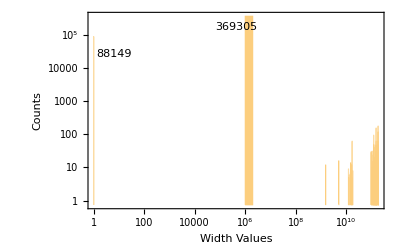

```mathematica
Histogram[datafull[[All,9]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[{88149,369305},{{0.07,0.8},Top},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Width Values","Counts"}]
```

```mathematica
widthmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>4,i/10^((RealDigits@i)[[2]]-4),i,i]],{i,datafull[[All,9]]}]
Counts@(Head/@widthmodified)
```

{1240.,1240.,1240.,1240.,1240.,1240.,1240.,1230.,1230.,1230.,1230.,1230.,1230.,1230.,1220.,1220.,1220.,1220.,1220.,1220.,1220.,1220.,1230.,1230.,1230.,1230.,1230.,1230.,1230.,1530.,1530.,1530.,1530.,1530.,1530.,1530.,1520.,1520.,1520.,1520.,1520.,1520.,1520.,1520.,0,0,0,0,1240.,1240.,459103,0,0,0,0,0,0,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1360.,1360.,1360.,1360.,0,0,0,0,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1350.,1350.,1350.,1350.,NA,NA}
 |  |  |  |

<|Real→397873,Integer→61183,String→147|>

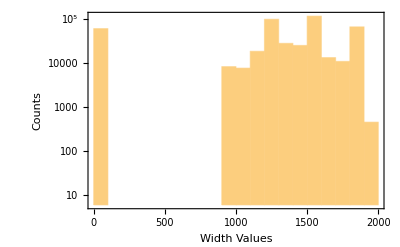

```mathematica
Histogram[widthmodified,ScalingFunctions->"Log",PlotRange->{{0,2000},All},Frame->True,FrameLabel->{"Width Values","Counts"}]
```

Thickness Feature

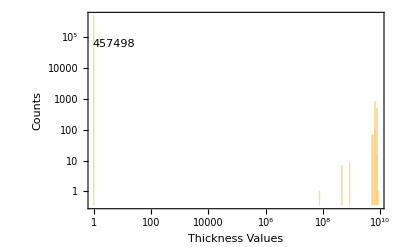

```mathematica
Histogram[datafull[[All,10]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[457498,{0.07,0.85},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Thickness Values","Counts"}]
```

```mathematica
thicknessmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>2,i/10^((RealDigits@i)[[2]]-2),i,i]],{i,datafull[[All,10]]}]
Counts@(Head/@thicknessmodified)
```

{87.,87.,87.,87.,87.,87.,87.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,0,0,0,0,67.,67.,67.,67.,67.,67.,65.,65.,65.,65.,65.,65.,65.,65.,0,0,0,0,0,0,0,459065,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,0,0,0,0,0,0,67.,67.,67.,67.,67.,67.,66.,66.,66.,66.,66.,66.,67.,67.,67.,67.,0,0,0,0,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,NA,NA}
 |  |  |  |

<|Real→397860,Integer→61199,String→144|>

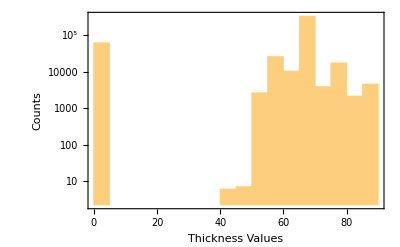

```mathematica
Histogram[thicknessmodified,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"}]
```

Time Windows Generation by Data Partitioning

```mathematica
datafull[[All,9]]=widthmodified;
datafull[[All,10]]=thicknessmodified;
data=Table[Take[datafull,UpTo@i],{i,{46497,91690,138440,183584,230005,275844,320350,367179,413106,459203}}];
```

```mathematica
(* Export["data_with_time_windows.mx",data] *)
```

Investigation of Constraints Impact in Time Windows

Simple Association Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindows=snetworkdatasingleintimewindows[9,10];]
```

{3.9276,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[widthdataintimewindows[[1]][[i]],widthdataintimewindows[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

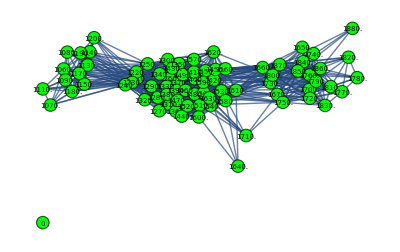
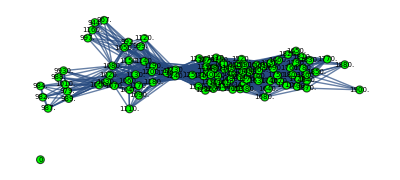
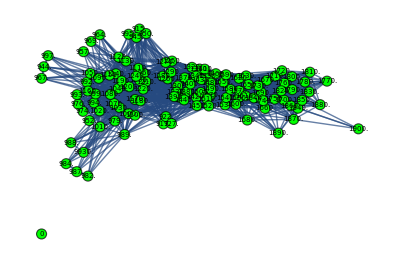
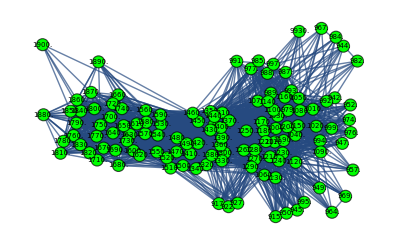
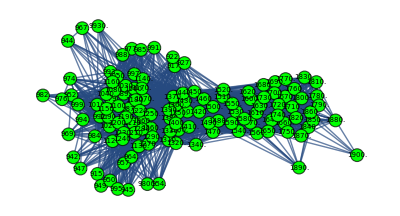
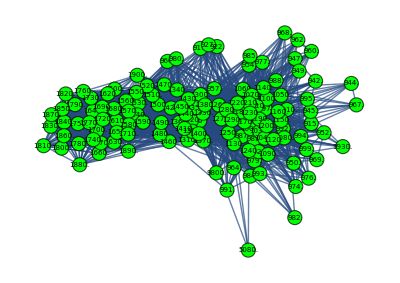
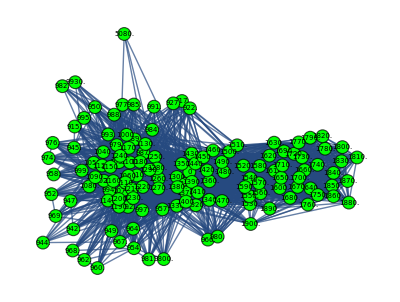
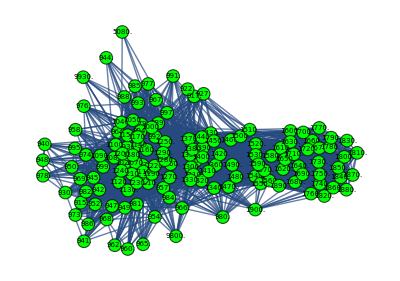
{{-Graphics-,79},{-Graphics-,102},{-Graphics-,119},{-Graphics-,125},{-Graphics-,127},{-Graphics-,133},{-Graphics-,135},{-Graphics-,143},{-Graphics-,144},{-Graphics-,146}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.816837,-0.914287},{0.775318,-0.833272},{0.912826,-0.890899},{0.9729,-0.987608},{0.978297,-0.991312},{0.976393,-0.985596},{0.979992,-0.984999},{0.973833,-0.987195},{0.966704,-0.988102},{0.887562,-0.902762}}

{{0.522385,-0.613315},{0.530661,-0.556155},{0.691093,-0.618492},{0.549054,-0.3911},{0.534222,-0.394403},{0.549708,-0.406185},{0.539973,-0.417934},{0.535635,-0.393469},{0.526522,-0.386032},{0.720341,-0.678254}}

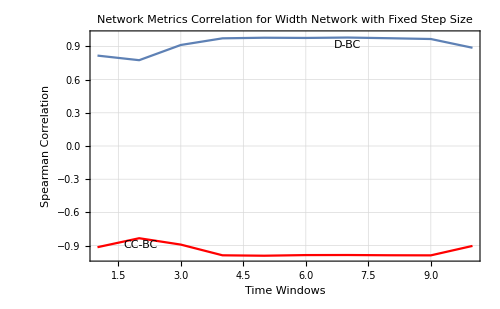
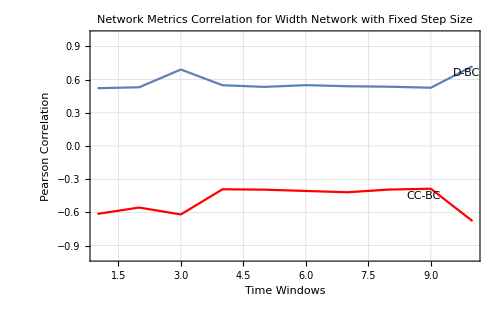

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-15.3086},{2,-27.6464},{3,-10.1391},{4,-0.619594},{5,0.370311},{6,-0.281378},{7,0.426047},{8,-1.50236},{9,-3.50008},{10,-24.4219}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-5.60894},{2,-5.8892},{3,-6.9099},{4,-7.9931},{5,-7.9275},{6,-7.91104},{7,-8.34481},{8,-8.37427},{9,-7.98517},{10,-7.71136}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-57.9931},{2,-74.5995},{3,-58.4635},{4,-113.126},{5,-126.63},{6,-128.182},{7,-131.784},{8,-156.037},{9,-158.978},{10,-86.3946}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.22148},{2,-3.32278},{3,-4.21425},{4,-1.94097},{5,-1.89757},{6,-2.08029},{7,-2.38328},{8,-2.14969},{9,-1.93196},{10,-5.18526}}

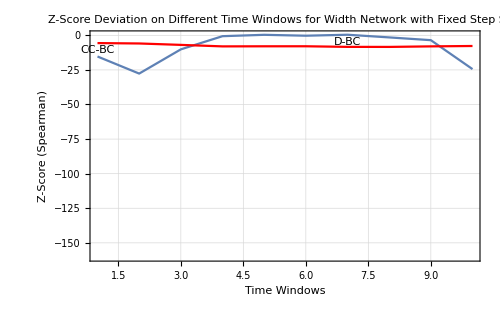
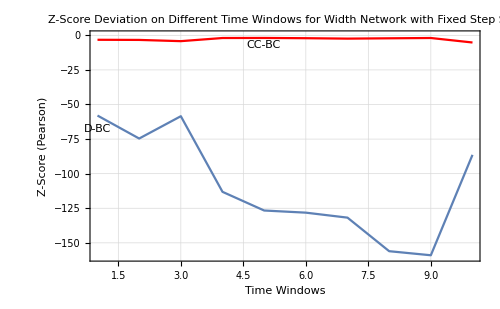

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindows=snetworkdatasingleintimewindows[10,10];]
```

{4.35942,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[thicknessdataintimewindows[[1]][[i]],thicknessdataintimewindows[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

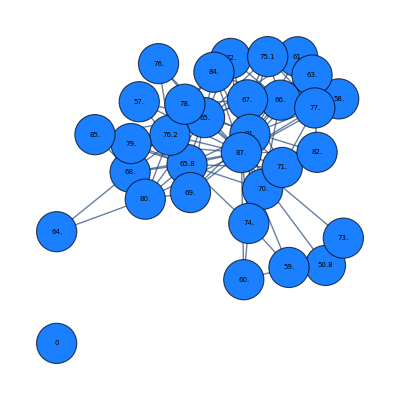
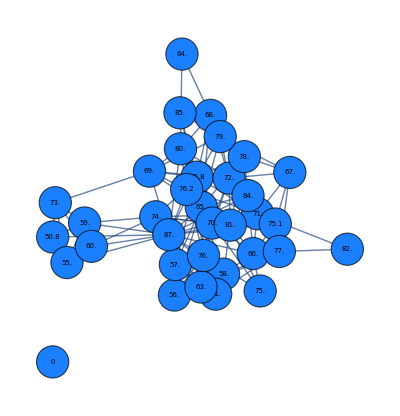
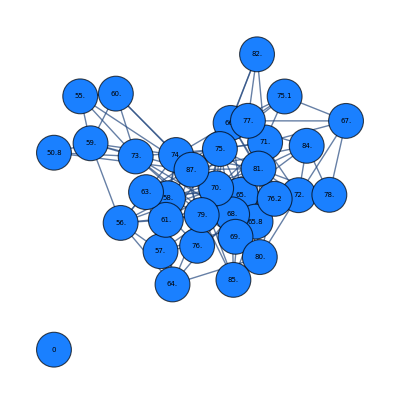
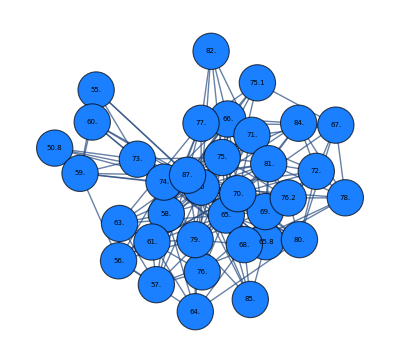
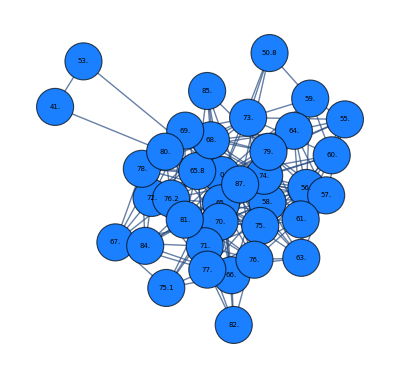
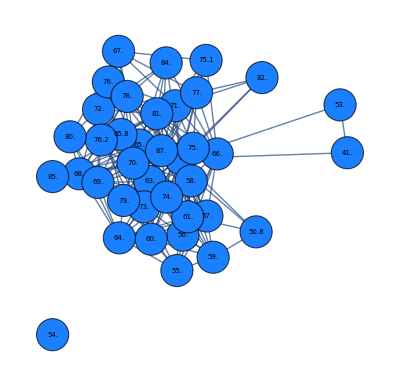
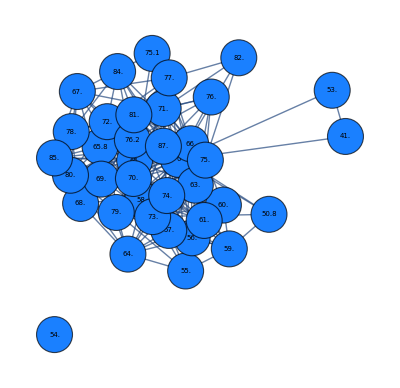
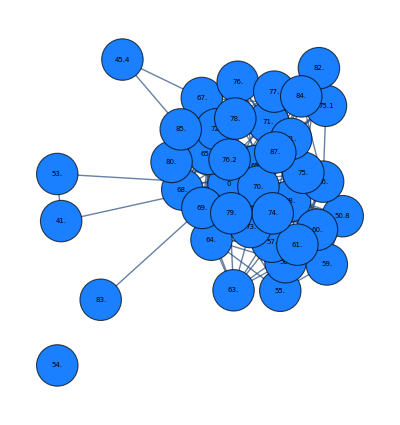
{{-Graphics-,32},{-Graphics-,35},{-Graphics-,35},{-Graphics-,35},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,40},{-Graphics-,41},{-Graphics-,41}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.938808,-0.78658},{0.873987,-0.663998},{0.916719,-0.7004},{0.93912,-0.906811},{0.95285,-0.889666},{0.935017,-0.722435},{0.939483,-0.699436},{0.943043,-0.53645},{0.927237,-0.686511},{0.94354,-0.25778}}

{{0.874484,-0.462631},{0.843387,-0.422115},{0.770286,-0.472945},{0.877292,-0.518271},{0.809918,-0.446188},{0.768257,-0.334724},{0.752032,-0.330238},{0.723693,-0.22225},{0.746908,-0.275495},{0.663251,-0.0583977}}

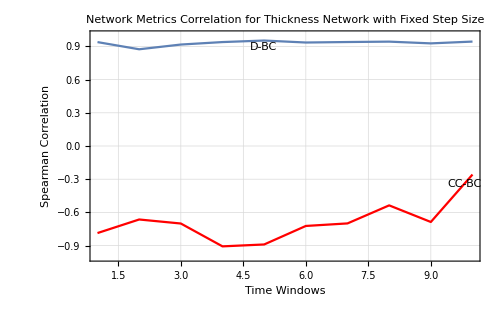
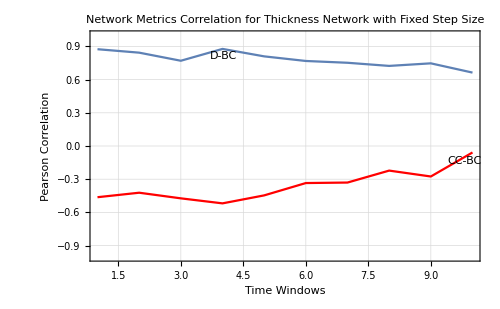

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,0.616193},{2,-1.28733},{3,-0.104282},{4,0.565508},{5,1.07189},{6,0.367045},{7,0.478779},{8,0.559077},{9,-0.0694945},{10,0.590463}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.93182},{2,-2.53266},{3,-2.40751},{4,-3.46177},{5,-3.3986},{6,-2.49543},{7,-2.42854},{8,-1.50394},{9,-2.47674},{10,0.109912}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.510046},{2,-1.66848},{3,-4.13987},{4,-1.43423},{5,-4.2623},{6,-5.6921},{7,-6.62055},{8,-8.47877},{9,-7.56998},{10,-9.23535}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.57851},{2,-1.33152},{3,-1.32984},{4,-1.33201},{5,-0.9891},{6,-0.2925},{7,-0.278031},{8,0.356254},{9,0.0282377},{10,1.29413}}

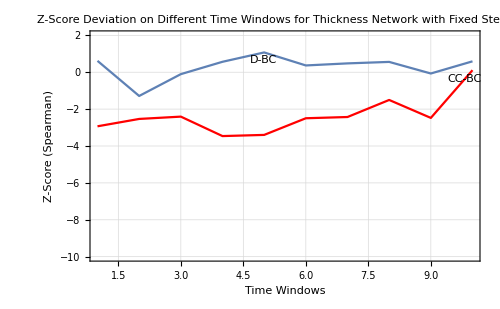
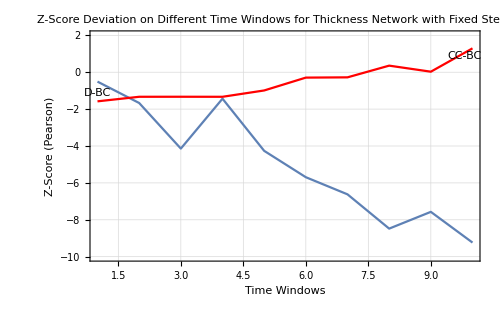

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,20,10];]
```

{939.348,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

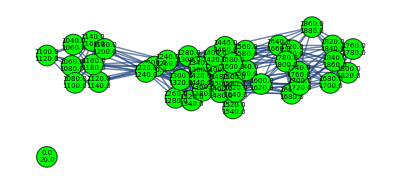
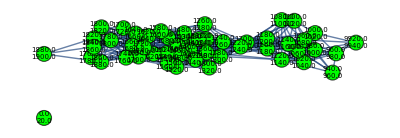
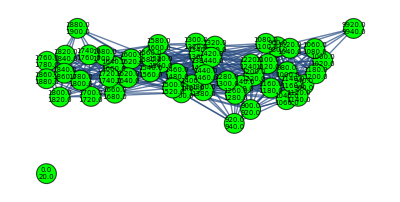
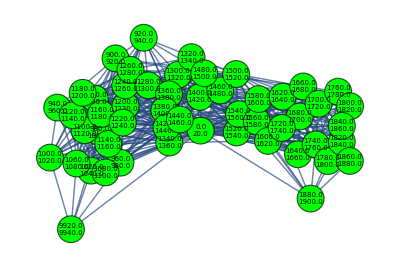
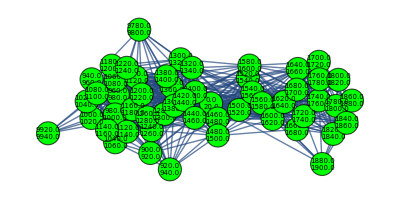
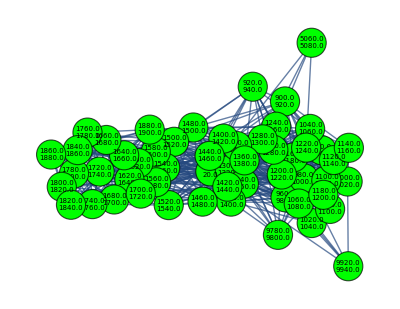
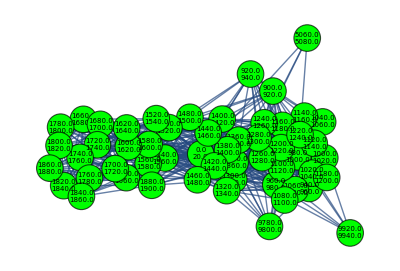
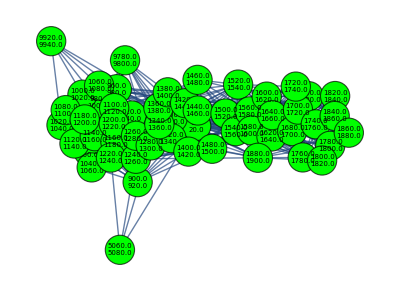
{{-Graphics-,43},{-Graphics-,50},{-Graphics-,52},{-Graphics-,52},{-Graphics-,53},{-Graphics-,54},{-Graphics-,54},{-Graphics-,54},{-Graphics-,54},{-Graphics-,55}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.82433,-0.804068},{0.734855,-0.811107},{0.908269,-0.845656},{0.959018,-0.990457},{0.904981,-0.977276},{0.948857,-0.922007},{0.912036,-0.92532},{0.906995,-0.932347},{0.914195,-0.981357},{0.839404,-0.81029}}

{{0.633363,-0.501172},{0.577619,-0.424247},{0.754601,-0.471542},{0.697417,-0.602426},{0.647809,-0.601992},{0.655278,-0.594798},{0.636646,-0.581435},{0.650767,-0.56981},{0.644673,-0.576368},{0.596069,-0.494557}}

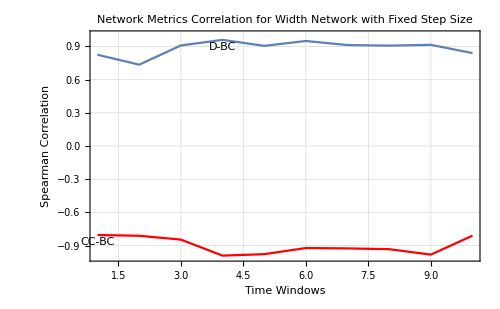
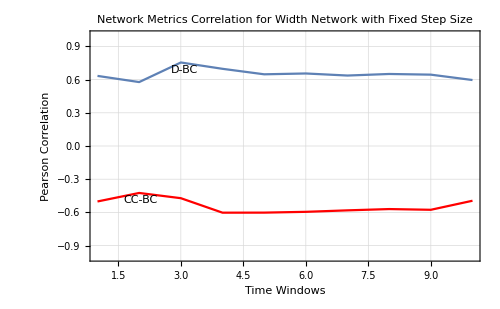

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-5.1755},{2,-11.6583},{3,-2.47415},{4,0.543807},{5,-3.0229},{6,-0.266199},{7,-2.79112},{8,-3.14454},{9,-2.76298},{10,-7.74058}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.10541},{2,-3.49844},{3,-3.74481},{4,-4.40348},{5,-4.34677},{6,-4.13687},{7,-4.03405},{8,-4.18468},{9,-4.52992},{10,-3.36863}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-16.9464},{2,-23.8082},{3,-14.4413},{4,-21.4366},{5,-25.8088},{6,-27.1513},{7,-29.5267},{8,-27.1861},{9,-29.4036},{10,-31.3332}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.20444},{2,-0.944433},{3,-1.1856},{4,-1.87577},{5,-1.86207},{6,-1.86466},{7,-1.74752},{8,-1.71597},{9,-1.75729},{10,-1.28099}}

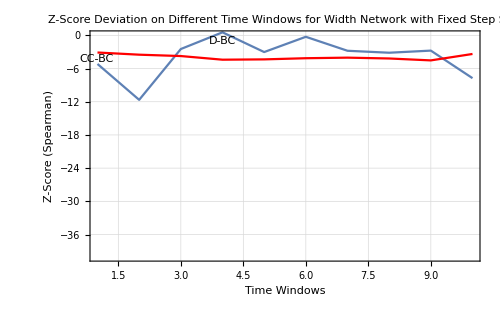
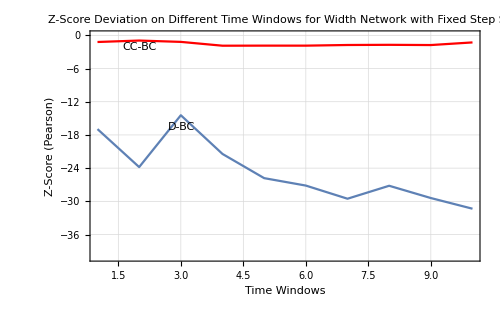

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.05,10];]
```

$Aborted

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

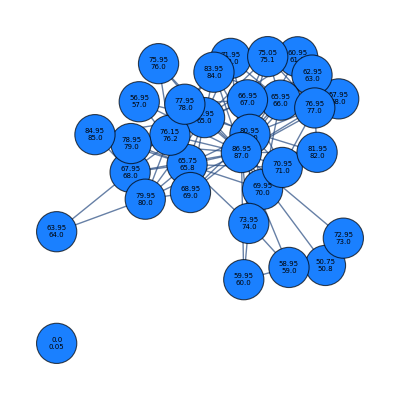
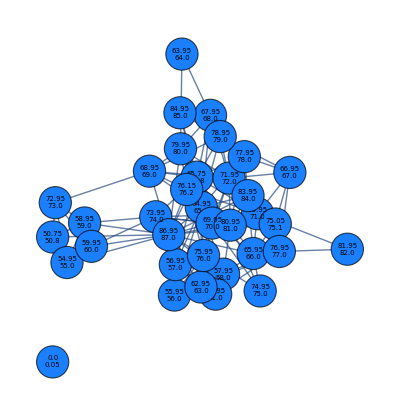
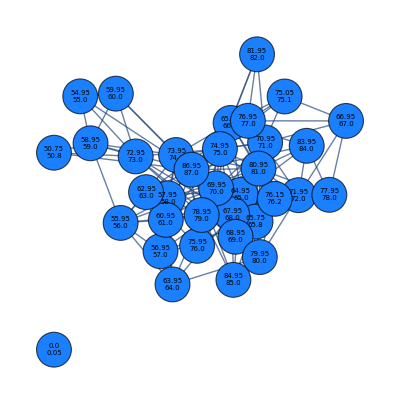
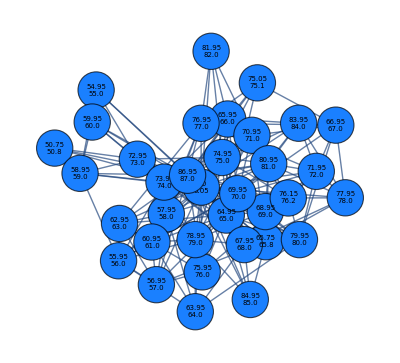
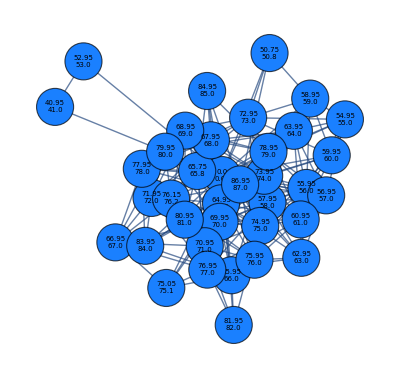
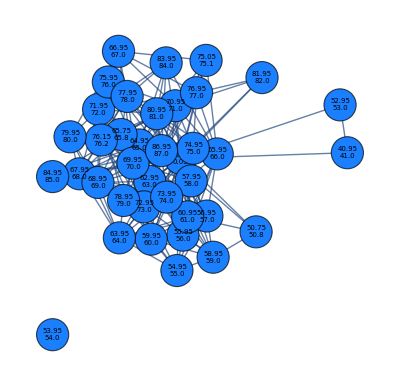
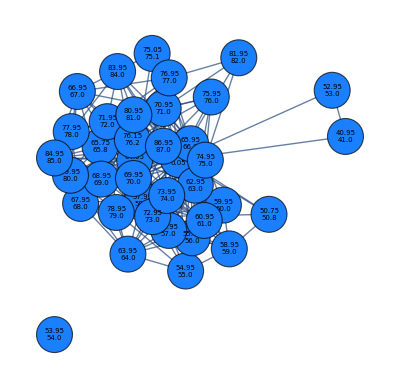
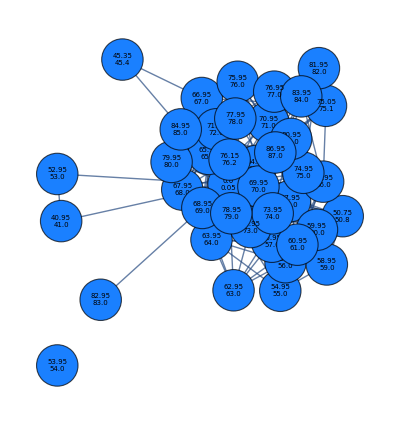
{{-Graphics-,32},{-Graphics-,35},{-Graphics-,35},{-Graphics-,35},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,40},{-Graphics-,41},{-Graphics-,41}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.938808,-0.78658},{0.873987,-0.663998},{0.916719,-0.7004},{0.93912,-0.906811},{0.95285,-0.889666},{0.935017,-0.722435},{0.939483,-0.699436},{0.943043,-0.53645},{0.927237,-0.686511},{0.94354,-0.25778}}

{{0.874484,-0.462631},{0.843387,-0.422115},{0.770286,-0.472945},{0.877292,-0.518271},{0.809918,-0.446188},{0.768257,-0.334724},{0.752032,-0.330238},{0.723693,-0.22225},{0.746908,-0.275495},{0.663251,-0.0583977}}

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

{-Graphics-,-Graphics-}

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,0.616193},{2,-1.28733},{3,-0.104282},{4,0.565508},{5,1.07189},{6,0.367045},{7,0.478779},{8,0.559077},{9,-0.0694945},{10,0.590463}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.93182},{2,-2.53266},{3,-2.40751},{4,-3.46177},{5,-3.3986},{6,-2.49543},{7,-2.42854},{8,-1.50394},{9,-2.47674},{10,0.109912}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.510046},{2,-1.66848},{3,-4.13987},{4,-1.43423},{5,-4.2623},{6,-5.6921},{7,-6.62055},{8,-8.47877},{9,-7.56998},{10,-9.23535}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.57851},{2,-1.33152},{3,-1.32984},{4,-1.33201},{5,-0.9891},{6,-0.2925},{7,-0.278031},{8,0.356254},{9,0.0282377},{10,1.29413}}

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```

{-Graphics-,-Graphics-}

Fixed Bucket Size Networks

Width Feature

Thickness Feature